```mathematica
{a,b}{x,y}==λ{v,w}
```

{a x,b y}=={v λ,w λ}

```mathematica
Solve[{a,b}{x,y}==λ{v,w}, λ]
```

{}

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
JDBCDrivers["PostgreSQL"]
```

JDBCDriver[Name→PostgreSQL,Driver→org.postgresql.Driver,Protocol→jdbc:postgresql://,Version→3.1,Description→PostgreSQL using PostgreSQL JDBC Driver - Version 9.4-1206.,Location→/Applications/Mathematica.app/Contents/SystemFiles/Links/DatabaseLink/DatabaseResources/postgresql.m]

```mathematica
OpenSQLConnection[
JDBC["PostgreSQL","localhost:5432/youtube"],
"Username"->"salvadorguzman",
"Password"->""]
```

SQLConnection[…]

```mathematica
SQLSelect[Out[5], "channels", {"serial"}, "MaxRows"->100]
```

JDBC::error: ERROR: relation "channels" does not exist
  Position: 21

$Failed

```mathematica
SQLSelect[Out[5], "stats.channels", {"serial"}, "MaxRows"->100]
```

{{UC-9-kyTW8ZkZNDHQJ6FgpwQ},{UC-lHJZR3Gqxm24_Vd_AJ5Yw},{UCq-Fj5jknLsUf-MWSy4_brA},{UCIwFjwMjI0y7PDBVEO9-bkQ},{UCffDXn7ycAzwL2LDlbyWOTw},{UC295-Dw_tDNtZXFeAPAW6Aw},{UCRijo3ddMTht_IHyNSNXpNQ},{UCZJ7m7EnCNodqnu5SAtg8eQ},{UC0C-w0YjGpqDXGB8IHb662A},{UCJ5v_MCY6GNUBTO8-D3XoAg},{UCpEhnqL0y41EpW2TvWAHD7Q},{UCfM3zsQsOnfWNUppiycmBuw},{UC3KQ5GWANYF8lChqjZpXsQw},{UCYvmuw-JtVrTZQ-7Y4kd63Q},{UCqECaJ8Gagnn7YCbPEzWH6g},{UCXazgXDIYyWH-yXLAkcrFxw},{UCcgqSM4YEo5vVQpqwN-MaNw},{UCV4xOVpbcV8SdueDCOxLXtQ},{UCYiGq8XF7YQD00x7wAd62Zg},{UCb2HGwORFBo94DmRx4oLzow},{UCp0hYYBW6IMayGgR-WeoCvQ},{UC9CoOnJkIBMdeijd9qYoT_g},{UCV306eHqgo0LvBf3Mh36AHg},{UCYWOjHweP2V-8kGKmmAmQJQ},{UCFFbwnve3yF62-tVXkTyHqg},{UCam8T03EOFBsNdR0thrFHdQ},{UCKqH_9mk1waLgBiL2vT5b9g},{UCY30JRSgfhYXA6i6xX1erWg},{UCYLNGLIzMhRTi6ZOLjAPSmw},{UCpDJl2EmP7Oh90Vylx0dZtA},{UCa10nxShhzNrCE1o2ZOPztg},{UCoUM-UJ7rirJYP8CQ0EIaHA},{UCBNs31xysxpAGMheg8OrngA},{UCxoq-PAQeAdk_zyg8YS0JqA},{UC7_YxT-KID8kRbqZo7MyscQ},{UCbCmjCuTUZos6Inko4u57UQ},{UClZkHt2kNIgyrTTPnSQV3SA},{UCYzPXprvl5Y-Sf0g4vX-m6g},{UCS5Oz6CHmeoF7vSad0qqXfw},{UCBVjMGOIkavEAhyqpxJ73Dw},{UCEdvpU2pFRCVqU6yIPyTpMQ},{UCBnZ16ahKA2DZ_T5W0FPUXg},{UCPNxhDvTcytIdvwXWAm43cA},{UCVtFOytbRpEvzLjvqGG5gxQ},{UCbTVTephX30ZhQF5zwFppBg},{UCppHT7SZKKvar4Oc9J4oljQ},{UCjIA3wwhi0QjSOXAZwOXbPA},{UCKqx9r4mrFglauNBJc1L_eg},{UC_gV70G_Y51LTa3qhu8KiEA},{UCaWd5_7JhbQBe4dknZhsHJg},{UC9gFih9rw0zNCK3ZtoKQQyA},{UC1l7wYrva1qCH-wgqcHaaRg},{UCG8rbF3g2AMX70yOd8vqIZg},{UC_aEa8K-EOJ3D6gOs7HcyNg},{UCAW-NpUFkMyCNrvRSSGIvDQ},{UCECJDeK0MNapZbpaOzxrUPA},{UCt-k6JwNWHMXDBGm9IYHdsg},{UCoGDh1Xa3kUCpok24JN5DKA},{UCsRM0YB_dabtEPGPTKo-gcw},{UC3ZkCd7XtUREnjjt3cyY_gg},{UC_TVqp_SyG6j5hG-xVRy95A},{UC8-Th83bH_thdKZDJCrn88g},{UC3gNmTGu-TTbFPpfSs5kNkg},{UCJrOtniJ0-NWz37R30urifQ},{UClZuKq2m0Qu-HkopkSBLpEw},{UCpko_-a4wgz2u_DgDgd9fqA},{UCuHzBCaKmtaLcRAOoazhCPA},{UC2pmfLm7iq6Ov1UwYrWYkZA},{UCPHXtOVmjvbP9OJihsd7gCg},{UC4rlAVgAK0SGk-yTfe48Qpw},{UC3IZKseVpdzPSBaWxBxundA},{UCNUQK9mQoqi4yNXw2_Rj6SA},{UCV9_KinVpV-snHe3C3n1hvA},{UCcgVECVN4OKV6DH1jLkqmcA},{UCRv76wLBC73jiP7LX4C3l8Q},{UC3jOd7GUMhpgJRBhiLzuLsg},{UC56gTxNs4f9xZ7Pa2i5xNzg},{UCRx3mKNUdl8QE06nEug7p6Q},{UC9TO_oo4c_LrOiKNaY6aysA},{UCKAqou7V9FAWXpZd9xtOg3Q},{UC22nIfOTM7KLIQuFGMKzQbg},{UC-yXuc1__OzjwpsJPlxYUCQ},{UChGJGhZ9SOOHvBB0Y4DOO_w},{UCj0O6W8yDuLg3iraAXKgCrQ},{UCpb_iJuhFe8V6rQdbNqfAlQ},{UCVp3nfGRxmMadNDuVbJSk8A},{UCK1i2UviaXLUNrZlAFpw_jA},{UCJ0uqCI0Vqr2Rrt1HseGirg},{UCzVIrPfZBE-XkBISBybMBLA},{UCxSz6JVYmzVhtkraHWZC7HQ},{UCq3Ci-h945sbEYXpVlw7rJg},{UC-6czyMkxDi8E8akPl0c7_w},{UCByOQJjav0CUDwxCk-jVNRQ},{UCEf_Bc-KVd7onSeifS3py9g},{UCAvCL8hyXjSUHKEGuUPr1BA},{UCmv1CLT6ZcFdTJMHxaR9XeA},{UCpGdL9Sn3Q5YWUH2DVUW1Ug},{UCOsyDsO5tIt-VZ1iwjdQmew},{UCsPF3cApzCohxPp5oKdoWSQ},{UCs8qka8tfhdc69wzXYdtZ3A}}

```mathematica
SQLSelect[Out[5], "stats.channels", {"serial"}, "MaxRows"->100]//TableForm
```

UC-9-kyTW8ZkZNDHQJ6FgpwQ
UC-lHJZR3Gqxm24_Vd_AJ5Yw
UCq-Fj5jknLsUf-MWSy4_brA
UCIwFjwMjI0y7PDBVEO9-bkQ
UCffDXn7ycAzwL2LDlbyWOTw
UC295-Dw_tDNtZXFeAPAW6Aw
UCRijo3ddMTht_IHyNSNXpNQ
UCZJ7m7EnCNodqnu5SAtg8eQ
UC0C-w0YjGpqDXGB8IHb662A
UCJ5v_MCY6GNUBTO8-D3XoAg
UCpEhnqL0y41EpW2TvWAHD7Q
UCfM3zsQsOnfWNUppiycmBuw
UC3KQ5GWANYF8lChqjZpXsQw
UCYvmuw-JtVrTZQ-7Y4kd63Q
UCqECaJ8Gagnn7YCbPEzWH6g
UCXazgXDIYyWH-yXLAkcrFxw
UCcgqSM4YEo5vVQpqwN-MaNw
UCV4xOVpbcV8SdueDCOxLXtQ
UCYiGq8XF7YQD00x7wAd62Zg
UCb2HGwORFBo94DmRx4oLzow
UCp0hYYBW6IMayGgR-WeoCvQ
UC9CoOnJkIBMdeijd9qYoT_g
UCV306eHqgo0LvBf3Mh36AHg
UCYWOjHweP2V-8kGKmmAmQJQ
UCFFbwnve3yF62-tVXkTyHqg
UCam8T03EOFBsNdR0thrFHdQ
UCKqH_9mk1waLgBiL2vT5b9g
UCY30JRSgfhYXA6i6xX1erWg
UCYLNGLIzMhRTi6ZOLjAPSmw
UCpDJl2EmP7Oh90Vylx0dZtA
UCa10nxShhzNrCE1o2ZOPztg
UCoUM-UJ7rirJYP8CQ0EIaHA
UCBNs31xysxpAGMheg8OrngA
UCxoq-PAQeAdk_zyg8YS0JqA
UC7_YxT-KID8kRbqZo7MyscQ
UCbCmjCuTUZos6Inko4u57UQ
UClZkHt2kNIgyrTTPnSQV3SA
UCYzPXprvl5Y-Sf0g4vX-m6g
UCS5Oz6CHmeoF7vSad0qqXfw
UCBVjMGOIkavEAhyqpxJ73Dw
UCEdvpU2pFRCVqU6yIPyTpMQ
UCBnZ16ahKA2DZ_T5W0FPUXg
UCPNxhDvTcytIdvwXWAm43cA
UCVtFOytbRpEvzLjvqGG5gxQ
UCbTVTephX30ZhQF5zwFppBg
UCppHT7SZKKvar4Oc9J4oljQ
UCjIA3wwhi0QjSOXAZwOXbPA
UCKqx9r4mrFglauNBJc1L_eg
UC_gV70G_Y51LTa3qhu8KiEA
UCaWd5_7JhbQBe4dknZhsHJg
UC9gFih9rw0zNCK3ZtoKQQyA
UC1l7wYrva1qCH-wgqcHaaRg
UCG8rbF3g2AMX70yOd8vqIZg
UC_aEa8K-EOJ3D6gOs7HcyNg
UCAW-NpUFkMyCNrvRSSGIvDQ
UCECJDeK0MNapZbpaOzxrUPA
UCt-k6JwNWHMXDBGm9IYHdsg
UCoGDh1Xa3kUCpok24JN5DKA
UCsRM0YB_dabtEPGPTKo-gcw
UC3ZkCd7XtUREnjjt3cyY_gg
UC_TVqp_SyG6j5hG-xVRy95A
UC8-Th83bH_thdKZDJCrn88g
UC3gNmTGu-TTbFPpfSs5kNkg
UCJrOtniJ0-NWz37R30urifQ
UClZuKq2m0Qu-HkopkSBLpEw
UCpko_-a4wgz2u_DgDgd9fqA
UCuHzBCaKmtaLcRAOoazhCPA
UC2pmfLm7iq6Ov1UwYrWYkZA
UCPHXtOVmjvbP9OJihsd7gCg
UC4rlAVgAK0SGk-yTfe48Qpw
UC3IZKseVpdzPSBaWxBxundA
UCNUQK9mQoqi4yNXw2_Rj6SA
UCV9_KinVpV-snHe3C3n1hvA
UCcgVECVN4OKV6DH1jLkqmcA
UCRv76wLBC73jiP7LX4C3l8Q
UC3jOd7GUMhpgJRBhiLzuLsg
UC56gTxNs4f9xZ7Pa2i5xNzg
UCRx3mKNUdl8QE06nEug7p6Q
UC9TO_oo4c_LrOiKNaY6aysA
UCKAqou7V9FAWXpZd9xtOg3Q
UC22nIfOTM7KLIQuFGMKzQbg
UC-yXuc1__OzjwpsJPlxYUCQ
UChGJGhZ9SOOHvBB0Y4DOO_w
UCj0O6W8yDuLg3iraAXKgCrQ
UCpb_iJuhFe8V6rQdbNqfAlQ
UCVp3nfGRxmMadNDuVbJSk8A
UCK1i2UviaXLUNrZlAFpw_jA
UCJ0uqCI0Vqr2Rrt1HseGirg
UCzVIrPfZBE-XkBISBybMBLA
UCxSz6JVYmzVhtkraHWZC7HQ
UCq3Ci-h945sbEYXpVlw7rJg
UC-6czyMkxDi8E8akPl0c7_w
UCByOQJjav0CUDwxCk-jVNRQ
UCEf_Bc-KVd7onSeifS3py9g
UCAvCL8hyXjSUHKEGuUPr1BA
UCmv1CLT6ZcFdTJMHxaR9XeA
UCpGdL9Sn3Q5YWUH2DVUW1Ug
UCOsyDsO5tIt-VZ1iwjdQmew
UCsPF3cApzCohxPp5oKdoWSQ
UCs8qka8tfhdc69wzXYdtZ3A

```mathematica
apple=Map[Last,FinancialData["NASDAQ:AAPL", "Price", All]]
```

{0.5134,0.486614,0.4509,0.462057,0.475457,0.504471,0.529028,0.551342,0.580357,0.633928,0.642857,0.627242,0.609385,0.616071,0.602685,0.5759,0.551342,0.540185,0.5692,0.564742,0.544642,0.546885,0.558042,0.553571,0.587056,0.5692,0.580357,0.587056,0.584828,0.5759,0.571428,0.553571,0.533485,0.504471,0.475457,0.493314,0.511171,0.511171,0.5134,0.486614,0.486614,0.470985,0.466528,0.455357,0.466528,0.486614,0.4576,0.433042,0.439742,0.424114,0.4509,0.4576,0.473214,0.475457,0.468757,0.464285,0.462057,0.4576,0.421885,0.401785,0.386171,0.401785,0.397328,0.412957,0.433042,0.459828,0.455357,0.459828,0.477685,0.475457,0.466528,0.4576,0.441971,0.441971,0.4375,0.433042,0.470985,0.473214,0.464285,0.459828,0.482142,0.491071,0.497771,0.497771,0.497771,0.473214,0.446428,0.446428,0.459828,0.491071,0.508928,0.522328,0.517857,0.5134,0.504471,0.497771,0.5067,0.5067,0.504471,0.502242,0.488842,0.495542,0.5,0.488842,0.488842,0.486614,0.479914,0.491071,0.5,0.491071,0.5067,0.535714,0.560271,0.558042,0.589285,0.589285,0.591528,0.591528,0.5625,0.5625,0.573671,0.564742,0.544642,0.555814,0.5625,0.587056,0.580357,0.578128,0.566971,0.558042,0.555814,0.540185,0.5201,0.529028,0.515628,0.526785,0.5201,0.502242,0.464285,0.459828,0.459828,0.4442,0.448671,0.466528,0.430814,0.397328,0.406257,0.424114,0.435271,0.446428,0.462057,0.430814,0.428571,0.404028,0.415185,0.428571,0.446428,0.430814,0.424114,0.439742,0.446428,0.441971,0.448671,0.462057,0.4509,0.4509,0.446428,0.4375,0.428571,0.415185,0.408485,0.3951,0.386171,0.3817,0.386171,0.359385,0.337057,0.345985,0.339285,0.341528,0.359385,0.359385,0.3817,0.3884,0.368314,0.363842,0.352685,0.352685,0.354914,0.350457,0.339285,0.330357,0.323671,0.314742,0.316971,0.3192,0.301342,0.294642,0.292414,0.254471,0.2567,0.2701,0.272328,0.272328,0.294642,0.303571,0.301342,0.3192,0.330357,0.3326,0.343757,0.343757,0.323671,0.330357,0.3259,0.3326,0.350457,0.350457,0.348214,0.339285,0.339285,0.345985,0.357142,0.352685,0.357142,0.357142,0.352685,0.343757,0.3192,0.321428,0.3259,0.328128,0.337057,0.348214,0.323671,0.3192,0.3259,0.337057,0.337057,0.339285,0.323671,0.321428,0.328128,0.337057,0.3326,0.3326,0.334828,0.330357,0.339285,0.341528,0.334828,0.337057,0.337057,0.334828,0.323671,0.3326,0.348214,0.377242,0.408485,0.390628,0.397328,0.3884,0.390628,0.372771,0.379471,0.3951,0.3951,0.392857,0.372771,0.368314,0.339285,0.354914,0.3326,0.321428,0.3192,0.334828,0.357142,0.363842,0.354914,0.361614,0.368314,0.370542,0.359385,0.345985,0.348214,0.359385,0.363842,0.359385,0.361614,0.361614,0.352685,0.352685,0.330357,0.330357,0.334828,0.330357,0.334828,0.328128,0.3326,0.337057,0.334828,0.330357,0.3259,0.328128,0.3259,0.3259,0.328128,0.328128,0.328128,0.321428,0.296885,0.292414,0.294642,0.290185,0.290185,0.272328,0.2701,0.265628,0.252242,0.272328,0.296885,0.3192,0.314742,0.296885,0.294642,0.290185,0.296885,0.301342,0.301342,0.316971,0.316971,0.316971,0.314742,0.310271,0.3125,0.3125,0.310271,0.285714,0.287957,0.292414,0.301342,0.294642,0.281257,0.279028,0.274557,0.274557,0.281257,0.272328,0.261171,0.261171,0.2634,0.272328,0.281257,0.276785,0.285714,0.290185,0.285714,0.276785,0.2701,0.272328,0.261171,0.2567,0.252242,0.25,0.252242,0.254471,0.2567,0.2567,0.254471,0.25,0.25,0.245542,0.25,0.241071,0.234385,0.234385,0.232142,0.227685,0.229914,0.238842,0.238842,0.238842,0.238842,0.234385,0.229914,0.232142,0.238842,0.25,0.247771,0.236614,0.236614,0.229914,0.227685,0.225457,0.216528,0.2076,0.205357,0.198671,0.205357,0.209828,0.220985,0.225457,0.234385,0.238842,0.238842,0.2567,0.2567,0.258928,0.254471,0.243314,0.241071,0.232142,0.241071,0.243314,0.247771,0.234385,0.229914,0.223214,0.218757,0.223214,0.241071,0.238842,0.234385,0.234385,0.241071,0.254471,0.254471,0.258928,0.265628,0.276785,0.287957,0.308042,0.3192,0.303571,0.3125,0.323671,0.314742,0.3259,0.328128,0.310271,0.321428,0.316971,0.323671,0.3259,0.337057,0.334828,0.323671,0.316971,0.321428,0.328128,0.339285,0.337057,0.323671,0.323671,0.328128,0.330357,0.3259,0.3326,0.334828,0.337057,0.361614,0.390628,0.419642,0.428571,0.415185,0.419642,0.421885,0.410714,0.419642,0.428571,0.453128,0.464285,0.462057,0.435271,0.4375,0.448671,0.448671,0.453128,0.477685,0.511171,0.549114,0.553571,0.537957,0.515628,0.533485,0.553571,0.589285,0.578128,0.564742,0.535714,0.560271,0.560271,0.551342,0.5201,0.515628,0.526785,0.517857,0.515628,0.5692,0.580357,0.580357,0.566971,0.598214,0.604914,0.591528,0.5625,0.522328,0.511171,0.5067,0.504471,0.5134,0.537957,0.535714,0.540185,0.555814,0.571428,0.584828,0.580357,0.560271,0.535714,0.533485,0.508928,0.537957,0.540185,0.5201,0.491071,0.5134,0.526785,0.549114,0.549114,0.589285,0.609385,0.595985,0.600456,0.667414,0.667414,0.629471,0.654028,0.680814,0.727685,0.732142,0.729914,0.745542,0.765628,0.796885,0.785714,0.754471,0.747771,0.754471,0.803571,0.830357,0.8259,0.810271,0.794642,0.785714,0.810271,0.830357,0.837056,0.859385,0.834828,0.814742,0.828128,0.834828,0.808042,0.796885,0.781257,0.756699,0.779028,0.767857,0.756699,0.738842,0.75,0.75,0.756699,0.767857,0.785714,0.794642,0.756699,0.770099,0.770099,0.758928,0.781257,0.790185,0.754471,0.754471,0.734385,0.720985,0.714285,0.707599,0.703128,0.743314,0.758928,0.785714,0.803571,0.816971,0.839285,0.830357,0.904028,0.928571,0.910714,0.868314,0.892857,0.883928,0.892857,0.901785,0.875,0.866071,0.919642,0.979914,0.984385,0.970985,0.977685,0.953128,0.944199,0.948671,0.924114,0.926342,0.9375,0.966528,1.01563,1.02679,1.08036,1.07143,1.06027,1.06027,1.03126,1.03796,1.04464,1.09599,1.12054,1.0826,1.0692,1.0625,1.05804,1.02233,1.,0.970985,1.02233,1.00224,0.953128,0.959828,0.988842,0.957599,0.9509,0.899556,0.837056,0.877242,0.872771,0.879471,0.843757,0.845985,0.834828,0.8259,0.848214,0.828128,0.823671,0.821428,0.792414,0.790185,0.781257,0.736614,0.774556,0.781257,0.770099,0.698671,0.647328,0.607142,0.622771,0.616071,0.613842,0.622771,0.593757,0.604914,0.607142,0.613842,0.611614,0.602685,0.598214,0.613842,0.604914,0.591528,0.598214,0.602685,0.600456,0.5692,0.540185,0.544642,0.551342,0.558042,0.587056,0.665185,0.649556,0.678571,0.703128,0.618314,0.566971,0.546885,0.546885,0.571428,0.564742,0.537957,0.524557,0.571428,0.573671,0.5625,0.580357,0.433042,0.441971,0.419642,0.408485,0.406257,0.412957,0.412957,0.408485,0.401785,0.397328,0.363842,0.352685,0.345985,0.377242,0.410714,0.406257,0.375,0.345985,0.383928,0.363842,0.354914,0.377242,0.379471,0.359385,0.377242,0.372771,0.404028,0.410714,0.419642,0.390628,0.377242,0.375,0.3192,0.343757,0.350457,0.357142,0.352685,0.352685,0.357142,0.366071,0.368314,0.383928,0.383928,0.363842,0.366071,0.375,0.370542,0.363842,0.361614,0.354914,0.363842,0.366071,0.375,0.383928,0.386171,0.383928,0.401785,0.417414,0.435271,0.441971,0.428571,0.417414,0.433042,0.441971,0.439742,0.441971,0.446428,0.435271,0.435271,0.4576,0.497771,0.504471,0.495542,0.468757,0.493314,0.5,0.497771,0.486614,0.497771,0.511171,0.5134,0.517857,0.511171,0.515628,0.486614,0.482142,0.493314,0.466528,0.441971,0.441971,0.439742,0.4442,0.4375,0.415185,0.430814,0.415185,0.421885,0.435271,0.433042,0.4576,0.448671,0.453128,0.446428,0.466528,0.488842,0.479914,0.484385,0.482142,0.455357,0.468757,0.482142,0.486614,0.477685,0.459828,0.473214,0.479914,0.470985,0.488842,0.482142,0.475457,0.477685,0.475457,0.468757,0.464285,0.464285,0.455357,0.455357,0.459828,0.446428,0.455357,0.453128,0.441971,0.4442,0.446428,0.4375,0.430814,0.419642,0.419642,0.441971,0.4375,0.459828,0.459828,0.468757,0.491071,0.5,0.504471,0.504471,0.5067,0.497771,0.493314,0.531257,0.537957,0.560271,0.593757,0.589285,0.564742,0.537957,0.555814,0.587056,0.591528,0.591528,0.5759,0.564742,0.5692,0.544642,0.5201,0.531257,0.5692,0.551342,0.540185,0.524557,0.526785,0.524557,0.517857,0.524557,0.542414,0.529028,0.497771,0.517857,0.5134,0.511171,0.511171,0.5201,0.531257,0.515628,0.517857,0.529028,0.524557,0.540185,0.517857,0.511171,0.486614,0.464285,0.4509,0.470985,0.473214,0.4576,0.4509,0.441971,0.448671,0.468757,0.479914,0.473214,0.475457,0.470985,0.459828,0.459828,0.453128,0.453128,0.453128,0.448671,0.475457,0.477685,0.486614,0.484385,0.455357,0.455357,0.446428,0.430814,0.488842,0.522328,0.529028,0.508928,0.531257,0.508928,0.535714,0.515628,0.497771,0.502242,0.491071,0.488842,0.508928,0.5,0.502242,0.502242,0.497771,0.504471,0.491071,0.482142,0.473214,0.468757,0.468757,0.473214,0.473214,0.470985,0.479914,0.466528,0.491071,0.497771,0.511171,0.493314,0.482142,0.484385,0.479914,0.475457,0.466528,0.459828,0.459828,0.448671,0.4375,0.441971,0.448671,0.453128,0.4442,0.4442,0.439742,0.426342,0.424114,0.406257,0.428571,0.426342,0.4442,0.4576,0.4576,0.453128,0.464285,0.468757,0.4509,0.439742,0.441971,0.446428,0.4442,0.446428,0.4442,0.441971,0.468757,0.459828,0.441971,0.415185,0.430814,0.419642,0.424114,0.424114,0.415185,0.390628,0.404028,0.412957,0.424114,0.428571,0.439742,0.462057,0.453128,0.441971,0.435271,0.4442,0.466528,0.488842,0.486614,0.477685,0.470985,0.455357,0.459828,0.470985,0.482142,0.511171,0.491071,0.488842,0.482142,0.491071,0.493314,0.495542,0.5134,0.5201,0.497771,0.5067,0.5067,0.504471,0.5,0.5134,0.535714,0.531257,0.546885,0.535714,0.540185,0.502242,0.511171,0.522328,0.537957,0.529028,0.517857,0.529028,0.540185,0.533485,0.533485,0.517857,0.511171,0.522328,0.526785,0.535714,0.533485,0.533485,0.544642,0.531257,0.5067,0.493314,0.5,0.493314,0.470985,0.479914,0.493314,0.486614,0.477685,0.448671,0.441971,0.4442,0.4509,0.462057,0.439742,0.3951,0.383928,0.397328,0.410714,0.3884,0.3884,0.404028,0.408485,0.392857,0.397328,0.404028,0.397328,0.386171,0.401785,0.390628,0.390628,0.3951,0.386171,0.375,0.375,0.372771,0.372771,0.350457,0.350457,0.375,0.3817,0.372771,0.3817,0.386171,0.404028,0.408485,0.401785,0.386171,0.3951,0.392857,0.392857,0.390628,0.377242,0.379471,0.372771,0.343757,0.357142,0.352685,0.357142,0.354914,0.357142,0.361614,0.357142,0.352685,0.357142,0.3817,0.3884,0.3817,0.370542,0.368314,0.352685,0.323671,0.301342,0.305814,0.314742,0.310271,0.285714,0.308042,0.301342,0.303571,0.292414,0.287957,0.287957,0.281257,0.265628,0.2634,0.265628,0.272328,0.279028,0.281257,0.287957,0.308042,0.3125,0.323671,0.328128,0.321428,0.323671,0.308042,0.3125,0.314742,0.314742,0.314742,0.321428,0.321428,0.3192,0.316971,0.3125,0.314742,0.308042,0.310271,0.301342,0.294642,0.290185,0.296885,0.296885,0.285714,0.290185,0.283485,0.283485,0.281257,0.274557,0.272328,0.265628,0.2701,0.272328,0.267857,0.272328,0.261171,0.258928,0.261171,0.267857,0.272328,0.272328,0.265628,0.2634,0.2701,0.272328,0.272328,0.265628,0.267857,0.2634,0.265628,0.265628,0.267857,0.272328,0.274557,0.276785,0.287957,0.281257,0.272328,0.272328,0.290185,0.303571,0.299114,0.301342,0.294642,0.283485,0.283485,0.283485,0.281257,0.281257,0.279028,0.276785,0.267857,0.267857,0.2701,0.267857,0.283485,0.285714,0.296885,0.303571,0.321428,0.3259,0.316971,0.308042,0.321428,0.321428,0.328128,0.321428,0.321428,0.3192,0.339285,0.3326,0.3326,0.334828,0.3326,0.343757,0.350457,0.366071,0.357142,0.354914,0.345985,0.357142,0.354914,0.354914,0.343757,0.339285,0.339285,0.339285,0.341528,0.345985,0.357142,0.359385,0.361614,0.359385,0.366071,0.359385,0.352685,0.345985,0.348214,0.352685,0.357142,0.357142,0.372771,0.368314,0.397328,0.401785,0.399557,0.390628,0.3884,0.3884,0.399557,0.397328,0.392857,0.397328,0.399557,0.397328,0.410714,0.408485,0.404028,0.406257,0.410714,0.415185,0.426342,0.4375,0.428571,0.426342,0.428571,0.417414,0.410714,0.404028,0.3951,0.397328,0.421885,0.410714,0.412957,0.426342,0.424114,0.424114,0.430814,0.428571,0.426342,0.426342,0.428571,0.426342,0.424114,0.426342,0.446428,0.448671,0.4509,0.459828,0.470985,0.464285,0.4576,0.446428,0.439742,0.439742,0.4509,0.453128,0.441971,0.439742,0.4442,0.441971,0.441971,0.466528,0.464285,0.479914,0.473214,0.504471,0.493314,0.477685,0.497771,0.504471,0.504471,0.504471,0.486614,0.486614,0.482142,0.477685,0.486614,0.493314,0.484385,0.486614,0.482142,0.479914,0.488842,0.504471,0.517857,0.531257,0.542414,0.533485,0.529028,0.560271,0.5759,0.571428,0.558042,0.540185,0.540185,0.544642,0.573671,0.582599,0.5625,0.589285,0.595985,0.649556,0.642857,0.658485,0.642857,0.642857,0.636171,0.631699,0.660714,0.656257,0.660714,0.658485,0.665185,0.660714,0.660714,0.662956,0.676342,0.691971,0.694199,0.674114,0.642857,0.642857,0.645099,0.642857,0.649556,0.640628,0.611614,0.611614,0.625,0.642857,0.620542,0.622771,0.640628,0.647328,0.640628,0.640628,0.631699,0.645099,0.671885,0.636171,0.611614,0.618314,0.631699,0.662956,0.647328,0.622771,0.598214,0.5759,0.566971,0.598214,0.618314,0.609385,0.591528,0.607142,0.578128,0.558042,0.544642,0.558042,0.560271,0.5625,0.573671,0.555814,0.566971,0.564742,0.598214,0.611614,0.642857,0.642857,0.6384,0.631699,0.631699,0.647328,0.6384,0.647328,0.649556,0.654028,0.660714,0.674114,0.660714,0.620542,0.620542,0.633928,0.627242,0.620542,0.6384,0.625,0.582599,0.566971,0.591528,0.622771,0.611614,0.607142,0.600456,0.629471,0.645099,0.627242,0.616071,0.611614,0.580357,0.598214,0.609385,0.609385,0.602685,0.609385,0.589285,0.584828,0.589285,0.593757,0.618314,0.607142,0.595985,0.600456,0.600456,0.587056,0.584828,0.580357,0.591528,0.589285,0.607142,0.595985,0.595985,0.611614,0.618314,0.625,0.6384,0.660714,0.645099,0.6384,0.631699,0.633928,0.654028,0.633928,0.629471,0.649556,0.631699,0.625,0.629471,0.642857,0.678571,0.718757,0.723214,0.714285,0.716528,0.741071,0.7634,0.758928,0.781257,0.758928,0.756699,0.776785,0.765628,0.736614,0.745542,0.758928,0.736614,0.738842,0.752242,0.752242,0.752242,0.747771,0.732142,0.723214,0.732142,0.723214,0.729914,0.767857,0.781257,0.799114,0.799114,0.810271,0.8125,0.796885,0.859385,0.890628,0.870542,0.948671,0.921885,0.875,0.9375,0.897328,0.8884,0.941971,0.988842,0.966528,0.991071,0.997771,0.991071,0.982142,0.962056,0.946428,0.939742,0.941971,1.00893,1.04689,1.10939,1.18527,1.13393,1.11384,1.09376,1.12724,1.16964,1.23439,1.23439,1.25,1.20536,1.16071,1.2076,1.22321,1.2009,1.15403,1.19197,1.18304,1.16518,1.13393,1.16518,1.19643,1.17857,1.22099,1.21876,1.20536,1.18304,1.19197,1.2009,1.16071,1.11607,1.15179,1.19197,1.28126,1.28126,1.25,1.20983,1.23214,1.26786,1.25447,1.20536,1.21429,1.26786,1.27679,1.2701,1.33483,1.3259,1.35714,1.33483,1.33929,1.375,1.3884,1.41518,1.42857,1.42411,1.43304,1.42857,1.43304,1.41071,1.375,1.34821,1.40179,1.41518,1.39733,1.35268,1.30804,1.33036,1.33036,1.32367,1.39286,1.41964,1.42857,1.41071,1.3884,1.37947,1.3884,1.40179,1.3884,1.3884,1.40179,1.40179,1.41071,1.41071,1.40179,1.48214,1.44643,1.48214,1.46429,1.5,1.47321,1.5,1.44643,1.44643,1.45536,1.44643,1.42857,1.4509,1.45536,1.40179,1.33036,1.34821,1.35714,1.44643,1.53571,1.57143,1.57143,1.54464,1.49107,1.47768,1.51786,1.49107,1.51786,1.50893,1.49554,1.46429,1.48214,1.47321,1.4375,1.50893,1.54464,1.65179,1.66071,1.72321,1.76786,1.74107,1.75,1.75,1.76786,1.74107,1.78571,1.84821,1.89286,1.86607,1.85714,1.85714,1.85714,1.85714,1.92857,1.875,1.85714,1.83036,1.80357,1.78126,1.88393,1.91964,1.94643,1.89286,1.84821,1.84821,1.85714,1.84821,1.79464,1.93304,1.97321,2.01786,2.05357,1.99107,1.94643,2.01786,2.08036,2.08928,2.11607,1.99107,1.98214,1.9375,1.93304,1.90179,1.94643,1.90179,1.85714,1.72321,1.30357,1.23214,1.44643,1.3125,1.26786,1.,1.08036,1.14286,1.28571,1.37947,1.38393,1.29464,1.28571,1.35714,1.34821,1.33036,1.29464,1.33036,1.38393,1.33036,1.35714,1.25,1.29464,1.23214,1.26786,1.29464,1.32143,1.30357,1.25,1.17857,1.1875,1.16071,1.08929,1.09821,1.17857,1.23214,1.25,1.24107,1.21429,1.33036,1.33929,1.40179,1.40179,1.44643,1.49107,1.48214,1.50893,1.52233,1.4375,1.50447,1.54911,1.5,1.59821,1.59376,1.5625,1.58929,1.42857,1.51786,1.5,1.50893,1.50893,1.53126,1.52679,1.52679,1.41964,1.43304,1.40179,1.45983,1.41964,1.41964,1.47321,1.48214,1.49107,1.47321,1.41071,1.41964,1.37947,1.38393,1.41964,1.46429,1.4509,1.46429,1.47321,1.49554,1.49107,1.49107,1.54464,1.52679,1.50893,1.49107,1.49107,1.53571,1.54464,1.59821,1.66071,1.67411,1.67411,1.65179,1.66964,1.61607,1.63393,1.65179,1.60714,1.64733,1.60714,1.59821,1.56697,1.57143,1.51786,1.45983,1.43304,1.48214,1.46429,1.41071,1.42857,1.38393,1.40179,1.49107,1.45536,1.46429,1.48214,1.49107,1.47321,1.41071,1.41071,1.42857,1.4375,1.41964,1.41071,1.43304,1.45983,1.48214,1.49107,1.47768,1.46429,1.46429,1.49107,1.5,1.49107,1.47321,1.45536,1.45983,1.41071,1.41964,1.44643,1.47321,1.44643,1.41964,1.39286,1.38393,1.35714,1.3884,1.375,1.40626,1.41964,1.48214,1.51786,1.49107,1.53571,1.57143,1.57143,1.60714,1.55357,1.58929,1.60714,1.61607,1.63393,1.58929,1.59821,1.5759,1.60268,1.62947,1.60714,1.60714,1.58929,1.65179,1.65626,1.65179,1.66071,1.6875,1.66071,1.6384,1.61607,1.61161,1.59821,1.59821,1.60714,1.60714,1.625,1.59821,1.58036,1.53571,1.51786,1.52679,1.52679,1.52679,1.53126,1.58483,1.60714,1.59376,1.59821,1.59376,1.58036,1.57143,1.55357,1.49554,1.54464,1.51786,1.47321,1.51786,1.5,1.51786,1.45536,1.41964,1.41071,1.45536,1.43304,1.4375,1.45983,1.45983,1.42411,1.3884,1.41964,1.3884,1.36607,1.38393,1.44643,1.46429,1.46429,1.5,1.48661,1.50893,1.49107,1.48214,1.52679,1.57143,1.5625,1.52679,1.54911,1.55357,1.57143,1.54464,1.51786,1.48214,1.45983,1.41964,1.41964,1.375,1.39286,1.38393,1.39286,1.38393,1.375,1.40626,1.42857,1.48214,1.46429,1.42857,1.42411,1.40179,1.39286,1.375,1.37947,1.35714,1.33036,1.3259,1.34821,1.33929,1.375,1.40179,1.41071,1.375,1.3884,1.39286,1.35714,1.36607,1.35714,1.30804,1.29018,1.31697,1.30357,1.30357,1.3125,1.34376,1.38393,1.40179,1.41071,1.41071,1.40626,1.39733,1.39733,1.375,1.38393,1.41964,1.41071,1.43304,1.45536,1.46429,1.49107,1.46429,1.46876,1.44643,1.4375,1.44643,1.4375,1.44197,1.5,1.50893,1.52233,1.53571,1.52233,1.50447,1.52679,1.54464,1.5625,1.44197,1.41964,1.44643,1.46429,1.46429,1.48661,1.48214,1.49107,1.34376,1.33483,1.34821,1.40179,1.41964,1.40179,1.375,1.39286,1.36607,1.36607,1.33036,1.32143,1.27679,1.29464,1.29911,1.3125,1.33929,1.3125,1.3125,1.28571,1.30357,1.29464,1.28571,1.25,1.24107,1.26786,1.27679,1.25893,1.27679,1.25,1.25,1.25893,1.25,1.25893,1.24554,1.24554,1.24554,1.20536,1.22768,1.20536,1.21429,1.22321,1.24107,1.27233,1.25,1.23214,1.25,1.28571,1.33483,1.32143,1.34821,1.375,1.375,1.38393,1.40179,1.43304,1.45983,1.45536,1.43304,1.43304,1.42857,1.41964,1.40626,1.39286,1.39286,1.42411,1.4375,1.46429,1.48214,1.50893,1.51786,1.54018,1.56697,1.59821,1.64286,1.62054,1.61607,1.59821,1.63393,1.64286,1.625,1.70536,1.72321,1.73214,1.69643,1.70536,1.74107,1.75,1.67857,1.66964,1.72321,1.70536,1.67857,1.69643,1.73214,1.77233,1.69643,1.58929,1.57143,1.53571,1.51786,1.54464,1.56697,1.55357,1.52233,1.49107,1.4509,1.47321,1.45536,1.44643,1.47321,1.47321,1.44643,1.41964,1.42857,1.4509,1.45536,1.45536,1.40179,1.44643,1.42857,1.42857,1.40179,1.38393,1.36607,1.40179,1.40626,1.41964,1.42411,1.44643,1.47321,1.52679,1.5625,1.5759,1.57143,1.54464,1.49554,1.45536,1.47768,1.44197,1.46429,1.50893,1.50893,1.53126,1.5625,1.5759,1.59821,1.59821,1.5759,1.58929,1.58929,1.59376,1.59821,1.59821,1.59821,1.60714,1.63393,1.64286,1.60714,1.59821,1.60714,1.57143,1.54464,1.59376,1.59821,1.60268,1.61607,1.61607,1.59821,1.625,1.58929,1.58483,1.55804,1.58036,1.625,1.71876,1.76786,1.76786,1.74554,1.74107,1.63393,1.66964,1.6875,1.72321,1.74107,1.71429,1.66964,1.7009,1.66071,1.61607,1.61607,1.63393,1.66071,1.64733,1.57143,1.54464,1.54464,1.57143,1.60714,1.64286,1.66964,1.66071,1.59821,1.58036,1.59821,1.59821,1.61607,1.61607,1.59821,1.59821,1.57143,1.5759,1.57143,1.58036,1.57143,1.61607,1.60714,1.52679,1.52679,1.49107,1.40179,1.28571,1.28571,1.24554,1.20536,1.24107,1.25,1.27679,1.29464,1.30357,1.26786,1.25447,1.23661,1.25893,1.33036,1.33929,1.34376,1.34821,1.35714,1.34376,1.28571,1.23214,1.23214,1.22321,1.24554,1.1875,1.15626,1.22321,1.1875,1.20536,1.21429,1.21876,1.16964,1.1875,1.21429,1.21429,1.2009,1.22321,1.25,1.24107,1.1875,1.17857,1.22321,1.21429,1.23214,1.22321,1.22321,1.20536,1.19643,1.21429,1.17857,1.1875,1.21429,1.19643,1.21429,1.22321,1.20536,1.23214,1.25893,1.2634,1.3125,1.31697,1.30804,1.31697,1.3125,1.3125,1.4375,1.5134,1.47768,1.48661,1.45536,1.50893,1.50893,1.5,1.47321,1.46876,1.4375,1.4375,1.49107,1.47321,1.4375,1.42411,1.46876,1.47321,1.51786,1.54464,1.5625,1.54464,1.54464,1.4375,1.4375,1.41964,1.38393,1.38393,1.3884,1.39733,1.40626,1.41518,1.41964,1.42857,1.42857,1.48214,1.49107,1.49554,1.47768,1.52233,1.49107,1.49107,1.48214,1.48214,1.41964,1.41071,1.47768,1.5,1.5,1.42857,1.46429,1.47768,1.47321,1.45536,1.45536,1.41071,1.41071,1.39286,1.36607,1.39286,1.44643,1.41964,1.41964,1.41071,1.40179,1.41518,1.42857,1.49554,1.48214,1.47321,1.4509,1.48214,1.53571,1.59821,1.57143,1.57143,1.55357,1.59821,1.66518,1.67857,1.67857,1.69197,1.66964,1.62947,1.58036,1.59376,1.49107,1.46429,1.48214,1.50447,1.50893,1.47768,1.47768,1.5134,1.5,1.5134,1.55357,1.47321,1.41071,1.41071,1.43304,1.41071,1.38393,1.42411,1.41964,1.40179,1.375,1.30357,1.3125,1.29464,1.25447,1.23214,1.27679,1.34821,1.36161,1.33036,1.29464,1.32143,1.32143,1.28571,1.27679,1.29911,1.27679,1.21429,1.21429,1.20536,1.21429,1.20536,1.19197,1.16071,1.12947,1.125,1.08036,1.07143,1.0625,1.00893,1.03571,1.08929,1.05804,0.964285,1.,1.,1.04018,1.,0.946428,0.991071,1.00893,0.991071,0.892857,0.946428,1.01786,1.12054,1.11161,1.10714,1.08929,1.07143,1.07143,1.06697,1.08483,1.09821,1.08929,1.13393,1.1875,1.19643,1.1875,1.23214,1.26786,1.29464,1.28571,1.32143,1.28571,1.25447,1.29911,1.26786,1.29018,1.29911,1.3125,1.33929,1.3125,1.3125,1.3125,1.36161,1.375,1.43304,1.47321,1.51786,1.49107,1.42857,1.41518,1.45536,1.42411,1.43304,1.50893,1.49554,1.57143,1.60714,1.57143,1.5625,1.55357,1.53571,1.53571,1.55357,1.53571,1.54464,1.54464,1.54464,1.61607,1.68304,1.67857,1.65179,1.66964,1.77679,1.83036,1.79464,1.8125,1.83036,1.84821,1.86161,1.91071,1.94643,1.91964,1.98214,1.98214,1.99107,1.97321,2.0625,2.03126,2.0625,2.14286,2.19197,2.14286,2.14286,2.04018,2.05804,2.14286,2.17857,2.10714,2.13393,2.07143,2.08036,2.08036,2.04464,2.0625,2.08483,2.23214,2.25,2.40178,2.32143,2.26786,2.24554,2.36607,2.33036,2.36607,2.41964,2.48214,2.41964,2.3125,2.25893,2.30357,2.5,2.47321,2.42857,2.44643,2.59821,2.5,2.55357,2.47768,2.5,2.45536,2.3884,2.53571,2.5625,2.22321,2.29464,2.25893,2.17857,2.12947,2.19643,2.19643,2.16964,2.08928,2.09376,2.08036,1.96429,1.6875,1.75,1.75,1.79464,1.80804,1.77679,1.8125,1.83036,1.88393,1.91071,1.80357,1.75,1.67857,1.58036,1.61607,1.65179,1.61161,1.6384,1.64286,1.67857,1.7009,1.67857,1.75893,1.75447,1.71429,1.66518,1.64733,1.64286,1.59376,1.5134,1.50447,1.46876,1.5,1.50447,1.49107,1.5,1.5,1.49107,1.5134,1.53571,1.51786,1.48214,1.51786,1.50893,1.54018,1.62947,1.66964,1.67411,1.6875,1.66964,1.66964,1.625,1.5625,1.51786,1.60268,1.64286,1.64286,1.60714,1.60714,1.61607,1.60268,1.625,1.66071,1.65179,1.75447,1.78571,1.73214,1.76786,1.79911,1.80357,1.8125,1.84821,1.91071,1.95983,1.90179,1.90179,1.80357,1.82143,1.91964,1.9375,1.89286,1.89286,1.92857,1.90179,1.89286,1.89286,1.875,1.83929,1.82143,1.83929,1.90179,1.79018,1.80357,1.80804,1.73661,1.6875,1.75,1.79018,1.77679,1.80804,1.76786,1.79464,1.80357,1.78571,1.75,1.76786,1.8125,1.77679,1.70536,1.72321,1.71876,1.72321,1.71429,1.70536,1.73214,1.78126,1.875,1.91071,1.87054,1.96429,1.95536,1.94643,1.89733,1.86161,1.83036,1.83929,1.84821,1.77679,1.83929,1.82143,1.77679,1.74107,1.71429,1.77679,1.90179,1.91964,1.94643,1.93304,1.95536,1.78571,1.86161,1.83036,1.80357,1.82143,1.83036,1.83036,1.83929,1.82143,1.8125,1.84821,1.80357,1.80357,1.78571,1.74107,1.75447,1.75447,1.75,1.7634,1.79911,1.80357,1.80357,1.84821,1.8125,1.79464,1.83929,1.86607,1.95983,1.96429,2.02678,2.0134,2.125,2.10714,2.07143,2.11161,2.16071,2.22321,2.22321,2.21428,2.30357,2.26786,2.24107,2.3125,2.28571,2.18304,2.26786,2.30357,2.30804,2.30357,2.33036,2.25893,2.27678,2.3125,2.34821,2.34821,2.36161,2.29018,2.28571,2.25447,2.24554,2.33036,2.29464,2.29018,2.24107,2.21428,2.30804,2.32143,2.36161,2.44643,2.49554,2.44643,2.41071,2.40178,2.37054,2.32143,2.26786,2.28571,2.27678,2.27678,2.25893,2.24107,2.25447,2.2634,2.24554,2.27678,2.25,2.25893,2.25,2.32143,2.30357,2.28571,2.17857,2.0759,2.08036,2.10714,2.09821,2.10714,2.16964,2.04464,1.99554,2.04464,1.98214,2.01786,2.09821,2.16071,2.10714,2.02678,2.00893,2.05804,2.03571,2.01786,1.99107,1.9375,2.03571,2.14733,2.11607,2.16071,2.16071,2.20536,2.16964,2.21428,2.22321,2.22321,2.24107,2.19197,2.16518,2.15626,2.12054,2.14286,2.11161,2.125,2.11607,2.15178,2.125,2.13393,2.05357,2.01786,1.93304,1.94643,1.95983,1.9375,1.92857,1.91964,1.92411,1.9509,1.87947,1.75893,1.69643,1.61607,1.59821,1.58036,1.61607,1.64286,1.62947,1.61607,1.66964,1.71429,1.75,1.65179,1.65179,1.58036,1.63393,1.6384,1.63393,1.67857,1.69643,1.71429,1.74107,1.60714,1.59821,1.63393,1.58036,1.59821,1.6384,1.61607,1.66071,1.6875,1.6875,1.66964,1.63393,1.625,1.59821,1.57143,1.54911,1.5759,1.55357,1.5759,1.59821,1.59821,1.59821,1.59821,1.58929,1.59821,1.59821,1.54464,1.58483,1.58036,1.58929,1.60714,1.64286,1.66071,1.73214,1.70536,1.6875,1.70536,1.75,1.75893,1.7009,1.76786,1.72321,1.67857,1.64286,1.66071,1.66071,1.63393,1.69643,1.65179,1.625,1.59821,1.60268,1.61161,1.58036,1.5625,1.55357,1.59821,1.5625,1.55357,1.54911,1.57143,1.62054,1.64286,1.625,1.75,1.75,1.75447,1.73214,1.74107,1.74107,1.83929,1.83929,1.86607,1.90179,1.875,1.86607,1.85714,1.875,1.96429,1.99107,1.97321,2.00893,2.02678,2.03126,2.00893,2.04911,1.97321,2.0625,2.08036,2.05357,2.02678,2.05357,2.01786,2.01786,2.05357,2.08036,2.04464,2.05357,2.03126,2.0625,2.0759,2.05804,2.04464,2.05357,2.04464,2.0134,1.96429,2.03126,2.08036,2.12947,2.16518,2.13393,2.10714,2.125,2.12947,2.09821,2.13393,2.08036,2.11607,2.20536,2.17857,2.22321,2.29018,2.19643,2.26786,2.32143,2.15178,2.125,2.13393,2.14286,2.14286,2.125,2.14286,2.16964,2.15178,2.1384,2.125,2.1875,2.15178,2.14286,2.125,2.04464,2.01786,2.03126,1.99107,1.96876,1.92411,1.89286,1.92411,1.96429,1.96429,1.96876,1.9375,1.91518,1.95536,1.89286,1.90179,1.9375,1.9509,1.96429,1.96429,2.01786,2.02678,2.02678,2.03126,2.00893,2.03571,2.01786,1.96876,1.94643,1.91964,1.90179,1.88393,1.91964,1.95536,1.90179,1.82143,1.86607,1.83929,1.84821,1.79018,1.78571,1.74107,1.80357,1.77679,1.78571,1.73214,1.74107,1.6875,1.71876,1.73214,1.78571,1.77233,1.78571,1.75893,1.75,1.79464,1.83483,1.8125,1.83036,1.85268,1.90626,1.94643,1.91964,1.95536,1.96429,1.94643,1.90179,1.98214,1.98214,1.99107,1.98214,2.04464,2.09821,2.05357,2.05804,2.0134,2.0625,2.05357,2.02233,2.03571,2.03571,2.0134,1.95983,1.8125,1.76786,1.58036,1.58929,1.5625,1.59376,1.5,1.50893,1.47321,1.46429,1.41518,1.47768,1.44643,1.49107,1.42857,1.43304,1.39286,1.41071,1.35714,1.375,1.34821,1.30357,1.30357,1.3125,1.35714,1.33036,1.33036,1.27679,0.982142,0.915185,0.959828,0.9375,0.946428,0.9375,0.959828,0.946428,0.959828,0.973214,0.991071,1.01786,1.03571,1.08036,1.05357,1.04464,1.0625,1.01786,0.982142,0.946428,0.977685,0.982142,1.0134,1.01786,0.982142,1.,1.0134,1.,0.973214,0.959828,0.946428,0.928571,0.946428,0.928571,0.919642,0.919642,0.9375,0.955357,0.928571,0.9375,0.901785,0.866071,0.875,0.883928,0.901785,0.8884,0.875,0.910714,0.883928,0.892857,0.883928,0.883928,0.852685,0.834828,0.8125,0.8125,0.839285,0.843757,0.821428,0.808042,0.848214,0.857142,0.857142,0.848214,1.00893,1.0134,0.991071,0.991071,1.08036,1.08036,1.07143,1.0625,1.13393,1.10714,1.09821,1.125,1.16964,1.12947,1.15179,1.1384,1.09821,1.0759,1.09821,1.12054,1.13393,1.14286,1.21429,1.19643,1.19643,1.17857,1.16071,1.17857,1.17857,1.16518,1.13393,1.125,1.125,1.13393,1.125,1.15179,1.15179,1.1384,1.07143,1.00893,1.05357,1.04018,1.0625,1.04911,1.05357,1.01786,0.982142,1.,0.973214,1.01786,1.04018,1.01786,1.0625,1.04464,1.06697,1.125,1.20536,1.16964,1.18304,1.2009,1.1384,1.08929,1.09376,1.10714,1.08483,1.04911,1.04464,1.06697,1.19197,1.25,1.20983,1.19643,1.21876,1.21429,1.16964,1.1875,1.17857,1.19643,1.19643,1.30357,1.27679,1.29464,1.30357,1.32143,1.32143,1.3259,1.3125,1.32143,1.29464,1.33036,1.33036,1.30804,1.28571,1.30357,1.29464,1.27233,1.27679,1.3125,1.35268,1.32143,1.33929,1.33036,1.33036,1.36161,1.34376,1.3125,1.30357,1.29911,1.26786,1.25,1.25447,1.23214,1.16964,1.1875,1.16964,1.16071,1.1875,1.1875,1.19643,1.19643,1.18527,1.19643,1.19643,1.14286,1.13393,1.125,1.08036,1.05804,1.03571,1.00893,1.05804,1.0625,1.10714,1.11607,1.08036,1.07143,1.10714,1.08036,1.17857,1.17411,1.15403,1.11607,1.10714,1.08036,1.06027,1.07143,1.05357,1.04911,1.09376,1.14733,1.10939,1.08929,1.09821,1.11607,1.08929,1.0692,1.04464,1.00893,0.977685,0.986614,0.977685,0.982142,0.933042,0.964285,0.946428,0.964285,0.966528,0.993313,0.941971,0.946428,0.968757,0.928571,0.9375,0.897328,0.914628,0.9375,0.955357,0.933042,0.946428,0.919642,0.946428,0.933042,0.957599,0.966528,0.964285,1.0134,1.06027,1.02233,1.00893,1.0134,0.988842,0.9509,1.,1.10714,1.1317,1.12054,1.10939,1.1384,1.20313,1.19197,1.16296,1.18304,1.1875,1.1875,1.20536,1.2009,1.23661,1.22546,1.24107,1.23661,1.24107,1.25,1.23661,1.24554,1.24554,1.25,1.24554,1.25224,1.27679,1.2634,1.29464,1.29241,1.25,1.2634,1.2701,1.29018,1.29018,1.27679,1.27679,1.27903,1.25447,1.28571,1.29911,1.26786,1.23439,1.21876,1.20983,1.21206,1.21206,1.20983,1.20983,1.21876,1.20313,1.18304,1.20536,1.35268,1.29464,1.32143,1.3884,1.41518,1.50447,1.46876,1.46876,1.41964,1.47321,1.47321,1.46429,1.52233,1.50893,1.52233,1.54464,1.52679,1.50447,1.54243,1.54028,1.47771,1.48214,1.442,1.45543,1.509,1.48671,1.47557,1.46886,1.51786,1.47771,1.46214,1.42857,1.42857,1.36171,1.33486,1.317,1.34828,1.35057,1.36614,1.33043,1.29243,1.30586,1.32814,1.34157,1.30814,1.28129,1.29471,1.30357,1.29914,1.35271,1.326,1.33043,1.39743,1.375,1.37057,1.37957,1.38843,1.39743,1.39743,1.41071,1.39286,1.37057,1.40629,1.38843,1.5,1.47157,1.56028,1.66971,1.62057,1.60271,1.58929,1.60714,1.62957,1.63843,1.52243,1.509,1.48671,1.46371,1.41071,1.42414,1.43314,1.442,1.43314,1.48671,1.44643,1.44643,1.45771,1.51128,1.55814,1.56257,1.56257,1.53357,1.52014,1.54243,1.51786,1.46429,1.45771,1.43528,1.39286,1.36614,1.41071,1.42857,1.42857,1.43757,1.41971,1.36843,1.413,1.41971,1.41071,1.36171,1.25,1.25,1.259,1.25457,1.259,1.29471,1.35943,1.326,1.34828,1.32814,1.22771,1.22771,1.26343,1.259,1.26786,1.20986,1.24114,1.31257,1.31257,1.30814,1.34828,1.39286,1.36614,1.37057,1.33929,1.29914,1.34386,1.39743,1.39286,1.34828,1.36614,1.35271,1.36614,1.36614,1.36171,1.36171,1.375,1.38843,1.44643,1.47328,1.48,1.46429,1.55814,1.55814,1.56257,1.57143,1.54914,1.52686,1.576,1.567,1.55357,1.54914,1.52457,1.5,1.48443,1.50671,1.50457,1.55357,1.57143,1.54028,1.53357,1.55357,1.57757,1.57143,1.55814,1.55814,1.567,1.58486,1.692,1.76343,1.75457,1.74114,1.71886,1.65629,1.66528,1.68757,1.65857,1.67643,1.66071,1.67857,1.73671,1.73671,1.68314,1.67857,1.701,1.74114,1.75,1.71886,1.625,1.68086,1.56257,1.62057,1.634,1.62057,1.672,1.625,1.60714,1.55357,1.58486,1.60714,1.58043,1.54914,1.51786,1.54028,1.52686,1.538,1.54911,1.57371,1.58929,1.59386,1.60271,1.576,1.59828,1.625,1.634,1.59828,1.53571,1.54028,1.54914,1.53571,1.53357,1.55357,1.56257,1.59828,1.59828,1.58043,1.53357,1.51343,1.42857,1.28129,1.31028,1.31257,1.30814,1.32143,1.326,1.33986,1.33486,1.29471,1.34828,1.33043,1.34386,1.34386,1.29914,1.30357,1.27457,1.24343,1.23886,1.24557,1.26128,1.28571,1.29028,1.30814,1.33486,1.24114,1.25457,1.25457,1.25457,1.24114,1.24557,1.24114,1.259,1.297,1.30804,1.30814,1.30357,1.36171,1.41528,1.38839,1.40629,1.41971,1.45986,1.48214,1.46429,1.42634,1.43314,1.37946,1.37957,1.37957,1.43528,1.40625,1.42857,1.40179,1.36161,1.34386,1.41071,1.41071,1.38393,1.37729,1.37054,1.37946,1.35714,1.37057,1.36614,1.259,1.15186,1.16971,1.16528,1.16071,1.15186,1.14514,1.15629,1.14286,1.13843,1.14743,1.14743,1.12729,1.22328,1.23671,1.16971,1.22328,1.25,1.20986,1.21886,1.23443,1.21429,1.14071,1.067,1.08929,1.12946,1.15186,1.08043,1.09386,1.04028,0.975571,0.986714,1.01343,1.04464,1.04471,1.05814,1.009,0.995535,0.991142,1.01786,1.02243,0.986714,1.,0.982142,1.03571,1.05814,1.067,1.067,1.05357,1.02243,0.991142,0.982142,0.959857,0.9375,0.951,0.935285,0.922,0.928571,0.924142,0.922,0.919714,0.919642,0.924142,0.933142,0.919714,0.901857,0.897428,0.906285,0.857142,0.852714,0.901857,0.863857,0.877285,0.910714,0.892857,0.877285,0.861714,0.870571,0.928571,0.928571,0.919714,0.910714,0.919714,0.924142,0.901857,0.884,0.895142,0.897428,0.884,0.866142,0.888428,0.884,0.884,0.870571,0.870571,0.848285,0.852714,0.915285,0.959857,0.955428,0.933142,0.973285,0.966571,0.982142,1.01786,1.01343,0.986714,0.997857,0.968857,0.930857,0.937571,0.955428,0.942,0.888428,0.910714,0.933142,0.884,0.863857,0.897321,0.866142,0.870535,0.861714,0.857142,0.866142,0.879571,0.855,0.843857,0.812571,0.826,0.812571,0.808142,0.794714,0.736714,0.709857,0.736714,0.75,0.767857,0.75,0.692,0.696428,0.683142,0.678571,0.669642,0.638428,0.645142,0.613857,0.602714,0.602714,0.745571,0.741142,0.723285,0.732142,0.743428,0.75,0.785714,0.794714,0.763428,0.785714,0.759,0.772428,0.75,0.767857,0.799142,0.790285,0.826,0.821428,0.803571,0.812571,0.794714,0.803571,0.843857,0.839285,0.821428,0.830428,0.852714,0.861714,0.887857,0.888428,0.875,0.866142,0.861714,0.861714,0.816964,0.821428,0.785714,0.767857,0.754571,0.727714,0.75,0.799142,0.821428,0.839285,0.834857,0.817,0.799142,0.803571,0.799142,0.799142,0.797,0.792428,0.879571,0.843857,0.799107,0.814732,0.826,0.830428,0.821428,0.863857,0.866142,0.901857,0.901857,0.919642,0.942,0.948714,0.915285,0.888428,0.884,0.884,0.875,0.875,0.830428,0.816964,0.821428,0.866142,0.870571,0.910714,0.910714,0.924142,0.937571,0.928571,0.901857,0.913,0.915285,0.892857,0.884,0.888428,0.892857,0.875,0.901857,0.892857,0.866142,0.875,0.861714,0.897428,0.897428,0.892857,0.892857,0.897428,0.892857,0.875,0.857142,0.852714,0.830428,0.808142,0.803571,0.826,0.794714,0.839285,0.830428,0.826,0.821428,0.826,0.776857,0.745571,0.75,0.776857,0.638428,0.625,0.629571,0.634,0.651857,0.647428,0.638428,0.616142,0.598285,0.598285,0.605,0.616142,0.613857,0.616142,0.602714,0.593857,0.593857,0.593857,0.598285,0.593857,0.582714,0.549142,0.544714,0.571428,0.564857,0.558142,0.560285,0.562571,0.576,0.582714,0.638428,0.629571,0.607142,0.584857,0.587142,0.602678,0.611714,0.607142,0.580428,0.576,0.589285,0.607142,0.593857,0.589285,0.593857,0.584857,0.580428,0.584857,0.591571,0.589285,0.580428,0.576,0.616142,0.593857,0.589285,0.589285,0.598285,0.665285,0.651857,0.625,0.642857,0.674142,0.687571,0.696428,0.683142,0.678571,0.674107,0.651785,0.669714,0.658571,0.663,0.678571,0.65625,0.642857,0.660714,0.647428,0.638428,0.625,0.629571,0.631714,0.607142,0.607142,0.607142,0.607142,0.602714,0.589285,0.607142,0.616142,0.627285,0.627285,0.631714,0.634,0.616142,0.607142,0.616142,0.602714,0.593857,0.602714,0.616142,0.607142,0.593857,0.600446,0.605,0.596,0.593857,0.596,0.598285,0.593857,0.580428,0.582714,0.573714,0.564857,0.553571,0.583705,0.569285,0.560285,0.555857,0.549142,0.547,0.540285,0.524571,0.524571,0.509,0.470982,0.466571,0.488857,0.493428,0.491142,0.488857,0.473285,0.542428,0.558142,0.569285,0.587142,0.625,0.619428,0.577,0.591571,0.576,0.564857,0.580428,0.587142,0.589285,0.620571,0.625,0.685285,0.705428,0.705428,0.939732,1.04241,0.957589,0.877285,0.787946,0.843857,0.821428,0.830428,0.843857,0.872767,0.879571,0.857142,0.843857,0.823714,0.794714,0.810285,0.785714,0.776857,0.799142,0.803571,0.803571,0.792428,0.767857,0.779142,0.819285,0.799142,0.788,0.767857,0.783571,0.779142,0.797,0.783482,0.814857,0.776857,0.767857,0.754571,0.761285,0.788,0.774553,0.769,0.783571,0.792428,0.783571,0.779142,0.767857,0.776857,0.810285,0.810285,0.810285,0.850571,0.767857,0.71875,0.667428,0.680857,0.663,0.634,0.591571,0.598285,0.647428,0.625,0.589285,0.608258,0.620571,0.640714,0.656285,0.678571,0.705428,0.669642,0.656285,0.629571,0.642857,0.658571,0.660714,0.645142,0.651857,0.660714,0.649571,0.629464,0.620571,0.625,0.634,0.634,0.567,0.562571,0.558142,0.564857,0.555857,0.549142,0.526857,0.520142,0.504571,0.497857,0.511285,0.497857,0.493428,0.488839,0.475571,0.462142,0.468857,0.475571,0.468857,0.471,0.468857,0.580357,0.567,0.676339,0.625,0.649571,0.649553,0.651785,0.696428,0.705357,0.685267,0.672,0.683142,0.674142,0.687571,0.696428,0.694285,0.683142,0.685285,0.660714,0.654142,0.631714,0.654142,0.651857,0.654142,0.660714,0.685285,0.694285,0.678571,0.692,0.696428,0.701,0.732142,0.73,0.72991,0.759,0.761285,0.797,0.839285,0.843857,0.812571,0.825892,0.872857,0.859428,0.872857,0.812571,0.859428,0.933035,0.964285,0.968857,0.964285,0.940857,0.962053,0.955428,0.942,0.933142,1.,0.969866,0.948714,0.962142,0.982142,0.982142,0.98,0.959857,0.966571,0.937571,0.910714,0.895142,0.915285,0.944285,0.962142,0.98,1.02243,0.997857,1.03571,1.03571,0.982142,0.988857,0.997857,0.991142,0.962142,0.964285,0.977714,1.,1.03795,1.06028,1.08271,1.07814,1.08714,1.105,1.076,1.08714,1.07371,1.05586,1.01786,1.04914,1.05586,1.03571,0.995535,0.953142,0.955357,0.98,0.951,0.937571,0.959857,0.939857,0.957714,0.959857,0.973285,1.009,1.00229,0.993428,1.00457,0.982142,1.,1.00457,0.975571,0.966571,0.977714,0.993428,1.009,1.02014,1.00671,1.02457,1.02457,1.06929,1.03571,1.08486,1.08929,1.163,1.13171,1.14514,1.21214,1.19429,1.23,1.33929,1.317,1.29471,1.27243,1.25,1.24786,1.23886,1.23,1.201,1.25457,1.30357,1.23671,1.25457,1.221,1.28571,1.31696,1.30357,1.355,1.39286,1.43086,1.40857,1.44643,1.49786,1.52014,1.46429,1.451,1.53571,1.471,1.45759,1.44196,1.33929,1.23,1.11386,1.21886,1.27014,1.23671,1.25446,1.36607,1.33486,1.36171,1.34386,1.32814,1.36386,1.33271,1.28571,1.31257,1.3192,1.32143,1.36843,1.375,1.384,1.39514,1.41071,1.36171,1.27455,1.25229,1.14957,1.16295,1.14071,1.10057,1.25446,1.33714,1.384,1.33486,1.30804,1.31028,1.33929,1.288,1.326,1.31257,1.26786,1.33714,1.259,1.31486,1.30143,1.326,1.34386,1.35057,1.38171,1.36386,1.35943,1.30814,1.25457,1.19871,1.21429,1.27457,1.28571,1.24343,1.26571,1.27686,1.26128,1.29471,1.28357,1.28357,1.25229,1.14062,1.21886,1.28571,1.20314,1.16971,1.20543,1.14509,1.14286,1.14286,1.20543,1.16071,1.19866,1.172,1.19429,1.25671,1.25229,1.35714,1.42188,1.40186,1.45982,1.45771,1.43086,1.46214,1.47321,1.547,1.49107,1.60714,1.60714,1.63843,1.64743,1.66071,1.47768,1.47557,1.45986,1.44871,1.38628,1.384,1.40629,1.44643,1.43314,1.45986,1.471,1.46214,1.39957,1.43528,1.35268,1.297,1.34828,1.32814,1.36843,1.41528,1.346,1.36843,1.32143,1.28571,1.32812,1.37286,1.37286,1.33714,1.31929,1.24343,1.20543,1.23671,1.221,1.1942,1.18527,1.22768,1.21886,1.163,1.14957,1.18527,1.21657,1.26786,1.21657,1.26786,1.19643,1.25229,1.17857,1.20314,1.20759,1.18757,1.26339,1.28129,1.28357,1.288,1.32366,1.35714,1.326,1.317,1.31257,1.29471,1.23671,1.269,1.27686,1.26571,1.20986,1.21657,1.22771,1.29911,1.39955,1.46214,1.63393,1.57371,1.53571,1.64286,1.77014,1.66071,1.67857,1.58929,1.63843,1.61614,1.59828,1.66071,1.64957,1.58486,1.58486,1.61614,1.61386,1.51786,1.51116,1.49786,1.48214,1.57371,1.55357,1.57371,1.60057,1.663,1.69429,1.71886,1.74786,1.70314,1.73,1.71886,1.65857,1.62286,1.64514,1.71214,1.65629,1.68304,1.66071,1.62057,1.56028,1.51128,1.50671,1.52014,1.62057,1.65414,1.61843,1.65414,1.692,1.78129,1.94866,1.98671,1.94643,1.91743,1.99554,1.90186,1.89514,1.94429,1.88843,1.93086,1.87057,1.90414,1.81929,1.91743,1.942,1.92414,1.98886,1.99114,1.97328,1.922,1.95543,1.93314,1.94429,1.97771,2.13171,2.14286,2.14514,2.16071,2.15414,2.14743,2.09828,2.11386,2.16971,2.15629,2.192,2.16518,2.31257,2.21657,2.33043,2.451,2.52014,2.625,2.72771,2.66071,2.69871,2.76571,2.67857,2.77914,2.692,2.74343,2.74786,2.82371,2.47328,2.51129,2.26129,2.31928,2.18973,2.12957,2.10943,2.15848,2.20428,2.30586,2.42643,2.39732,2.37057,2.34157,2.38171,2.41743,2.43303,2.46428,2.663,2.61614,2.44643,2.60714,2.71886,2.64062,2.66071,2.68086,2.72771,2.78129,2.86171,2.77243,2.86614,2.91071,2.98671,3.15414,3.442,3.201,3.26562,3.29471,3.23671,3.19428,3.25671,3.22328,3.201,3.30143,3.23671,3.31486,3.38171,3.39514,3.37729,3.49557,3.68086,3.93529,4.10714,4.14286,4.20771,3.93086,3.759,3.67857,3.53571,3.38843,3.46428,3.51129,3.57143,3.5,3.66071,3.56928,3.69643,3.547,3.50671,3.596,3.58271,3.672,3.99777,3.66071,3.71428,3.39286,3.55357,3.49114,3.3125,3.1183,3.46428,3.58705,3.71214,3.80586,4.05357,3.97557,3.81696,4.009,3.93529,3.92857,3.62957,3.70543,3.58043,3.52914,3.68986,3.85714,4.07371,4.10271,4.02243,4.05357,3.884,4.13628,4.25,4.076,4.10271,3.97328,4.06486,4.15186,4.11386,3.942,4.04471,4.09386,4.60714,4.35714,4.57143,4.48886,4.38843,4.35714,4.36614,4.49114,4.32589,4.08043,4.15186,4.34157,4.46428,4.49553,4.81928,5.14957,5.047,4.95314,4.98443,4.96886,4.855,4.49114,4.85057,4.76128,4.547,4.65628,4.471,4.70543,4.46428,4.26571,3.90186,4.06486,4.03571,4.42414,4.53128,4.326,4.24557,4.30357,4.58271,4.42913,4.52678,4.43086,4.43986,4.20986,4.10943,3.95314,4.03348,3.93314,3.76571,3.547,3.672,3.84386,3.60714,3.77457,3.62057,3.59821,3.35714,3.21205,3.06486,3.13171,3.11614,3.08486,3.12729,3.,3.1875,3.3058,3.2567,3.317,3.44871,3.38629,3.41071,3.25671,3.375,3.23,3.29914,3.25671,3.451,3.61614,3.97768,3.83928,3.692,3.86614,3.69643,3.88839,3.66071,3.70982,3.80814,3.68757,3.701,3.88843,4.08043,4.067,4.20543,4.03571,4.12057,4.16529,3.82143,3.76343,3.93757,3.826,3.47771,3.576,3.576,3.71428,3.45089,3.62957,3.52243,3.375,3.42411,3.38393,3.42414,3.33928,3.39286,3.39743,3.40629,3.36171,3.33486,3.46428,3.67414,3.57143,3.60714,3.692,3.87957,4.00671,4.05814,4.14743,4.22771,4.25,4.35271,4.53128,4.45986,4.17414,4.42857,4.20543,4.17414,4.125,4.14286,4.06029,3.94428,4.33257,4.28128,4.35943,4.04914,3.72771,3.82143,3.67414,3.49557,3.82143,1.83929,1.73214,1.59386,1.68757,1.576,1.58486,1.55357,1.49114,1.40186,1.42857,1.576,1.53571,1.43757,1.4375,1.35268,1.39286,1.45536,1.34821,1.32143,1.32143,1.326,1.37957,1.39743,1.46429,1.59386,1.58929,1.53129,1.52243,1.43314,1.442,1.36171,1.384,1.44643,1.41971,1.35714,1.32143,1.32589,1.34375,1.32143,1.37957,1.33486,1.288,1.25457,1.17857,1.21886,1.192,1.21429,1.02232,1.02243,1.076,1.08482,1.09828,1.07143,1.03129,1.00457,1.01786,1.,1.02686,1.00457,1.07143,1.04914,1.05804,1.05814,1.06257,1.0625,1.16964,1.21875,1.16971,1.18304,1.22771,1.18314,1.28571,1.22771,1.22328,1.20089,1.33482,1.39286,1.375,1.46429,1.46875,1.42411,1.39743,1.54914,1.55357,1.54471,1.50893,1.47328,1.442,1.509,1.48214,1.48214,1.36614,1.40629,1.36607,1.39286,1.43314,1.35714,1.30814,1.34828,1.30357,1.34386,1.39286,1.384,1.30357,1.33929,1.375,1.45543,1.53571,1.51786,1.48671,1.44643,1.33043,1.39743,1.45982,1.40629,1.40186,1.46886,1.40629,1.43757,1.54471,1.64286,1.55571,1.63357,1.58357,1.60928,1.57643,1.54214,1.44571,1.39286,1.49071,1.47071,1.46714,1.62136,1.55714,1.60143,1.53143,1.45714,1.62428,1.83714,1.78857,1.725,1.71643,1.76571,1.76357,1.87143,1.82071,1.89286,1.89928,1.875,1.83929,1.78286,1.755,1.71286,1.64286,1.63214,1.66357,1.65571,1.72143,1.68214,1.68071,1.68286,1.68214,1.69643,1.65714,1.62571,1.53357,1.41286,1.44571,1.49214,1.47571,1.49571,1.48071,1.54714,1.52286,1.43143,1.45071,1.46214,1.42,1.46,1.45214,1.44214,1.54786,1.60643,1.59,1.71357,1.69643,1.66714,1.68143,1.66071,1.70714,1.70286,1.65643,1.57357,1.62143,1.51,1.61,1.74,1.775,1.71143,1.79286,1.485,1.42571,1.42714,1.39571,1.36357,1.31929,1.32786,1.35429,1.35214,1.34214,1.36143,1.41571,1.39286,1.36643,1.375,1.35,1.36071,1.35857,1.36357,1.33786,1.31714,1.33214,1.29071,1.30286,1.28,1.30071,1.27214,1.32993,1.35143,1.31429,1.27357,1.27357,1.325,1.30357,1.325,1.26571,1.23428,1.24071,1.21357,1.26578,1.21571,1.12,1.12357,1.175,1.11,1.08214,1.10786,1.10786,1.11,1.075,1.07,1.13428,1.15286,1.15714,1.14286,1.20143,1.26714,1.28643,1.285,1.28643,1.21357,1.30214,1.30714,1.35857,1.29571,1.35357,1.37071,1.33357,1.25928,1.25714,1.25428,1.32786,1.32643,1.36214,1.39786,1.39928,1.33643,1.33643,1.33929,1.38357,1.40071,1.38928,1.355,1.42857,1.395,1.40571,1.41714,1.52643,1.5,1.46643,1.45857,1.52143,1.50357,1.6,1.69714,1.62714,1.61,1.61,1.55571,1.535,1.5,1.45643,1.47286,1.50071,1.54429,1.47643,1.5,1.52571,1.535,1.57643,1.60214,1.56429,1.66428,1.68429,1.69214,1.63571,1.615,1.54643,1.51643,1.50357,1.51071,1.55,1.48428,1.60571,1.58357,1.55857,1.64428,1.65786,1.66071,1.66214,1.64786,1.72071,1.76571,1.74357,1.81071,1.81786,1.76214,1.73571,1.71643,1.78428,1.765,1.78643,1.75714,1.70714,1.61571,1.65214,1.53571,1.62428,1.70071,1.69071,1.56857,1.55,1.675,1.735,1.68071,1.71929,1.74143,1.76143,1.79,1.76571,1.74928,1.745,1.78214,1.76714,1.775,1.78,1.73357,1.72071,1.66786,1.67571,1.67643,1.69071,1.74714,1.71929,1.69643,1.77857,1.76714,1.75428,1.72143,1.76143,1.77571,1.79,1.78571,1.83857,1.865,1.815,1.78428,1.75214,1.73214,1.69786,1.72286,1.64357,1.71143,1.73357,1.71286,1.69214,1.67929,1.61786,1.605,1.74071,1.72786,1.66571,1.71,1.82929,1.80571,1.80071,1.78643,1.76714,1.67571,1.73714,1.79857,1.785,1.71286,1.71286,1.72857,1.66428,1.63643,1.62714,1.62286,1.58286,1.52857,1.53428,1.46143,1.435,1.39571,1.43571,1.46714,1.43929,1.22286,1.22214,1.20357,1.23357,1.22429,1.18214,1.21857,1.26571,1.21857,1.21,1.25357,1.33857,1.28643,1.25214,1.23714,1.30714,1.25,1.30214,1.27571,1.11643,1.07071,1.06857,1.06571,1.03357,1.08571,1.02571,1.02428,1.07286,1.10214,1.09,1.05714,1.03214,0.999285,1.05286,1.07371,1.09286,1.07143,1.07071,1.04214,1.08357,1.115,1.12928,1.14143,1.13643,1.15143,1.14071,1.12357,1.10928,1.06071,1.05,1.05,1.05357,1.00357,1.03428,1.01286,1.02714,1.02643,1.02357,1.02071,1.01,1.01214,1.03571,1.05714,1.07286,1.04143,1.06214,1.06071,1.04571,1.06643,1.05,1.05143,1.03571,1.03643,1.01214,1.02143,1.00214,0.983571,0.977714,0.971357,1.0085,1.03643,1.055,1.08286,1.04,1.00786,1.02428,1.04,1.05,1.06286,1.04929,1.10143,1.115,1.10286,1.14143,1.14786,1.16857,1.20643,1.20714,1.23,1.14286,1.13143,1.08286,1.11714,1.11357,1.16428,1.13928,1.11786,1.09071,1.10928,1.16786,1.14357,1.14071,1.10071,1.12286,1.10714,1.08429,1.08286,1.06929,1.045,1.06786,1.05357,1.09143,1.10643,1.085,1.05643,1.06071,1.07714,1.04071,1.01428,1.01,1.035,1.02571,1.02857,1.00428,1.005,1.02357,1.05714,1.06429,1.06429,1.06071,1.03928,1.04857,1.05143,1.045,1.04357,1.03071,1.04429,1.00714,1.00143,0.991428,1.01214,0.985714,1.00928,1.04143,1.06643,1.02286,1.02571,1.04714,1.04286,1.03214,1.03071,1.01071,1.025,1.025,1.02786,1.03857,1.04786,1.09071,1.06071,1.055,1.07143,1.05286,1.07286,1.03571,1.06143,1.07214,1.04643,1.04,1.04429,1.04,1.03786,1.02643,1.01643,1.01571,1.05143,1.05571,1.07214,1.07143,1.06786,1.065,1.07143,1.02643,1.03928,1.02928,1.035,1.04071,1.01,1.01143,1.04286,1.03286,1.02928,1.035,1.03214,1.01357,1.02643,0.942857,0.97,0.956428,0.945714,0.937142,0.938571,0.965,0.97,0.96,0.953571,0.99,1.00428,1.01571,1.02571,1.03214,1.14928,1.25,1.26071,1.28571,1.30714,1.32571,1.33357,1.325,1.33786,1.34286,1.29286,1.27071,1.275,1.30286,1.30857,1.34857,1.30571,1.29286,1.28214,1.24643,1.23643,1.25714,1.26,1.225,1.19929,1.22714,1.24643,1.26928,1.24428,1.305,1.29929,1.36571,1.36714,1.37143,1.36143,1.34143,1.36357,1.37786,1.33786,1.36143,1.36357,1.37643,1.36643,1.41929,1.45714,1.42071,1.39857,1.41786,1.42143,1.40071,1.41929,1.49286,1.48993,1.47214,1.48571,1.485,1.465,1.53857,1.49928,1.48,1.44857,1.50571,1.48071,1.515,1.45571,1.40214,1.42357,1.40286,1.40428,1.40714,1.44143,1.42643,1.40786,1.45286,1.45143,1.50071,1.54857,1.49143,1.49,1.50357,1.53428,1.585,1.615,1.63214,1.63928,1.63071,1.60714,1.62428,1.59786,1.58429,1.61143,1.65,1.58643,1.59714,1.58,1.63428,1.61286,1.57714,1.60214,1.52286,1.45929,1.47786,1.52143,1.48,1.485,1.46929,1.54929,1.59214,1.65857,1.64714,1.675,1.69143,1.73928,1.75357,1.77286,1.66071,1.625,1.65857,1.65571,1.62571,1.64214,1.61428,1.61428,1.69429,1.69214,1.64928,1.635,1.65357,1.63643,1.645,1.65143,1.60714,1.56429,1.53857,1.595,1.60143,1.53286,1.50928,1.45786,1.45857,1.45536,1.44857,1.51071,1.47714,1.48,1.49357,1.55071,1.53857,1.50214,1.51071,1.48928,1.50357,1.46071,1.45571,1.515,1.49214,1.44071,1.43714,1.42,1.43143,1.40714,1.41786,1.415,1.45786,1.48428,1.51071,1.52,1.52643,1.52,1.58357,1.57786,1.61357,1.66857,1.64286,1.695,1.72286,1.72857,1.63214,1.62286,1.62357,1.615,1.58429,1.61143,1.64357,1.64786,1.60857,1.62,1.61143,1.59429,1.59,1.55643,1.60143,1.62214,1.61907,1.64143,1.7,1.695,1.64286,1.65428,1.66143,1.605,1.6,1.585,1.59714,1.62928,1.64571,1.70857,1.71571,1.70071,1.70857,1.79714,1.91,1.85714,1.93571,1.97714,1.93929,1.96857,1.88928,1.84429,1.87071,1.83357,1.84714,1.84714,1.80643,1.82143,1.91929,1.93143,1.99357,1.99428,1.93143,1.93643,1.96429,2.02286,1.98786,1.95071,1.96643,2.00286,1.92357,1.90286,2.09286,2.08429,2.025,1.98071,1.98071,1.98428,1.97857,1.93786,1.92429,1.88928,1.91214,1.84143,1.86214,1.86714,1.90357,1.89857,1.905,1.87714,1.93857,1.95,1.94214,1.93286,1.90286,1.93286,1.89071,1.90786,1.93643,1.95286,2.02928,2.03643,2.01214,2.00429,2.00429,2.06571,2.02857,2.05571,2.12929,2.16786,2.15714,2.19571,2.15143,2.19214,2.33857,2.34357,2.35071,2.30928,2.35714,2.40714,2.37,2.40714,2.32071,2.32143,2.32429,2.30714,2.22,2.21071,2.17071,2.15286,2.145,2.08143,2.08714,2.11286,2.35214,2.3,2.28357,2.3,2.25857,2.26286,2.19286,2.23286,2.31643,2.305,2.33143,2.31,2.25571,2.235,2.27071,2.24214,2.12714,2.16428,2.25143,2.215,2.16929,2.20286,2.19857,2.205,2.26714,2.19357,2.2,2.22,2.28214,2.36071,2.47571,2.45357,2.43714,2.46357,2.56143,2.54714,2.51643,2.55429,2.59643,2.55,2.56214,2.54214,2.535,2.51429,2.59643,2.65286,2.69357,2.715,2.63714,2.66214,2.66357,2.68071,2.71714,2.76286,2.76786,2.76214,2.77071,2.81214,2.90286,2.83,2.79,2.75643,2.735,2.83928,3.21286,3.25,3.41071,3.38714,3.39071,3.42428,3.38643,3.39643,3.42643,3.59286,3.72786,3.74286,3.74643,3.82143,3.95071,3.88929,3.90857,3.88428,3.86071,3.91071,3.95,3.96428,3.94571,3.92393,3.92143,3.95643,3.94071,4.38214,4.37643,4.575,4.61071,4.88857,4.78929,4.84214,4.65786,4.47714,4.69857,4.49214,4.52,4.57071,4.65357,4.63643,4.66357,4.66143,4.75686,4.64214,4.48,4.54928,4.55357,4.57214,4.51143,4.58428,4.60286,4.62857,4.6,4.52071,4.56714,4.60714,4.61071,4.94643,4.92571,4.61143,4.67571,4.98571,5.01429,5.04643,4.99143,5.03286,5.035,5.05429,5.14643,5.16071,5.18857,5.28429,5.49286,5.53786,5.68786,5.55786,5.63143,5.63857,5.77857,5.62429,5.59714,5.80071,6.045,6.315,6.43786,6.27214,6.20071,6.09214,6.30214,6.35214,6.35643,6.40857,6.35714,6.303,5.97,6.11571,6.10714,5.79,5.62143,5.69,5.75286,5.76,5.85143,5.88286,6.03571,6.13714,6.24286,6.11857,6.07857,6.07143,6.07571,5.96428,6.11428,5.95286,5.84143,5.87,5.98428,6.04714,6.22286,6.24857,5.98857,6.09429,5.86286,5.32286,5.05,5.08857,5.29857,5.07286,5.31143,5.07143,5.28286,5.17,5.13571,5.07714,5.15143,5.20429,5.17286,5.30714,5.24,5.32,5.28143,5.20286,5.08714,4.87571,4.96714,5.07857,5.05143,5.12,5.36428,5.36428,5.68,5.67143,5.68286,5.82,5.79428,5.67986,5.75714,5.72,5.46286,5.41714,5.22,5.27428,5.37857,5.11571,5.12857,5.14286,5.30429,5.42571,5.47286,5.37286,5.40857,5.50714,5.55571,5.39429,5.3,5.33,5.19571,5.25857,5.21428,5.42571,5.34143,5.37571,5.46428,5.44286,5.46286,5.47857,5.82143,5.93571,5.92714,6.17,6.23286,6.18429,6.28571,6.25857,6.23286,6.28429,6.25714,6.09286,6.10714,6.17,6.17428,6.10143,6.14143,6.09286,6.26,6.19714,6.28571,6.58571,6.81143,6.60714,6.73571,6.61428,6.54714,6.55286,6.53429,6.53857,6.58,6.53429,6.54857,6.65286,6.69857,6.60857,6.60286,6.97143,6.95429,7.11143,7.33,7.34286,7.26,7.08714,7.12429,7.31571,7.52,7.59857,7.44428,7.41429,7.6,7.69143,7.63428,7.29714,7.47714,7.65857,7.77714,7.67857,7.54,7.38571,7.32857,7.19571,7.37,7.03571,7.67714,7.71428,7.63428,7.45857,7.84857,8.02,7.95143,8.11286,8.01429,8.14714,7.91571,7.78143,8.22714,8.21428,8.56429,8.83571,8.73571,8.60429,8.55714,8.58714,8.74,8.79143,8.77857,8.89714,9.27857,9.21714,9.22286,9.28,9.50286,9.58714,9.90571,9.95143,9.72857,9.68857,10.2286,10.3757,10.26,10.5786,10.5643,10.5829,10.6186,10.7014,10.7114,10.2871,10.3114,10.1586,10.1971,10.3014,10.5,10.5743,10.4786,10.6043,10.51,10.2071,10.27,10.6786,10.71,10.6257,10.9,10.8643,11.5514,11.9857,12.0416,12.2271,12.1014,11.7843,11.2907,10.8699,11.0957,10.8629,10.6,10.3329,10.29,10.7143,10.7871,10.7743,10.3,10.2639,9.61429,9.65714,9.83,9.27857,9.61571,9.24428,9.66357,9.88857,10.0814,10.0414,9.86857,10.1886,10.25,10.2086,10.1414,9.78428,9.87143,9.94429,9.67428,9.35429,9.47286,9.38,9.13286,9.02714,9.38286,9.61714,9.46143,9.18714,9.23714,9.14143,8.83,8.81,8.59429,8.56571,8.50143,8.38714,8.90429,8.96428,8.96,8.95,8.73857,9.60143,10.1771,9.97,9.81,9.71286,9.53,9.49557,9.25871,9.46,9.37857,9.66143,9.57714,9.39286,9.45286,9.73571,9.90857,10.0557,9.94286,10.2314,10.1629,10.1614,10.27,10.27,10.1471,10.0857,9.73571,9.67143,9.68429,9.28286,9.32286,9.02571,9.21571,9.05429,9.02143,9.04857,9.19,9.07843,8.74571,8.53857,8.88143,8.80857,8.57143,8.53186,8.36643,8.68,8.46286,8.14286,8.33286,8.23,8.48286,8.22286,8.17143,8.21,8.26571,8.51143,8.40429,8.42714,8.20428,8.00286,8.42428,8.18143,8.27857,8.14307,7.96714,7.91429,7.85714,7.95,7.56571,7.46428,7.23857,7.48143,7.55714,7.72857,8.64286,8.67428,8.77429,8.84686,9.12428,9.05714,9.37,9.70857,9.59714,9.73714,9.94143,9.75714,9.60143,9.25428,9.08428,9.15286,9.09286,9.13428,9.49286,9.71143,9.65571,9.70143,9.50857,9.66,9.61571,9.68714,9.82143,9.56857,9.49714,9.56571,9.69286,9.76857,10.2114,10.0043,10.4,10.36,10.3571,10.3757,10.6,10.5957,10.5857,10.5557,10.5386,10.7514,10.6643,10.4286,10.8214,11.0871,10.9157,11.0014,10.9971,10.6943,10.5829,10.7686,10.69,10.6029,10.6614,10.5443,10.4614,10.7514,10.7171,10.7714,10.6129,10.6471,11.2843,11.4214,11.6371,11.5786,11.6686,11.7414,11.4871,11.4886,11.5829,11.3086,11.2829,11.1843,11.3871,11.5014,11.7786,11.9057,11.8743,12.05,12.1429,12.0071,12.23,12.2643,12.3529,12.6571,12.9014,13.09,12.7914,13.1157,13.1143,13.0943,13.0457,13.0171,13.0386,12.8329,12.4343,12.6086,12.6786,12.3057,12.7214,12.65,12.5314,12.21,12.33,12.1086,11.8429,11.7429,11.6443,11.6457,11.5529,12.12,11.9714,12.2371,12.15,12.21,13.2243,13.8571,13.6857,13.5171,13.8714,13.5643,12.7243,12.6429,12.3986,12.2429,12.3857,12.3214,12.1971,12.2771,12.2214,12.2471,12.1057,12.1071,11.9914,12.0214,12.3071,12.3114,11.8957,12.1257,12.1,12.1857,12.1729,12.1186,12.2714,12.7429,12.7871,12.7243,12.6643,11.99,12.0871,12.4371,12.2014,12.3314,12.5986,12.5314,12.5714,12.5671,12.8386,12.6286,12.8571,12.7957,12.7986,13.0186,13.0686,13.41,13.4229,13.36,13.6929,13.6371,13.32,13.3929,13.2729,13.3786,13.5,13.4671,13.5257,13.3786,13.4643,13.2271,13.17,12.8914,13.0614,12.9071,12.9143,12.8957,12.9957,13.3586,13.32,13.6211,14.12,14.2743,14.2571,14.21,14.3414,14.3429,14.4014,14.8457,15.0086,15.2686,15.3343,15.5343,15.6229,15.36,15.3343,15.6343,15.7171,15.9971,16.22,16.1271,15.8129,16.2314,16.3357,16.9671,17.313,16.9143,17.3329,17.5243,17.6629,17.7241,17.7843,17.17,17.1971,16.7857,16.9643,17.2143,17.87,17.6657,17.3643,17.7,17.5714,17.4771,17.0929,17.4129,17.2229,17.4343,17.3229,18.1671,18.9643,18.9,18.6186,18.9071,18.9129,19.1528,19.6757,19.7286,19.8443,19.7314,20.,20.5357,20.5286,19.27,19.6086,20.8571,20.55,20.2043,18.8229,19.2857,19.4986,18.8357,19.3214,19.29,19.1443,18.0557,17.8571,18.2557,17.7186,17.1286,16.7214,17.4371,17.46,18.2243,18.93,18.7243,19.3286,18.8929,18.1171,19.1543,19.4643,19.7829,20.5943,19.5371,19.2871,18.8243,19.53,19.3557,19.55,19.6,19.83,19.7729,20.1314,20.11,20.0443,20.5929,21.1829,21.8829,21.8243,22.0714,21.9243,22.3341,22.6357,22.56,22.32,23.0643,23.9871,23.98,23.8271,23.1757,23.8934,23.8543,24.2257,24.6786,24.7857,24.3457,24.9086,26.5943,26.5614,26.1114,26.3857,26.4414,26.7143,27.1357,26.7771,26.8386,26.5971,27.3986,26.6143,25.0666,23.6243,21.9657,24.28,23.73,23.4714,23.77,23.4214,24.1214,24.0657,24.5057,24.6488,24.9729,25.7457,26.3271,26.0314,25.5514,25.6871,26.5,27.1361,27.7571,27.7443,26.9343,27.2657,27.4043,27.1986,26.3429,26.14,26.16,26.7443,27.7014,28.4,28.4214,28.3671,28.5471,28.2971,27.8343,27.8471,25.7214,25.3771,24.4643,25.6286,25.4314,24.67,25.54,24.1486,22.8057,22.9843,23.0514,22.2343,19.8674,19.3714,18.5729,18.5729,18.7914,18.8829,19.3371,19.1071,18.8071,18.48,17.4286,17.32,17.9257,18.4929,17.8371,18.4857,18.2086,17.8043,17.4543,17.6886,17.3629,17.0657,17.1057,17.0214,17.5657,18.5586,17.86,17.39,17.8029,17.7843,17.2757,17.4643,17.0986,18.1929,18.0043,18.2771,18.0871,18.1043,18.9743,18.5243,19.0386,19.9329,20.14,20.7229,20.0357,20.43,20.5,21.3614,21.07,21.6586,21.8686,22.27,21.8343,21.6343,22.0786,21.02,21.1114,21.1971,21.9571,22.07,23.0057,24.0229,22.8857,23.27,24.1343,24.2471,24.6057,25.0071,24.85,25.7143,25.8486,26.39,26.6657,26.0843,26.4371,26.2071,26.88,27.1371,26.6086,27.1043,26.8029,26.2286,26.5571,25.4557,25.2929,25.8814,26.6329,26.7157,26.67,26.9643,26.5857,26.4814,26.4557,27.0614,26.52,25.9443,26.52,25.83,24.7514,24.6243,25.2629,25.9186,25.5357,25.8429,25.0386,24.7371,24.75,25.3414,24.0371,24.2986,23.92,24.9543,24.0257,24.3029,25.0229,25.65,24.8929,25.2329,24.6543,24.84,24.2343,24.6871,24.5443,23.5929,23.7557,23.1457,23.7514,22.7186,23.16,22.0571,22.44,22.84,22.7071,22.38,21.89,22.9486,23.4557,23.3671,24.2214,24.7943,25.2471,25.6143,25.6171,25.1057,25.0557,24.79,25.12,24.8986,25.2557,24.65,24.8057,24.9529,24.82,24.2186,23.7414,23.8514,23.0314,22.8829,22.56,21.6686,21.6586,21.8071,21.2771,20.0514,19.9829,18.2614,19.1557,20.13,18.7214,18.12,18.3871,18.8471,18.32,15.0371,16.2371,15.5886,14.3,13.8671,14.02,12.7371,12.8271,12.6771,13.8286,15.7514,14.8686,13.9929,14.5557,13.9143,14.0629,13.07,13.8386,14.0329,13.7686,13.1557,14.2729,14.9357,15.8629,15.37,15.28,15.8557,14.7571,14.1571,14.0343,13.6971,13.5386,12.8743,13.7771,12.8914,12.5914,12.8443,12.3271,11.4986,11.7971,13.2786,12.9714,13.5714,13.2386,12.7043,13.21,13.7,13.0586,13.4286,14.2457,14.2943,14.03,13.5714,14.0386,13.5357,13.6329,12.7371,12.7757,12.8571,12.2486,12.34,12.1486,12.2586,12.3729,12.3271,12.1929,12.9643,13.5114,13.2886,13.0014,13.2429,12.94,12.6657,12.53,12.19,11.9114,11.7614,11.1714,11.8329,12.6229,12.6229,12.8057,12.9614,13.4571,13.2857,12.8757,13.0729,13.2829,13.3643,13.78,14.2457,14.6443,13.9757,13.8314,14.1814,14.1657,13.5043,13.4814,12.9486,13.0286,12.4214,12.8929,13.0229,12.7414,12.7586,12.5629,12.6243,13.0243,12.6914,12.1857,11.8729,12.6611,13.24,13.7643,13.7043,13.6314,14.2371,14.5029,14.5171,14.5129,15.38,15.2144,15.2129,15.6957,15.2643,14.9271,15.0171,15.5271,16.1014,16.57,16.9214,16.4286,16.6171,17.0814,17.1743,16.9014,16.8057,17.35,17.6314,17.2143,17.3943,17.3586,17.9143,17.7,17.8186,17.7003,17.8771,17.9757,18.1771,18.8671,18.9586,18.9286,18.4371,18.4557,18.51,17.7743,17.07,17.5643,17.4886,18.0929,18.2071,17.9814,17.74,17.5,18.6829,19.0071,19.2957,19.4014,19.9071,19.9271,20.1357,20.5343,20.6671,20.55,20.3886,20.0357,19.9929,19.5671,19.4414,19.4786,19.3686,19.4114,19.9257,19.6243,19.1443,19.46,19.98,20.3486,20.2814,20.3471,20.4043,20.0029,19.8014,19.3429,19.6029,19.48,19.7886,20.3343,20.3243,20.9829,21.0743,21.6786,21.8441,21.6443,22.3914,22.5457,22.8551,22.8714,22.8571,22.8614,23.2557,23.3414,23.7757,23.65,23.5871,23.4157,23.6443,23.5314,23.2614,23.6157,24.06,23.8257,22.7986,23.4286,23.5143,23.7614,24.1743,24.1514,24.2,23.9157,24.2071,24.2929,24.03,23.614,23.5971,23.7929,24.33,24.7043,24.4486,24.6514,24.5943,24.8171,25.0229,25.9814,26.3643,26.4314,26.2886,26.3543,26.5,26.26,26.0529,26.5931,26.4829,26.4786,25.8371,26.4143,26.5749,27.1443,27.1786,27.0386,27.21,27.2586,27.1457,27.3271,27.2229,26.8643,27.1229,28.3943,29.2743,29.3143,29.1343,28.9257,28.1957,27.4857,28.05,26.9286,27.0443,26.9643,27.2586,27.7186,27.7629,28.78,28.9971,29.0357,28.8557,29.2071,29.5186,29.5714,29.4229,28.6443,28.56,29.4114,29.2057,29.17,28.6557,28.5586,28.1386,28.0329,28.0686,27.6171,26.9929,27.1243,28.2571,28.0614,27.81,28.14,27.7386,27.8614,27.4086,27.9186,28.3186,28.6229,28.8714,29.8629,30.23,29.8714,30.2343,30.1046,30.5729,30.6257,30.1386,30.0829,30.2829,30.0157,29.6743,30.0929,29.9186,29.4186,30.72,30.2464,29.7246,28.25,29.0107,29.42,29.6977,28.47,27.4376,27.8186,27.98,28.4614,27.4357,27.9229,27.7314,28.0271,27.8737,28.3814,28.6257,29.0571,28.9357,28.9897,28.81,28.6309,28.1513,28.6651,28.8571,29.2314,29.8557,29.8357,29.9043,30.1014,31.2786,31.2971,31.86,32.12,32.2143,32.3714,31.9771,32.0643,32.0171,32.0929,31.75,32.1071,32.6229,32.7671,32.3786,32.9857,33.1986,33.6921,33.5714,33.71,34.07,34.22,34.3714,34.2786,34.5414,34.6129,34.6329,35.0986,35.56,35.3429,35.2957,34.9414,37.0314,38.0671,38.69,38.5,37.4343,37.3714,38.3771,37.2986,38.05,36.9543,36.5693,35.1786,33.6943,36.2843,36.6457,37.4414,36.9086,36.26,36.3171,36.0514,35.4771,33.9657,34.6171,35.2514,35.0314,34.8727,36.1929,36.6971,37.2614,37.7071,37.5886,36.5664,35.8486,35.6186,34.7429,35.7871,36.2157,36.3257,37.0986,38.1786,38.8386,39.1534,38.5957,39.1214,38.71,38.4286,38.1,38.3286,36.5957,35.9329,35.4971,35.2771,35.5186,36.9521,36.87,37.0886,36.755,35.9711,36.1039,35.9214,35.7,35.0829,35.9843,36.32,37.0034,37.1343,37.04,37.7257,37.28,36.8729,36.75,37.4071,37.4186,37.5686,37.3857,37.1559,37.3929,37.0586,35.7414,35.97,35.5857,35.3771,35.9957,36.1529,35.6971,35.6629,35.1143,34.2757,34.6986,34.3257,34.5171,34.6429,34.7286,35.7614,36.0243,36.9671,36.83,37.56,37.5814,37.63,38.1486,38.2943,38.6029,39.51,39.3386,40.4614,40.5386,41.1071,41.2743,41.76,41.5949,40.98,41.0529,40.5357,40.36,39.8057,41.2771,41.3129,41.3171,42.01,42.1943,42.6486,42.8771,43.1871,44.9629,45.4286,44.2129,44.3614,44.2171,43.9243,44.12,44.0071,43.9757,43.6057,42.9971,43.4543,44.1943,44.6857,45.4671,45.3043,45.5171,45.1543,45.4329,45.2364,44.0043,43.8621,43.0843,42.9286,44.0614,43.8186,44.7657,44.1043,44.9707,45.,45.2671,44.45,45.2,45.45,45.3486,45.7357,45.4586,45.8586,45.6796,45.7943,45.9529,45.7557,45.7657,45.8929,45.8014,46.03,46.315,46.4514,46.2286,46.3829,46.4957,46.47,46.2371,46.08,47.0814,47.3271,47.7143,47.6757,48.0171,48.9221,48.8057,49.2029,49.3829,49.7829,48.6643,48.4057,47.5257,46.6743,48.2071,48.7714,49.1214,49.03,48.0143,48.4743,49.29,49.1886,49.0629,49.5,50.2686,50.7429,51.1657,50.6486,50.9786,51.3114,51.4143,51.8757,51.1857,50.08,48.3729,48.9457,48.9829,49.7371,50.4586,49.9014,50.3029,51.3657,51.4286,50.7657,50.8229,50.3529,49.5243,50.2843,50.5086,49.3471,47.1443,47.8057,47.2386,48.4714,48.7429,48.4557,49.2814,50.22,50.0629,50.1371,49.8043,49.7868,49.2229,48.7414,48.4129,48.2914,48.2971,47.8657,47.2571,47.4857,48.0186,47.4886,46.78,47.4071,48.2657,48.9157,50.0994,50.4299,50.06,50.0214,49.5357,50.0186,49.4686,49.7429,49.9386,49.5357,49.5229,49.6571,49.9214,49.6043,49.51,48.6429,47.6143,48.02,48.5529,48.6471,47.8886,47.7714,47.4557,48.1114,47.8571,48.2014,49.69,49.3586,49.4431,49.0629,48.2914,47.4343,47.4629,47.3557,46.5571,46.6571,47.4914,46.6786,46.4514,45.7514,45.0457,46.4714,46.0871,47.3186,46.6214,47.4343,47.8943,47.72,47.9529,49.0371,49.9186,50.2514,51.0286,51.3871,50.5714,50.5357,51.1457,51.11,52.1314,53.4,53.8357,55.2714,55.3271,56.1857,56.9286,57.63,56.0843,55.9743,55.7829,56.6786,55.5586,56.0814,53.91,53.3743,50.4586,53.43,51.9557,53.3857,53.8557,54.7729,54.3543,54.3486,52.2929,50.8614,50.92,53.3714,53.74,53.3886,54.7971,55.71,55.7129,54.9757,54.4329,53.4357,54.2486,54.8471,54.8771,53.9257,54.2771,54.9457,55.6143,56.1371,57.2143,58.8043,59.0643,58.8771,57.4029,57.7571,57.5957,57.0371,56.7157,55.7957,54.4743,53.5143,53.2143,54.0357,53.91,52.8286,55.5443,57.1843,57.4557,58.3471,60.2857,59.9986,60.32,56.9457,56.4729,56.1243,57.9671,56.8243,57.2286,57.8129,57.85,57.8257,56.6443,56.7729,57.5814,57.1771,57.1043,58.0329,56.4686,55.0314,54.9457,54.18,55.5471,54.9671,53.9157,53.5629,52.7157,53.7871,52.4271,51.9386,53.7314,53.3143,54.6,55.4186,55.6714,56.1443,55.85,55.5843,55.8086,56.2314,55.9771,55.5443,54.3129,54.1343,54.4314,54.6014,56.5643,56.635,56.9357,57.6186,58.0757,57.52,57.8743,57.8571,58.7471,59.0629,59.7186,60.3429,60.2471,60.4629,60.3643,60.1986,59.9729,60.6714,61.3014,61.1071,60.0429,61.0584,60.0586,63.8086,63.5186,63.8971,64.7157,65.2114,65.17,65.0171,65.6686,66.2814,66.9757,68.0971,70.4529,70.4886,71.8,72.78,71.0957,71.7443,71.7314,73.55,73.2914,73.77,74.63,75.1086,76.4871,77.4914,77.7814,77.8829,76.1657,75.7514,75.8129,77.4271,77.8814,78.8571,81.1571,84.2257,83.6514,83.6529,85.8714,86.5657,86.0714,85.62,85.15,86.7114,87.7829,88.2314,87.1229,85.65,88.3757,89.9029,89.1871,90.5257,90.89,89.7771,89.4571,88.9671,86.4614,82.8757,87.1,86.9057,83.92,81.8543,81.6714,80.04,87.1429,86.8143,86.1429,83.4257,83.1614,83.7114,83.1171,80.75,81.3543,81.1686,81.3114,81.5029,80.9586,79.7457,79.0243,78.0107,75.7314,75.7686,80.1829,79.5671,81.5086,80.76,80.3271,81.7529,82.7386,82.5329,80.1414,80.6129,80.4043,81.6371,81.6743,82.9029,81.5957,82.3086,81.7371,81.6471,82.0186,83.6829,83.9157,83.6773,82.5243,83.1571,81.5379,81.7179,82.0714,81.2929,83.4286,84.6457,85.63,87.1343,86.5543,87.6986,86.8871,86.3471,85.5571,86.4243,86.7014,86.7057,86.6086,87.76,86.3286,86.2614,85.8457,82.1386,82.1257,83.5943,85.0043,87.2514,86.6871,86.8271,87.9571,88.9357,88.702,88.5514,88.6757,88.8143,90.,90.2414,90.1186,90.9057,92.5871,95.0214,93.7231,95.5529,94.6614,94.746,96.5257,96.4,96.2094,94.8383,95.0343,96.4243,95.7471,96.61,97.2057,94.6771,94.37,95.6843,97.5686,98.7543,99.9687,100.273,100.3,99.8143,100.014,98.6843,96.22,95.0257,97.3314,95.3007,94.1986,94.4729,95.9214,95.2571,93.2271,91.1671,90.8357,91.5586,89.7286,89.9591,90.68,92.8275,92.0877,90.3771,87.12,90.5757,87.6222,88.1186,87.0769,86.2857,86.2857,86.2857,85.0457,85.22,82.4,83.5173,83.2642,79.7146,76.8214,78.1514,77.5471,77.5569,76.6971,75.0886,75.3826,80.8186,80.1305,80.2429,81.6429,84.2186,83.54,83.2771,84.1943,83.6114,83.7414,82.2636,76.9703,78.1778,76.1786,75.6887,77.3411,76.9671,75.67,72.8277,74.1186,76.2714,75.1871,74.5329,74.19,74.3097,73.2856,73.58,72.7985,76.0247,78.4329,77.4423,75.2857,74.8429,75.0443,73.8714,74.7871,74.3286,71.6786,69.4171,72.2986,71.8114,71.4286,72.11,73.4293,64.3571,62.84,64.2614,65.4671,65.2614,65.07,64.8029,63.188,65.4063,65.3357,66.8886,67.8543,68.5614,66.8429,66.7157,66.6557,65.7371,65.7129,64.1214,63.7229,64.4014,63.2571,64.1386,63.51,63.0571,61.4957,60.0071,61.592,60.8089,61.5117,61.6743,62.5529,61.2043,61.1929,61.7857,63.38,65.1029,64.9271,64.5829,64.6757,65.9871,66.2257,65.8766,64.5829,63.2371,61.2729,61.3989,61.7129,61.1029,60.4571,60.8871,60.9971,62.2414,62.0471,61.4,59.9786,60.8914,57.5429,56.0071,55.79,56.9529,58.0186,57.9231,58.34,59.6007,61.4457,63.2543,62.7557,63.6457,64.2829,65.8157,65.5226,66.2629,65.2529,64.71,64.9629,63.4086,61.2643,62.0826,61.8943,63.2757,62.8086,63.0506,63.1629,63.5929,63.0627,63.5643,64.5114,64.2479,64.3886,64.1871,63.5871,62.6371,63.1159,62.6986,62.5143,61.7414,62.2807,61.4357,61.7143,61.6814,60.4286,59.5483,59.0714,57.5057,57.5186,56.8671,56.2543,56.6471,58.46,59.7843,60.1143,59.6314,59.2929,60.3357,60.1043,61.0411,60.93,61.0629,61.4564,61.4729,61.6797,60.7071,60.9014,59.8557,62.93,62.6429,62.9986,63.97,64.76,64.6471,65.2394,66.0771,67.0643,66.4643,66.4257,65.8586,64.9214,66.7657,69.9386,71.2143,71.13,71.7614,72.5343,71.5814,71.7657,71.8514,71.5743,71.8529,69.7986,70.128,70.2429,69.6023,69.7971,71.2416,70.7529,71.1743,72.31,70.6629,66.8157,67.5271,66.4143,64.3029,65.0457,66.3829,67.4714,66.7729,70.0914,69.8714,68.79,69.46,68.9643,68.1071,69.7086,69.9371,69.0586,69.0043,69.6786,68.7057,69.5126,69.9483,70.4017,70.8629,71.24,71.5877,72.0714,72.6986,74.4803,74.2668,74.9943,75.9871,75.1369,75.6966,73.8111,74.9851,74.6717,74.29,75.25,75.0641,74.4171,73.2131,74.3657,74.1497,74.2871,74.3763,75.4514,74.9987,74.0899,74.2214,73.5714,74.448,74.2571,74.82,76.2,77.9943,79.4386,78.7471,80.9031,80.7143,81.1287,80.0029,80.9186,80.7929,80.1943,80.0771,79.2043,79.6429,79.2843,78.6814,77.78,78.4314,81.4414,81.0957,80.5571,80.0129,79.2171,80.1457,79.0186,77.2829,77.7043,77.1482,77.6371,76.6456,76.1343,76.5329,78.0557,79.6229,79.1786,77.2386,78.4386,78.7871,79.4543,78.01,78.6429,72.3571,71.5357,71.3974,71.5143,71.6471,72.6843,73.2271,73.2157,74.24,75.57,76.5657,76.56,77.7757,77.7129,77.9986,76.7671,75.8786,75.0357,75.3643,74.58,73.9071,75.3814,75.1771,75.3943,75.8914,76.0514,75.8214,75.7771,75.8457,76.5843,76.6586,75.8071,74.9557,75.2486,75.9143,75.8943,75.5286,76.1243,77.0271,77.8557,77.1114,76.78,76.6943,76.6771,77.3786,77.5071,76.97,75.9743,74.7814,74.7771,75.76,74.7829,74.23,74.5257,73.9943,74.1443,74.9914,75.8814,75.957,74.9643,81.11,81.7057,84.87,84.6186,84.2986,84.4971,84.6543,85.8514,84.9157,84.6186,83.9986,83.6489,84.69,84.8229,84.8386,84.1171,85.3586,86.37,86.3871,86.6157,86.7529,87.7329,89.3757,89.1443,90.7686,90.4286,89.8071,91.0771,92.1171,92.4786,92.2243,93.7,94.25,93.86,92.29,91.28,92.2,92.08,92.18,91.86,90.91,90.83,90.28,90.36,90.9,91.98,92.93,93.52,93.48,94.03,95.968,95.35,95.39,95.035,95.22,96.45,95.32,94.78,93.0899,94.43,93.939,94.72,97.19,97.03,97.671,99.02,98.38,98.15,95.6,96.13,95.59,95.12,94.96,94.48,94.74,95.99,95.97,97.24,97.5,97.98,99.16,100.53,100.57,100.58,101.32,101.54,100.889,102.13,102.25,102.5,103.3,98.94,98.12,98.97,98.36,97.99,101.,101.43,101.66,101.63,100.86,101.58,101.79,100.96,101.06,102.64,101.75,97.87,100.75,100.11,100.75,99.18,99.9,99.62,99.62,98.75,100.8,101.02,100.73,99.81,98.75,97.54,96.26,97.67,99.76,102.47,102.99,104.83,105.22,105.11,106.74,107.34,106.98,108.,109.4,108.6,108.86,108.7,109.01,108.83,109.7,111.25,112.82,114.18,113.99,115.47,114.67,116.31,116.47,118.625,117.6,119.,118.93,115.07,114.63,115.93,115.49,115.,112.4,114.12,111.95,111.62,109.73,108.225,106.745,109.41,112.65,111.78,112.94,112.54,112.01,113.99,113.91,112.52,110.38,109.33,106.25,106.26,107.75,111.89,112.01,109.25,110.22,109.8,106.82,105.99,108.72,109.55,112.4,112.98,113.1,109.14,115.31,118.9,117.16,118.63,118.65,119.56,119.94,118.93,119.72,122.02,124.88,126.46,127.08,127.83,128.715,128.45,129.495,133.,132.17,128.79,130.415,128.46,129.09,129.36,128.54,126.41,126.6,127.14,124.51,122.24,124.45,123.59,124.95,127.04,128.47,127.495,125.9,127.21,126.69,123.38,124.24,123.25,126.37,124.43,124.25,125.32,127.35,126.01,125.6,126.56,127.1,126.85,126.3,126.78,126.17,124.75,127.6,126.91,128.62,129.67,130.28,132.65,130.56,128.64,125.15,128.95,128.7,125.8,125.01,125.26,127.62,126.32,125.865,126.01,128.95,128.77,130.19,130.07,130.06,131.39,132.54,129.62,132.045,131.78,130.28,130.535,129.96,130.12,129.36,128.65,127.8,127.42,128.88,128.59,127.17,126.92,127.6,127.3,127.88,126.6,127.61,127.03,128.11,127.5,126.75,124.53,125.425,126.6,126.44,126.,125.69,122.57,120.07,123.28,125.66,125.61,126.82,128.51,129.62,132.07,130.75,125.22,125.16,124.5,122.77,123.38,122.99,122.37,121.3,118.44,114.64,115.4,115.13,115.52,119.72,113.49,115.24,115.15,115.96,117.16,116.5,115.01,112.65,105.76,103.12,103.74,109.69,112.92,113.29,112.76,107.72,112.34,110.37,109.27,112.31,110.15,112.57,114.21,115.31,116.28,116.41,113.92,113.45,115.21,113.4,114.32,115.,114.71,112.44,109.06,110.3,109.58,110.38,110.78,111.31,110.78,109.5,112.12,111.6,111.79,110.21,111.86,111.04,111.73,113.77,113.76,115.5,119.08,115.28,114.55,119.27,120.53,119.5,121.18,122.57,122.,120.92,121.06,120.57,116.77,116.11,115.72,112.34,114.175,113.69,117.29,118.78,119.3,117.75,118.88,118.03,117.81,118.3,117.34,116.28,115.2,119.03,118.28,118.23,115.62,116.17,113.18,112.48,110.49,111.34,108.98,106.03,107.33,107.23,108.61,108.03,106.82,108.74,107.32,105.26,105.35,102.71,100.7,96.45,96.96,98.53,99.96,97.39,99.52,97.13,96.66,96.79,96.3,101.42,99.44,99.99,93.42,94.09,97.34,96.43,94.48,96.35,96.6,94.02,95.01,94.99,94.27,93.7,93.99,96.64,98.12,96.26,96.04,96.88,94.69,96.1,96.76,96.91,96.69,100.53,100.75,101.5,103.01,101.87,101.03,101.12,101.17,102.26,102.52,104.58,105.97,105.8,105.92,105.91,106.72,106.13,105.67,105.19,107.68,109.56,108.99,109.99,111.12,109.81,110.96,108.54,108.66,109.02,110.44,112.04,112.1,109.85,107.48,106.91,107.13,105.97,105.68,105.08,104.35,97.82,94.83,93.74,93.64,95.18,94.19,93.24,92.72,92.79,93.42,92.51,90.34,90.52,93.88,93.49,94.56,94.2,95.22,96.43,97.9,99.62,100.41,100.35,99.86,98.46,97.72,97.92,98.63,99.03,98.94,99.65,98.83,97.34,97.46,97.14,97.55,95.33,95.1,95.91,95.55,96.1,93.4,92.04,93.59,94.4,95.6,95.89,94.99,95.53,95.94,96.68,96.98,97.42,96.87,98.79,98.78,99.83,99.87,99.96,99.43,98.66,97.34,96.67,102.95,104.34,104.21,106.05,104.48,105.79,105.87,107.48,108.37,108.81,108.,107.93,108.18,109.48,109.38,109.22,109.08,109.36,108.51,108.85,108.03,107.57,106.94,106.82,106.,106.1,106.73,107.73,107.7,108.36,105.52,103.13,105.44,107.95,111.77,115.57,114.92,113.58,113.57,113.55,114.62,112.71,112.88,113.09,113.95,112.18,113.05,112.52,113.,113.05,113.89,114.06,116.05,116.3,117.34,116.98,117.63,117.55,117.47,117.12,117.06,116.6,117.65,118.25,115.59,114.48,113.72,113.54,111.49,111.59,109.83,108.84,110.41,111.06,110.88,107.79,108.43,105.71,107.11,109.99,109.95,110.06,111.73,111.8,111.23,111.79,111.57,111.46,110.52,109.49,109.9,109.11,109.95,111.03,112.12,113.95,113.3,115.19,115.19,115.82,115.97,116.64,116.95,117.06,116.29,116.52,117.26,116.76,116.73,115.82,116.15,116.02,116.61,117.91,118.99,119.11,119.75,119.25,119.04,120.,119.99,119.78,120.,120.08,119.97,121.88,121.94,121.95,121.63,121.35,128.75,128.53,129.08,130.29,131.53,132.04,132.42,132.12,133.29,135.02,135.51,135.345,135.72,136.7,137.11,136.53,136.66,136.93,136.99,139.79,138.96,139.78,139.34,139.52,139.,138.68,139.14,139.2,138.99,140.46,140.69,139.99,141.46,139.84,141.42,140.92,140.64,140.88,143.8,144.12,143.93,143.66,143.7,144.77,144.02,143.66,143.34,143.17,141.63,141.8,141.05,141.83,141.2,140.68,142.44,142.27,143.64,144.53,143.68,143.79,143.65,146.58,147.51,147.06,146.53,148.96,153.01,153.99,153.26,153.95,156.1,155.7,155.47,150.25,152.54,153.06,153.99,153.8,153.34,153.87,153.61,153.67,152.76,153.18,155.45,153.93,154.45,155.37,154.99,148.98,145.42,146.59,145.16,144.29,142.27,146.34,145.01,145.87,145.63,146.28,145.82,143.73,145.83,143.68,144.02,143.5,144.09,142.73,144.18,145.06,145.53,145.74,147.77,149.04,149.56,150.08,151.02,150.34,150.27,152.09,152.74,153.46,150.56,149.5,148.73,150.05,157.14,155.57,156.39,158.81,160.08,161.06,155.32,157.48,159.85,161.6,160.95,157.86,157.5,157.21,159.78,159.98,159.27,159.86,161.47,162.91,163.35,164.,164.05,162.08,161.91,161.26,158.63,161.5,160.86,159.65,158.28,159.88,158.67,158.73,156.07,153.39,151.89,150.55,153.14,154.23,153.28,154.12,153.81,154.48,153.48,155.39,155.3,155.84,155.9,156.55,156.,156.99,159.88,160.47,159.76,155.98,156.25,156.17,157.1,156.41,157.41,163.05,166.72,169.04,166.89,168.11,172.5,174.25,174.81,176.24,175.88,174.67,173.97,171.34,169.08,171.1,170.15,169.98,173.14,174.96,174.97,174.09,173.07,169.48,171.85,171.05,169.8,169.64,169.01,169.32,169.37,172.67,171.7,172.27,172.22,173.97,176.42,174.54,174.35,175.01,175.01,170.57,170.6,171.08,169.23,172.26,172.23,173.03,175.,174.35,174.33,174.29,175.28,177.09,176.19,179.1,179.26,178.46,177.,177.04,174.22,171.11,171.51,167.96,166.97,167.43,167.78,160.5,156.49,163.03,159.54,155.15,156.41,162.71,164.34,167.37,172.99,172.43,171.85,171.07,172.5,175.5,178.97,178.39,178.12,175.,176.21,176.82,176.67,175.03,176.94,179.98,181.72,179.97,178.44,178.65,178.02,175.3,175.24,171.27,168.85,164.94,172.77,168.34,166.48,167.78,166.68,168.39,171.61,172.8,168.38,170.05,173.25,172.44,174.14,174.73,175.82,178.24,177.84,172.8,165.72,165.24,162.94,163.65,164.22,162.32,165.26,169.1,176.57,176.89,183.83,185.16,186.05,187.36,190.04,188.59,188.15,186.44,188.18,186.99,186.31,187.63,187.16,188.36,188.15,188.58,187.9,187.5,186.87,190.24,191.83,193.31,193.98,193.46,191.7,191.23,192.28,190.7,190.8,188.84,188.74,185.69,186.5,185.46,184.92,182.17,184.43,184.16,185.5,185.11,187.18,183.92,185.4,187.97,190.58,190.35,187.88,191.03,191.33,190.91,191.45,190.4,191.88,191.44,191.61,193.,194.82,194.21,190.98,189.91,190.29,201.5,207.39,207.99,209.07,207.11,207.25,208.88,207.53,208.87,209.75,210.24,213.32,217.58,215.46,215.04,215.05,215.49,216.16,217.94,219.7,222.98,225.03,227.63,228.36,226.87,223.1,221.3,218.33,223.85,221.07,226.41,223.84,217.88,218.24,218.37,220.03,217.66,220.79,222.19,220.42,224.95,225.74,227.26,229.28,232.07,227.99,224.29,223.77,226.87,216.36,214.45,222.11,217.36,222.15,221.19,216.02,219.31,220.65,222.73,215.09,219.8,216.3,212.24,213.3,218.86,222.22,207.48,201.59,203.77,209.95,208.49,204.47,194.17,192.23,186.8,191.41,193.53,185.86,176.98,176.78,172.29,174.62,174.24,180.94,179.55,178.58,184.82,176.69,174.72,168.49,169.6,168.63,169.1,170.95,165.48,163.94,166.07,160.89,156.83,150.73,146.83,157.17,156.15,156.23,157.74,157.92,142.19,148.26,147.93,150.75,153.31,153.8,152.29,150.,153.07,154.94,155.86,156.82,153.3,153.92,152.7,157.76,156.3,154.68,165.25,166.44,166.52,171.25,174.18,174.24,170.94,170.41,169.43,170.89,170.18,170.8,170.42,170.93,172.03,171.06,172.97,174.23,174.33,174.87,173.15,174.97,175.85,175.53,174.52,172.91,178.9,180.91,181.71,183.73,186.12,188.02,186.53,188.16,195.09,191.05,188.74,186.79,188.47,188.72,189.95,191.24,194.02,195.35,195.69,197.,200.1,199.5,200.62,198.95,198.87,199.23,199.25,203.13,203.86,204.53,207.48,207.16,205.28,204.3,204.61,200.67,210.52,209.15,211.75,208.48,202.86,202.9,200.72,197.18,185.72,188.66,190.92,190.08}

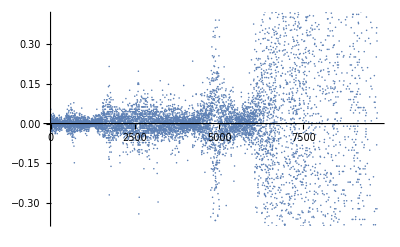

```mathematica
ListPlot[
Differences[apple], Joined->False]
```

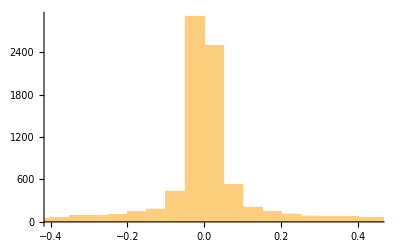

```mathematica
Histogram[Differences[apple]]
```

```mathematica
diffApple = Differences@apple
```

{-0.026786,-0.035714,0.011157,0.0134,0.029014,0.024557,9683,-2.17999,-3.54001,-11.46,2.94,2.25999,-0.839996}
 |  |  |  |

```mathematica
Mean[diffApple]
```

0.019553

```mathematica
Quantity[diffApple, 1/2]
```

Quantity::unkunit: Unable to interpret unit specification 1/2.

Quantity[{-0.026786,-0.035714,0.011157,0.0134,0.029014,9685,-3.54001,-11.46,2.94,2.25999,-0.839996},1/2]
 |  |  |  |

```mathematica
Quantity[diffApple,{ 1/2}]
```

Quantity[{-0.026786,-0.035714,0.011157,0.0134,0.029014,9685,-3.54001,-11.46,2.94,2.25999,-0.839996},{1/2}]
 |  |  |  |

```mathematica
Quantile[diffApple, 1/2]
```

0.

```mathematica
Quantile[diffApple,{ 1/2}]
```

{0.}

```mathematica
Quantile[diffApple,{ 1/2, 3/4}]
```

{0.,0.0446399}

```mathematica
Quantile[diffApple, 1/2]
```

0.

```mathematica
Median[diffApple]
```

0.

```mathematica
FindClusters[diffApple]
```

{{-0.026786,-0.035714,0.011157,0.0134,0.029014,7696,0.360001,0.0200043,-0.319992,0.309998,0.0399933},{1}}
 |  |  |  |

```mathematica
Dendrogram[diffApple]
```

$Aborted

```mathematica
MovingAverage[diffApple, 10]
```

{0.0129457,0.0140628,0.0158485,0.0154014,0.0127228,0.0071429,9674,-0.456,-0.712001,-1.889,-1.201,-1.96,-1.907}
 |  |  |  |

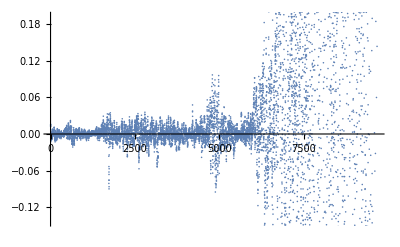

```mathematica
ListPlot[%23]
```

```mathematica
FindPeaks[diffApple]
```

{{9,0.053571},{18,0.029015},{24,0.033485},{71/2,0.017857},{45,0.020086},{50,0.026786},{65,0.026786},{76,0.037943},{80,0.022314},{89,0.031243},{96,0.00892898},{101,0.00669998},{111,0.029014},{120,0.011171},{125,0.024556},{135,0.011157},{143,0.017857},{147,0.017857},{156,0.017857},{159,0.015628},{163,0.013386},{174,0.004471},{182,0.022315},{188,0.00222901},{389/2,0.00222901},{204,0.022314},{207,0.017858},{216,0.017857},{222,0.011157},{233,0.011157},{237,0.011157},{243,0.00892898},{248,0.008928},{258,0.031243},{265,0.015629},{271,0.015629},{276,0.022314},{285,0.011171},{298,0.00447199},{306,0.00222802},{312,0.00222799},{320,0.024557},{329,0.015629},{334,0.00222901},{340,0.008928},{346,0.00670001},{352,0.00892901},{359,0.00222799},{364,0.002242},{366,0.00222901},{372,0.004458},{379,0.008928},{387,0.011158},{393,-0.00222801},{400,0.011157},{405,0.017858},{412,0.008929},{420,0.017857},{425,0.0134},{431,0.020085},{435,0.011171},{444,0.011157},{450,0.011157},{461,0.029014},{470,0.024557},{480,0.037943},{486,0.035714},{490,0.0245571},{498,0.053572},{502,0.031243},{511,0.024557},{514,0.0156291},{522,0.029029},{530,0.040171},{534,0.066958},{539,0.0468709},{544,0.031257},{549,0.0491},{555,0.0245571},{561,0.013386},{567,0.022329},{575,0.017857},{581,0.022329},{590,0.040186},{592,0.026786},{597,0.073671},{603,0.00892901},{608,0.060272},{619,0.049102},{628,0.05135},{637,0.0513451},{641,0.029014},{646,0.040186},{653,0.022314},{661,0.037942},{670,0.00892901},{674,0.00670004},{678,0.015628},{681,0.00668597},{690,0.078129},{698,0.024543},{702,0.046871},{711,0.00670001},{720,0.033472},{727,0.022328},{732,0.031257},{739,0.024557},{745,0.00892898},{747,0.015614},{751,0.00892901},{758,0.00892901},{764,0.017857},{768,0.015628},{776,0.040171},{780,0.024557},{785,0.0134},{792,0.011172},{797,0.00445801},{805,0.024558},{810,0.022314},{815,0.0134},{820,0.013386},{823,0.017857},{833,0.004471},{835,0.00892898},{838,0.00222901},{846,0.022328},{849,0.022314},{859,0.0334859},{864,0.031242},{873,0.037943},{881,0.017857},{889,0.011157},{892,0.011171},{900,0.020085},{906,0.020086},{917,0.026786},{925,0.058028},{937,0.020086},{953,0.024543},{958,0.00224301},{963,0.},{967,0.00670001},{977,0.017858},{991,0.026786},{997,0.00447199},{1006,0.022315},{1011,0.022328},{1020,0.029029},{1027,0.017858},{1035,0.022314},{1043,0.015629},{1046,0.011171},{1052,0.011157},{1054,0.00892895},{1065,0.0134},{1072,0.011157},{1076,0.0134},{1080,0.015628},{1084,0.00670001},{1087,0.015614},{1093,0.},{1098,0.024543},{1103,0.017857},{1107,0.00892898},{1120,0.00447199},{1124,0.024558},{1133,0.008928},{1136,0.022328},{1150,0.020085},{1161,0.006686},{1166,0.002242},{1172,0.00670001},{1175,0.004471},{1182,0.00447199},{1189,0.00668597},{1194,0.00670001},{1206,0.011172},{1210,0.017857},{2433/2,0.},{1219,0.},{1230,0.017857},{1234,0.013386},{1240,0.020085},{1247,0.015614},{1251,0.011157},{1260,0.011157},{1274,0.029014},{1280,0.011157},{1286,0.013386},{1293,0.011158},{1302,0.024557},{1305,0.013385},{1316,0.020086},{1326,0.011158},{1333,0.024557},{1340,0.020086},{1348,0.00892898},{1355,0.015629},{1361,0.031243},{1368,0.029029},{1373,0.053571},{1380,0.0290149},{1389,0.015629},{1396,0.00669897},{1401,0.017857},{1404,0.017857},{1410,0.026786},{1415,0.031257},{1421,0.031243},{1429,0.0134},{1436,0.0334719},{1443,0.015629},{1449,0.0134},{1453,0.013386},{1461,0.031243},{1465,0.029015},{1471,0.017857},{1480,0.0245571},{1483,0.004471},{1490,0.017857},{1497,0.022314},{1502,0.0201},{1505,0.020085},{1511,0.040186},{1515,0.024543},{1521,0.020086},{1525,0.013386},{1528,0.0134},{1537,0.037943},{1544,0.0625},{1550,0.0625},{1553,0.053571},{1567,0.0758799},{1573,0.0647501},{1578,0.04689},{1582,0.03794},{3173/2,0.03125},{3187/2,0.00892997},{1599,0.08929},{1604,0.0357201},{1611,0.06473},{1616,0.03571},{1618,0.02678},{1627,0.05358},{1635,0.06919},{1642,0.0133901},{1650,0.0803499},{1662,0.0223299},{1668,0.08929},{1675,0.0401801},{1677,0.02679},{1686,0.10715},{1696,0.0625},{1703,0.0714301},{1709,0.10267},{1718,0.1384},{1724,0.07143},{1733,0.0446399},{1739,0.21429},{1745,0.14285},{1750,0.07143},{1755,0.0535699},{1761,0.0357201},{1771,0.0803601},{1776,0.11607},{1786,0.06697},{1789,0.09821},{1798,0.02233},{1804,0.05804},{1807,0.05357},{1816,0.0446501},{1820,0.02233},{1823,0.0535699},{1831,0.0625},{1838,0.0178601},{1848,0.0490999},{1854,0.08928},{1862,0.0178601},{1867,0.02679},{1873,0.02678},{1881,0.02679},{1892,0.0625},{1895,0.0446399},{1900,0.03572},{1908,0.02679},{1912,0.0625},{1923,0.00892997},{1934,0.05357},{1943,0.0490999},{1946,0.0446501},{1955,0.02233},{1963,0.0625},{1971,0.0446501},{1975,0.02232},{1992,0.0535699},{1999,0.00446999},{2005,0.03571},{2021,0.04017},{2032,0.02233},{2043,0.05803},{2049,0.02232},{2054,0.02679},{2063,0.05358},{2076,0.02679},{2080,0.0178601},{2085,0.02679},{2091,0.00892997},{2103,0.03126},{2108,0.0491201},{2115,0.03125},{2127,0.02679},{2134,0.0446501},{2141,0.0803601},{2146,0.03571},{2150,0.05357},{2155,0.0401901},{2161,0.0267799},{2170,0.02678},{2175,0.0223299},{2179,0.0446399},{2191,0.05358},{2204,0.03124},{2211,0.00446999},{2216,0.02679},{2223,0.0491201},{2235,0.09376},{2243,0.03571},{2247,0.03126},{2252,0.02678},{2259,0.0357201},{2266,0.0178601},{2275,0.0446401},{2287,0.02679},{2294,0.0714301},{2304,0.02233},{2309,0.0178601},{2314,0.02679},{2318,0.02679},{2322,0.0446399},{2329,0.0178601},{2332,0.02679},{2334,0.0178601},{2340,0.0491},{2346,0.125},{2351,0.0535699},{2358,0.05357},{2364,0.0446501},{2381,0.0535699},{2392,0.06697},{2396,0.03572},{2406,0.0535699},{2413,0.06697},{2419,0.0625},{2424,0.06697},{2435,0.02233},{2439,0.03572},{2449,0.0401801},{2459,0.07142},{2463,0.02679},{2467,0.02232},{2472,0.00892997},{2477,-0.00446999},{2483,0.05358},{2488,0.04018},{2491,0.044643},{2497,0.10268},{2508,0.05357},{2511,0.0446399},{2523,0.02679},{2529,0.05804},{2540,0.0758899},{2547,0.0178601},{2552,0.0714301},{2557,0.10715},{2564,0.0490999},{2567,0.0625},{2571,0.08929},{2574,0.0803599},{2580,0.08482},{2590,0.14731},{2600,0.0625},{2605,0.19643},{2609,0.15178},{2616,0.14731},{2623,0.0669599},{2633,0.0446399},{2638,0.0535699},{2649,0.03571},{2652,0.0803599},{2657,-0.00446999},{2662,0.03124},{2668,0.0223299},{2675,0.08929},{2684,0.0848199},{2694,0.10268},{2702,0.0625},{2708,0.09821},{2712,0.03571},{2720,0.0625},{2726,0.0625},{2731,0.0267799},{2736,0.0446399},{2746,0.09374},{2755,0.00892997},{2758,0.0625},{2764,0.125},{2773,0.0178599},{2779,0.03571},{2788,0.0357101},{2796,0.09376},{2805,0.0625},{2811,0.07143},{2814,0.08482},{2821,0.0357201},{2829,0.08482},{2837,0.08482},{2845,0.0178502},{2850,0.0134001},{2853,0.03124},{2857,0.07143},{2866,0.0625},{2872,0.0803502},{2877,0.0491099},{2883,0.11162},{2889,0.0446398},{2901,0.0357099},{2913,0.0267899},{2920,0.03571},{2924,0.0535699},{2933,0.0446401},{2944,0.0446399},{2955,0.0223299},{2970,0.07143},{2974,0.0446399},{2984,0.0625},{2989,0.00893009},{2993,0.0446399},{3001,0.125},{3007,0.09822},{3015,0.08929},{3024,0.08929},{3031,0.0357101},{3036,0.03124},{3044,0.06697},{3050,0.0178599},{3056,0.0892899},{3070,0.0267801},{3074,0.0625},{3080,0.0134001},{3086,0.04018},{3091,0.0401801},{3094,0.03571},{3098,0.0535699},{3111,0.0357201},{3114,0.0446401},{3120,0.0625},{3128,0.05357},{3133,0.0446399},{3138,0.05358},{3145,0.0803499},{3149,0.0625001},{3154,0.0490999},{3166,0.03126},{3172,0.0625},{3178,0.0178499},{3180,0.0178601},{3185,0.0446399},{3200,0.0267891},{3211,0.031258},{3214,0.017858},{3221,0.017857},{3225,0.017858},{3233,0.017857},{3236,0.035714},{3245,0.026785},{3253,0.160716},{3257,0.0892891},{3261,0.07143},{3265,0.0446399},{3275,0.07143},{3280,0.0178601},{3288,0.02679},{3295,0.02232},{3302,0.0446461},{3309,0.0803601},{3316,0.0133799},{3321,0.125},{3332,0.10714},{3342,0.0357201},{3351,0.04018},{3356,0.03125},{3363,0.00446999},{3369,0.02679},{3385,0.0446399},{3391,0.09821},{3402,0.05357},{3406,0.0178601},{3412,0.00892901},{3418,0.017857},{3423,0.022329},{3428,0.022872},{3438,0.0491149},{3446,0.10714},{3451,0.06473},{3459,0.0357101},{3471,0.0245501},{3478,0.02008},{3484,0.03124},{3494,0.00892997},{3498,0.14732},{3501,0.06697},{3503,0.08929},{3510,0.05804},{3516,0.0379601},{3522,0.0535699},{3526,0.049},{3534,0.0312799},{3540,0.02228},{3547,0.05357},{3550,0.0669999},{3553,0.00900006},{3555,0.00899994},{3565,0.10943},{3570,0.0224301},{3581,0.0535699},{3585,0.0535699},{3598,0.04457},{3604,0.04457},{3614,0.0647199},{3620,0.03572},{3625,0.07143},{3629,0.0445801},{3635,0.0535699},{3646,0.058},{3650,0.09385},{3656,0.04914},{3665,0.049},{3670,0.0239999},{3676,0.10714},{3688,0.0581399},{3693,0.04014},{3699,0.058},{3706,0.0312899},{3715,0.0245999},{3721,0.02672},{3731,0.03571},{3741,0.0132899},{3746,0.0535699},{3757,0.02443},{3769,0.0380001},{3773,0.0581399},{3778,0.0401499},{3786,0.05571},{3792,0.0668499},{3797,0.00891995},{3808,0.01115},{3814,0.0959899},{3817,0.0535699},{3826,0.04017},{3834,0.0312099},{3840,0.0267181},{3845,0.053568},{3864,0.009},{3868,0.00885701},{3871,0.049143},{3874,0.033429},{3879,0.058},{3883,0.009},{3887,0.011142},{3891,0.022286},{3898,0.062571},{3905,0.0357181},{3912,0.017857},{3916,0.022428},{3919,0.033464},{3925,0.013429},{3929,0.013429},{3935,0.026857},{3942,-0.00457102},{3949,0.142857},{3955,0.035714},{3963,0.031285},{3971,0.040286},{3975,0.022286},{3977,0.026143},{3990,0.049142},{4001,0.087143},{4008,0.042429},{4010,0.035715},{4018,0.},{4024,0.044714},{4026,0.040143},{4032,0.011143},{4039,0.026857},{4044,0.035714},{4058,0.044571},{4066,0.026857},{4071,0.017857},{4078,0.011142},{4085,0.00442803},{4090,0.026714},{4097,0.055714},{4102,0.015536},{4108,0.017857},{4115,0.00671399},{4119,0.040142},{4124,0.067},{4128,0.031285},{4138,0.015571},{4141,0.017857},{4145,0.00457102},{4149,0.},{4153,0.017857},{4161,0.009},{4165,0.013428},{4168,0.006589},{4173,0.002285},{4176,0.00228602},{4180,0.030134},{4185,-0.00214201},{4192,0.022286},{4197,0.069143},{4215,0.234304},{4224,0.02891},{4233,0.022285},{4239,0.040143},{4245,0.017858},{4252,0.026715},{4255,0.014571},{4261,0.033428},{4268,0.013429},{4273,0.049143},{4281,0.026857},{4286,0.015714},{4290,0.00885695},{4295,0.009},{4300,0.006715},{4307,0.013428},{4318,0.1115},{4325,0.044643},{4331,0.013429},{4343,0.024571},{4349,0.031142},{4355,0.042285},{4359,0.046965},{4364,0.073607},{4369,0.021196},{4373,0.066858},{4377,0.02},{4389,0.0424299},{4395,0.009},{4401,0.03795},{4412,0.0312799},{4418,0.024643},{4426,0.0357149},{4431,0.017858},{4436,0.015714},{4442,0.0447201},{4446,0.07371},{4452,0.10929},{4461,0.05357},{4466,0.06471},{4469,0.05143},{4474,0.05143},{4478,0.08471},{4485,0.105},{4489,0.11161},{4500,0.0470001},{4512,0.15389},{4518,0.0290101},{4520,0.038},{4523,0.0692799},{4527,0.02457},{4537,0.06028},{4543,0.0334301},{4548,0.07824},{4552,0.03572},{4556,0.06257},{4563,0.10485},{4571,0.0737901},{4573,0.11607},{4585,0.0401399},{4597,0.04685},{4603,0.04474},{4613,0.04241},{4619,0.05129},{4623,0.05586},{4628,0.07582},{4632,0.03566},{4639,0.0322901},{4648,0.17179},{4652,0.12728},{4659,0.06243},{4663,0.03128},{4669,0.09157},{4673,0.06243},{4683,0.0669999},{4692,0.10043},{4698,0.16737},{4705,0.04915},{4711,0.09814},{4722,0.154},{4737,0.12057},{4745,0.10057},{4747,0.05143},{4760,0.12057},{4768,0.19872},{4771,0.16071},{4778,0.08042},{4784,0.28786},{4795,0.07815},{4801,0.25443},{4810,0.0758498},{4814,0.16071},{4822,0.32577},{4826,0.16071},{4830,0.34598},{4837,0.19204},{4846,0.21657},{4851,0.25228},{4856,0.0915799},{4862,0.51328},{4869,0.125},{4877,0.33029},{4884,0.35943},{4889,0.23443},{4895,0.38843},{4900,0.27914},{4908,0.0803401},{4913,0.17186},{4926,0.1875},{4940,0.36154},{4943,0.17414},{4952,0.192},{4960,0.17414},{4965,0.13828},{4967,0.17868},{4974,0.05358},{4980,0.20986},{4984,0.18757},{4991,0.17857},{4994,0.25443},{5001,0.38829},{5006,0.09372},{5015,0.00885999},{5020,0.14743},{5026,0.0625},{5034,0.12957},{5042,0.06243},{5049,0.05814},{5054,0.04029},{5059,0.05357},{5069,0.06686},{5075,0.10714},{5081,0.10257},{5085,0.13393},{5092,0.15171},{5098,0.0669999},{5105,0.04028},{5111,0.049},{5116,0.08043},{5122,0.0669999},{5129,0.10714},{5142,0.15422},{5148,0.21286},{5154,0.10786},{5167,0.06572},{5172,0.01429},{5182,0.06643},{5191,0.10572},{5199,0.04643},{5206,0.13},{5221,0.0542799},{5226,0.01071},{5231,0.015},{5237,0.0577899},{5242,0.0514301},{5249,0.05221},{5253,0.05143},{5256,0.02572},{5261,0.0642799},{5266,0.0657101},{5271,0.08857},{5275,0.05786},{5281,0.07358},{5284,0.03572},{5289,0.0442799},{5293,0.07357},{5297,0.10929},{5304,0.09714},{5314,0.0435799},{5319,0.04143},{5322,0.09999},{5333,0.12143},{5336,0.0857099},{5341,0.07285},{5349,0.06785},{5357,0.08857},{5362,0.125},{5365,0.0385801},{5372,0.03714},{5382,0.0564301},{5385,0.0821401},{5393,0.05286},{5402,0.06786},{5409,0.13571},{5413,0.11929},{5419,0.0614301},{5424,0.01571},{5428,-0.00428009},{5435,0.04},{5445,0.04714},{5449,0.085},{5453,0.0699999},{5462,0.05214},{5465,0.0485801},{5471,0.053575},{5477,0.04143},{5489,0.00357008},{5493,0.0142801},{5499,0.0235699},{5503,0.02071},{5506,0.02072},{5512,0.00928998},{5517,0.037143},{5528,0.0521401},{5534,0.0378599},{5542,0.0507101},{5547,0.05858},{5551,0.0221499},{5559,0.0378599},{5564,0.01643},{5568,0.025},{5574,0.0335701},{5579,0.00928998},{5591,0.03215},{5595,0.02143},{5605,0.04285},{5608,0.01643},{5612,0.02572},{5616,0.00428998},{5622,0.03572},{5632,0.00572002},{5636,0.03143},{5649,0.026429},{5658,0.11714},{5671,0.02786},{5679,0.02071},{5689,0.0664201},{5694,0.02214},{5701,0.0528599},{5709,0.07357},{5715,0.07357},{5719,0.05714},{5728,0.03429},{5733,0.04928},{5739,0.0507201},{5745,0.01714},{5749,0.0385699},{5753,0.0542799},{5760,0.04357},{5764,0.0799999},{5770,0.04785},{5775,0.0335701},{5781,0.0800101},{5785,0.0185701},{5787,0.00856996},{5792,0.05643},{5800,0.06214},{5804,0.05714},{5809,0.01429},{5812,0.0592899},{5821,0.04286},{5830,0.0550001},{5841,0.0321399},{5853,0.05857},{5864,0.06286},{5869,0.11286},{5883,0.09786},{5890,0.05857},{5894,0.0364301},{5897,0.19},{5902,0.00356996},{5911,0.03643},{5915,0.06143},{5925,0.0764199},{5933,0.07358},{5939,0.14643},{5944,0.05},{5949,0.00286007},{5959,0.23928},{5967,0.08357},{5973,0.0357101},{5977,0.0871501},{5983,0.06214},{5989,0.115},{5993,0.0978599},{5997,0.04214},{6003,0.08214},{6012,0.0457201},{6017,0.0907199},{6023,0.37358},{6032,0.16643},{6037,0.12928},{6042,0.0500002},{6050,0.44143},{6063,0.08286},{6074,0.0728502},{6082,0.33572},{6086,0.31},{6097,0.20857},{6103,0.14},{6108,0.27},{6113,0.21},{6120,0.14571},{6129,0.15285},{6137,0.15},{6143,0.17572},{6153,0.23857},{6155,0.21143},{6162,0.13428},{6173,0.24428},{6175,0.31572},{6187,0.10429},{6191,0.16143},{6196,0.0985703},{6204,0.21143},{6207,0.0885701},{6211,0.34286},{6224,0.06286},{6232,0.3},{6244,0.10429},{6248,0.36857},{6251,0.21857},{6257,0.20429},{6261,0.18571},{6266,0.18143},{6275,0.64143},{6279,0.39},{6289,0.35001},{6299,0.381431},{6305,0.31857},{6309,0.54003},{6323,0.1986},{6330,0.4086},{6335,0.6871},{6343,0.225801},{6348,0.4243},{6355,0.17286},{6359,0.419291},{6364,0.320029},{6369,0.0871506},{6377,0.355721},{6389,0.51715},{6394,0.86286},{6404,0.282861},{6408,0.28285},{6421,0.0128603},{6429,0.14143},{6433,0.342859},{6438,0.31357},{6443,0.25286},{6448,0.24572},{6453,0.42142},{6460,0.0928597},{6467,0.91429},{6474,0.33857},{6485,0.35858},{6493,0.13429},{6499,0.44283},{6505,0.2243},{6510,0.2128},{6513,0.392799},{6520,0.1857},{6526,0.29},{6531,0.637199},{6539,0.0943003},{6545,0.2772},{6554,0.3042},{6558,0.3243},{6569,0.4157},{6573,0.12},{6580,0.5671},{6585,1.0143},{6595,0.1428},{6598,0.0799999},{6605,0.2857},{6614,0.471499},{6623,0.2672},{6627,0.271501},{6629,0.228499},{6634,0.3414},{6643,0.1214},{6659,0.498899},{6666,0.444301},{6676,0.28},{6682,0.631401},{6685,0.418598},{6695,0.655701},{6698,0.335701},{6706,0.8442},{6713,0.5229},{6718,0.5357},{6722,1.2485},{6729,0.485701},{6734,0.3986},{6740,0.764301},{6746,1.0372},{6757,0.23},{6759,0.3585},{6764,0.700001},{6768,0.409801},{6773,0.9228},{6780,0.4529},{6784,1.6857},{6790,0.4214},{6799,2.3143},{6809,0.7728},{6814,0.812901},{6819,0.3314},{6826,0.9571},{6837,1.1643},{6843,0.1786},{6852,0.454199},{6858,0.6057},{6865,0.234301},{6871,0.992899},{6874,0.412901},{6879,1.0943},{6887,0.894299},{6893,0.861401},{6895,0.5886},{6907,1.0172},{6910,0.8643},{6915,0.8643},{6922,0.672899},{6932,0.751501},{6939,0.6057},{6947,0.655701},{6953,0.5914},{6957,1.0343},{6960,0.719999},{6967,0.452799},{6972,0.6057},{6977,0.4},{6984,0.8543},{6992,0.33},{6996,0.155701},{7001,0.110001},{7007,0.1485},{7013,0.974298},{7017,0.459999},{7020,1.2},{7029,1.9228},{7032,0.5628},{7036,0.7686},{7040,1.1172},{7052,0.9028},{7055,0.2529},{7059,1.4815},{7064,0.5057},{7068,0.8171},{7072,0.4672},{7077,0.0813999},{7085,0.7714},{7098,0.79},{7109,0.4657},{7113,0.35},{7120,0.4715},{7126,0.4},{7130,0.7882},{7135,0.6057},{7139,0.8671},{7147,0.574301},{7152,0.4643},{7156,0.5443},{7161,0.5557},{7168,0.690001},{7178,0.6043},{7183,1.1829},{7201,0.514299},{7205,0.52},{7218,0.6586},{7223,0.747099},{7229,0.394299},{7231,0.434299},{7235,0.2286},{7239,0.4443},{7245,0.412899},{7249,0.291399},{7255,0.5371},{7262,0.9585},{7270,0.540199},{7276,0.569401},{7286,1.2714},{7293,0.564299},{7300,1.0171},{7304,0.3514},{7310,0.8514},{7317,0.0356998},{7321,1.1328},{7332,0.991499},{7337,0.4683},{7341,0.200001},{7347,1.3014},{7351,0.7607},{7358,0.4814},{7364,0.5077},{7375,0.6243},{7379,1.1772},{7391,0.515797},{7394,0.607098},{7396,0.4935},{7399,0.360001},{7406,0.465698},{7411,2.09},{7417,1.0057},{7424,2.59},{7437,1.3202},{7450,1.08},{7464,1.4335},{7475,0.683399},{7482,0.657101},{7493,0.618599},{7504,1.0328},{7514,0.907097},{7516,1.1228},{7527,1.4714},{7535,1.7758},{7541,0.195698},{7547,0.740002},{7559,1.1328},{7561,0.947102},{7563,0.866398},{7567,0.75},{7572,0.400002},{7581,0.285},{7584,0.154301},{7589,1.0014},{7594,0.904999},{7603,1.5328},{7609,0.815701},{7613,0.7686},{7618,0.332802},{7626,0.7542},{7630,1.0628},{7636,0.760002},{7642,1.2328},{7646,0.938602},{7655,0.00569916},{7659,0.532902},{7665,1.1837},{7672,0.2743},{7677,0.264297},{7683,0.532898},{7691,1.4886},{7701,0.834301},{7708,1.2315},{7710,0.812901},{7714,1.0842},{7724,1.2686},{7734,0.895699},{7742,1.43},{7750,2.4514},{7753,1.4085},{7759,0.812901},{7768,1.59},{7772,0.354198},{7783,2.7157},{7793,1.8428},{7796,0.584301},{7801,0.808502},{7809,1.3671},{7814,1.0714},{7819,1.2857},{7826,0.422798},{7833,1.9629},{7843,0.655701},{7850,0.698498},{7856,3.75},{7867,2.3558},{7874,1.8186},{7879,1.3785},{7890,3.0686},{7893,2.2185},{7898,1.5614},{7903,2.7257},{7913,4.2243},{7919,7.1029},{7924,0.550003},{7930,0.191498},{7937,4.4143},{7942,1.4258},{7948,1.2328},{7956,1.6643},{7965,2.1357},{7974,0.867203},{7986,2.2471},{7989,1.13},{7995,1.1857},{8000,2.4343},{8005,1.7797},{8010,1.39},{8017,1.8843},{8027,2.30569},{8031,1.4485},{8040,2.1475},{8044,3.4557},{16099/2,0.},{8054,1.1173},{8058,1.32999},{8064,5.436},{8068,2.5757},{8079,1.6524},{8084,2.1528},{8092,3.2262},{8099,0.915703},{8103,2.8815},{8110,1.4214},{8118,1.5529},{8130,0.881504},{8137,0.702801},{8139,0.878597},{8144,1.7229},{8148,1.3114},{8160,1.2443},{8168,1.1629},{8173,1.845},{8178,1.5328},{8188,1.3814},{8195,0.947098},{8201,0.478798},{8205,0.539299},{8217,1.8129},{8224,0.936798},{8233,3.0743},{8236,0.971401},{8241,0.987198},{8247,3.1729},{8262,1.4445},{8275,3.3185},{8281,1.6015},{8287,0.8069},{8295,1.7817},{8305,0.959999},{8313,1.0751},{8322,1.7943},{8329,0.915703},{8334,0.438599},{8339,3.01},{8344,0.928596},{8349,0.488899},{8354,1.5672},{8357,1.2},{8371,1.33},{8383,1.4743},{8391,0.738594},{8396,0.665703},{8400,0.902802},{8406,0.7015},{8412,0.982903},{8422,6.1457},{8429,1.19711},{8434,1.0411},{8438,1.24149},{8444,1.6428},{8449,1.27},{8453,1.4757},{8458,0.919998},{8467,1.08},{8472,1.938},{8477,1.23},{8484,2.47},{8499,1.27},{8503,1.37},{8509,1.241},{8518,3.01},{8523,0.720001},{8527,1.58},{8530,2.88},{8538,2.05},{8547,2.71},{8552,1.63},{8556,1.4},{8564,1.57},{8571,2.155},{8577,1.3},{8581,1.72},{8588,3.24},{8593,1.98},{8601,4.14},{8610,2.85},{8614,6.17},{8624,2.86},{8631,3.505},{8636,0.62999},{8641,0.540001},{8647,2.09},{8656,3.12},{8660,2.03},{8663,0.959999},{8672,1.70999},{8679,3.8},{8684,2.36},{8688,2.93999},{8693,1.33},{8696,2.425},{8701,0.159988},{8706,1.46001},{8710,0.68},{8714,1.01},{8716,1.08},{8721,1.175},{8727,3.21},{8731,1.68999},{8739,0.610001},{8748,4.2},{8753,1.2},{8760,5.95},{8770,2.42},{8779,0.919998},{8786,0.799995},{8791,2.62},{8801,3.58},{8804,4.71999},{8819,3.6},{8830,3.83},{8838,0.849998},{8843,1.38},{8854,1.57},{8862,5.12},{8867,3.25},{8870,1.87},{8873,0.990005},{8878,2.65},{8888,3.84},{8898,2.06001},{8907,2.49},{8918,1.6},{8923,0.219994},{8932,1.54},{8937,0.629997},{8941,3.36},{8948,1.72},{8955,0.709999},{8963,0.410004},{8966,0.810005},{8973,1.2},{8978,0.739998},{8982,1.92},{8991,6.28},{8998,1.61},{9004,1.3},{9018,1.},{9025,3.82},{9031,1.07},{9035,0.860001},{9043,1.99001},{9053,1.05},{9058,-0.18},{9063,1.57001},{9070,2.88},{9086,1.82999},{9097,0.740005},{9104,1.3},{9110,0.959999},{9116,1.91},{9121,7.4},{9130,1.73001},{9134,0.979996},{9140,2.79999},{9150,1.47},{9155,1.58},{9159,2.92},{9164,1.07001},{9177,1.37},{9182,2.93001},{9187,4.04999},{9195,2.28999},{9205,2.27},{9216,4.06999},{9223,2.10001},{9233,2.03},{9240,1.81999},{9247,7.09},{9255,2.37001},{9261,2.56999},{9265,1.61},{9274,2.87},{9278,1.60001},{9285,2.59},{9292,1.91},{9299,2.89},{9308,5.64},{9313,4.39},{9325,3.16},{9331,2.37001},{9338,3.3},{9343,2.45},{9355,1.97},{9360,1.81},{9362,2.91},{9372,0.459991},{9376,6.53999},{9383,5.62001},{9389,3.47},{9393,1.21001},{9398,3.03999},{9409,7.83},{9415,3.22},{9419,3.2},{9424,2.42},{9435,7.47},{9445,1.73999},{9450,1.2},{9456,3.37001},{9463,1.05},{9469,0.809998},{9475,1.34},{9481,2.61},{9484,3.14999},{9493,1.82001},{9498,11.21},{9510,4.25999},{9518,3.28},{9526,5.52},{9528,5.34},{9538,4.53},{9546,3.09999},{9549,7.66},{9551,4.78999},{9554,3.28999},{9558,4.71001},{9562,5.56},{9567,6.17999},{9573,4.61},{9581,6.7},{9591,1.84999},{9599,10.34},{9607,2.82001},{9612,3.07001},{9622,10.57},{9638,1.91},{9643,1.82001},{9648,5.98999},{9656,6.92999},{9664,2.78},{9668,3.10001},{9675,3.88},{9684,9.85001},{9689,0.0399933},{9693,2.94}}

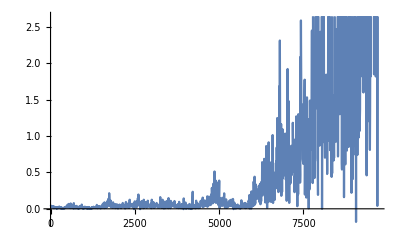

```mathematica
ListPlot[%25,Joined->True]
```

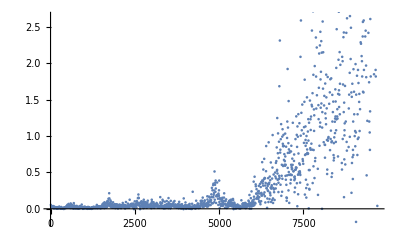

```mathematica
ListPlot[%25,Joined->False]
```

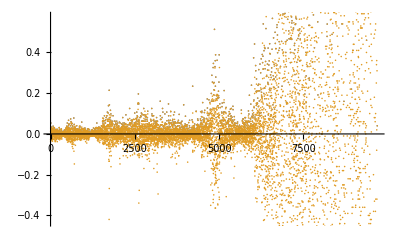

```mathematica
ListPlot[{%25, diffApple},Joined->False]
```

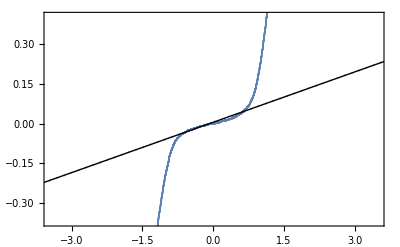

```mathematica
QuantilePlot[diffApple]
```

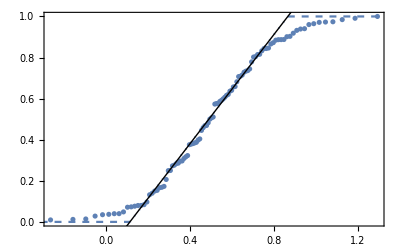

```mathematica
QuantilePlot[RandomVariate[UniformDistribution[{0,1}],100]]
```

```mathematica
QuantilePlot[
Differences@
Map[Last,
FinancialData["NASDAQ:GOOG", "Price" All]]]
```

FinancialData::notdate: Price All is not a valid date range for FinancialData.

Last::normal: Nonatomic expression expected at position 1 in Last[NASDAQ:GOOG].

FinancialData::notent: Last[NASDAQ:GOOG] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Missing[UnknownEntity,{Financial,$Failed}]].

QuantilePlot::ldata: Differences[Missing[UnknownEntity,{Financial,$Failed}]] is not a valid dataset, distribution, or a valid list of datasets and distributions.

QuantilePlot[Differences[Missing[UnknownEntity,{Financial,$Failed}]]]

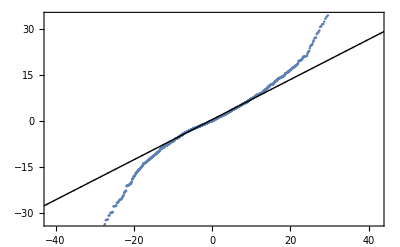

```mathematica
QuantilePlot[
Differences@
Map[Last,
FinancialData["NASDAQ:GOOG", "Price" ,All]]]
```

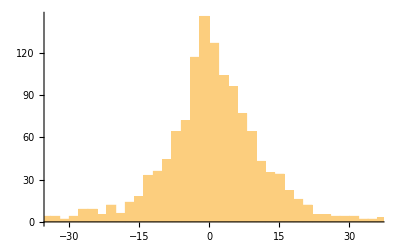

```mathematica
Histogram[
Differences@
Map[Last,
FinancialData["NASDAQ:GOOG", "Price" ,All]]]
```

```mathematica
Kurtosis[
Differences@
Map[Last,
FinancialData["NASDAQ:GOOG", "Price" ,All]]]
```

10.9544

```mathematica
Kurtosis[
Differences@
Map[Last,
FinancialData["NASDAQ:AAPL", "Price" ,All]]]
```

49.9272

```mathematica
{Kurtosis, Skewness, Mean, Median, QuantilePlot, Histogram, Variance, Entropy, Min, Max}
```

{Kurtosis,Skewness,Mean,Median,QuantilePlot,Histogram,Variance,Entropy,Min,Max}

```mathematica
{"NASDAQ:GOOG", "NASDAQ:AAPL","NYSE:GE","NASDAQ:MSFT","^DJI","NASDAQ:EBAY","NYSE:IBM","NASDAQ:INTC","NASDAQ:FB","NASDAQ:AMZN"}
```

{NASDAQ:GOOG,NASDAQ:AAPL,NYSE:GE,NASDAQ:MSFT,^DJI,NASDAQ:EBAY,NYSE:IBM,NASDAQ:INTC,NASDAQ:FB,NASDAQ:AMZN}

```mathematica
Table[{a,b}, {a, 1, 10,1}, {b,{c,d,e}}]
```

{{{1,c},{1,d},{1,e}},{{2,c},{2,d},{2,e}},{{3,c},{3,d},{3,e}},{{4,c},{4,d},{4,e}},{{5,c},{5,d},{5,e}},{{6,c},{6,d},{6,e}},{{7,c},{7,d},{7,e}},{{8,c},{8,d},{8,e}},{{9,c},{9,d},{9,e}},{{10,c},{10,d},{10,e}}}

```mathematica
Table[{a,b}, {a,{1,2,3}}, {b,{c,d,e}}]
```

{{{1,c},{1,d},{1,e}},{{2,c},{2,d},{2,e}},{{3,c},{3,d},{3,e}}}

```mathematica
Table[
func->func@
Differences@
Map[Last,
FinancialData[security, "Price" ,All]],
{security,{"NASDAQ:GOOG", "NASDAQ:AAPL","NYSE:GE","NASDAQ:MSFT","^DJI","NASDAQ:EBAY","NYSE:IBM","NASDAQ:INTC","NASDAQ:FB","NASDAQ:AMZN"}},
{func,{Kurtosis,Skewness,Mean,Median,QuantilePlot,Histogram,Variance,Entropy,Min,Max}}]
```

$Aborted

```mathematica
Table[
func->func@
Differences@
Map[Last,
FinancialData[security, "Price" ,All]],
{security,{"NASDAQ:GOOG", "NASDAQ:AAPL"}},
{func,{Kurtosis,Skewness,Mean,Median,QuantilePlot,Histogram,Variance,Entropy,Min,Max}}]
```

{{Kurtosis→10.9544,Skewness→-0.315727,Mean→0.484839,Median→0.400024,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→163.831,Entropy→(-150 Log[2]-24 Log[3])/1283+Log[1283],Min→-99.1,Max→93.08},{Kurtosis→49.9272,Skewness→-0.914915,Mean→0.019553,Median→0.,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→0.832344,Entropy→1/9695(-1188 Log[2]-735 Log[3]-476 Log[4]-410 Log[5]-246 Log[6]-245 Log[7]-144 Log[8]-90 Log[9]-120 Log[10]-88 Log[11]-144 Log[12]-78 Log[13]-112 Log[14]-120 Log[15]-96 Log[16]-51 Log[17]-72 Log[18]-57 Log[19]-60 Log[20]-63 Log[21]-110 Log[22]-96 Log[24]-25 Log[25]-52 Log[26]-54 Log[27]-84 Log[28]-58 Log[29]-60 Log[30]-32 Log[32]-33 Log[33]-34 Log[34]-35 Log[35]-36 Log[36]-37 Log[37]-38 Log[38]-78 Log[39]-84 Log[42]-46 Log[46]-50 Log[50]-57 Log[57]-60 Log[60]-69 Log[69]-73 Log[73]-368 Log[368])+Log[9695],Min→-15.73,Max→11.21}}

```mathematica
Column@
Table[
func->func@
Differences@
Map[Last,
FinancialData[security, "Price" ,All]],
{security,{"NASDAQ:GOOG", "NASDAQ:AAPL"}},
{func,{Kurtosis,Skewness,Mean,Median,QuantilePlot,Histogram,Variance,Entropy,Min,Max}}]
```

{Kurtosis→10.9544,Skewness→-0.315727,Mean→0.484839,Median→0.400024,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→163.831,Entropy→(-150 Log[2]-24 Log[3])/1283+Log[1283],Min→-99.1,Max→93.08}
{Kurtosis→49.9272,Skewness→-0.914915,Mean→0.019553,Median→0.,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→0.832344,Entropy→1/9695(-1188 Log[2]-735 Log[3]-476 Log[4]-410 Log[5]-246 Log[6]-245 Log[7]-144 Log[8]-90 Log[9]-120 Log[10]-88 Log[11]-144 Log[12]-78 Log[13]-112 Log[14]-120 Log[15]-96 Log[16]-51 Log[17]-72 Log[18]-57 Log[19]-60 Log[20]-63 Log[21]-110 Log[22]-96 Log[24]-25 Log[25]-52 Log[26]-54 Log[27]-84 Log[28]-58 Log[29]-60 Log[30]-32 Log[32]-33 Log[33]-34 Log[34]-35 Log[35]-36 Log[36]-37 Log[37]-38 Log[38]-78 Log[39]-84 Log[42]-46 Log[46]-50 Log[50]-57 Log[57]-60 Log[60]-69 Log[69]-73 Log[73]-368 Log[368])+Log[9695],Min→-15.73,Max→11.21}

```mathematica
Column@
Table[
func->func@
Differences@
Map[Last,
FinancialData[security, "Price" ,All]],
{security,{"NASDAQ:GOOG", "NASDAQ:AAPL"}},
{func,{Kurtosis,Skewness,Mean,Median,QuantilePlot,Histogram,Variance,N[Entropy[#]]&,Min,Max}}]
```

{Kurtosis→10.9544,Skewness→-0.315727,Mean→0.484839,Median→0.400024,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→163.831,(N[Entropy[#1]]&)→7.05537,Min→-99.1,Max→93.08}
{Kurtosis→49.9272,Skewness→-0.914915,Mean→0.019553,Median→0.,QuantilePlot→-Graphics-,Histogram→-Graphics-,Variance→0.832344,(N[Entropy[#1]]&)→7.73119,Min→-15.73,Max→11.21}

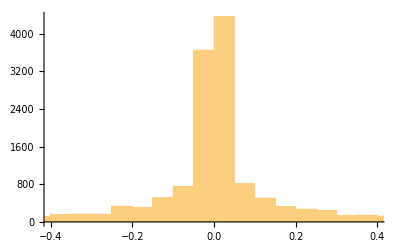
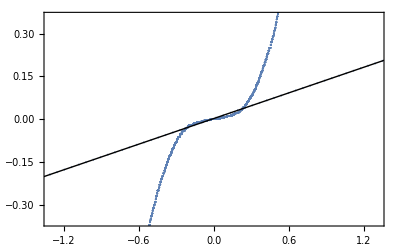
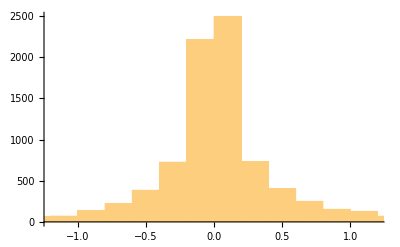
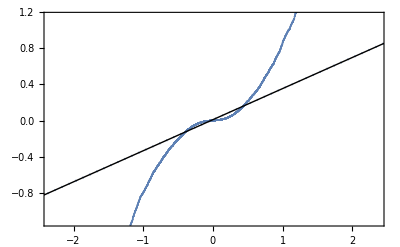
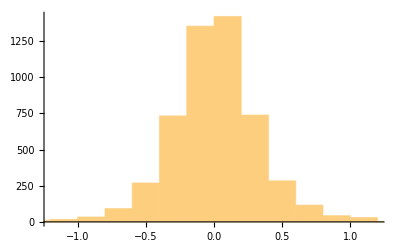
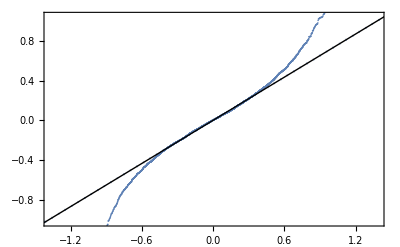
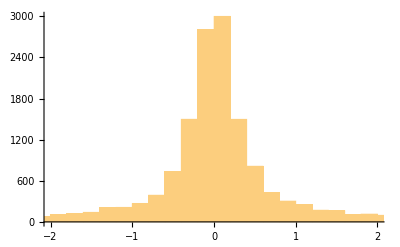
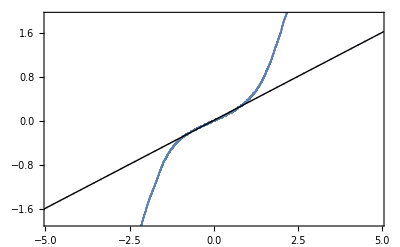
{Kurtosis→10.9544,Skewness→-0.315727,Mean→0.484839,Median→0.400024,Variance→163.831,Min→-99.1,Max→93.08,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→49.9272,Skewness→-0.914915,Mean→0.019553,Median→0.,Variance→0.832344,Min→-15.73,Max→11.21,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→29.0065,Skewness→-0.239112,Mean→0.000646884,Median→0.,Variance→0.112409,Min→-4.7,Max→4.063,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→21.5391,Skewness→0.020063,Mean→0.0154051,Median→0.000799,Variance→0.388758,Min→-7.1562,Max→6.6,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→24.982,Skewness→0.0913104,Mean→0.00702238,Median→0.00419998,Variance→0.142758,Min→-4.1498,Max→5.61,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→30.7723,Skewness→-0.971542,Mean→0.00742422,Median→0.,Variance→1.54969,Min→-21.75,Max→13.,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→63.5076,Skewness→-1.65699,Mean→0.00384354,Median→0.,Variance→0.273564,Min→-13.5315,Max→6.25,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→75.2534,Skewness→-3.31669,Mean→0.0848592,Median→0.0699997,Variance→4.97687,Min→-41.24,Max→16.27,Histogram→-Graphics-,QuantilePlot→-Graphics-}
{Kurtosis→50.7095,Skewness→-0.115747,Mean→0.344159,Median→0.0298996,Variance→102.222,Min→-139.36,Max→128.52,Histogram→-Graphics-,QuantilePlot→-Graphics-}

```mathematica
Column@
Table[
func->func@
Differences@
Map[Last,
FinancialData[security, "Price" ,All]],
{security,
{"NASDAQ:GOOG", "NASDAQ:AAPL","NYSE:GE",
"NASDAQ:MSFT","NASDAQ:EBAY","NYSE:IBM",
"NASDAQ:INTC","NASDAQ:FB","NASDAQ:AMZN"}},
{func,
{Kurtosis,Skewness,Mean,Median,Variance,Min,Max, Histogram,QuantilePlot}}]
```

```mathematica
Histogram@
Differences@
Map[Last,
FinancialData["^IXIC", "Price", All]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[$Failed].

Histogram::ldata: Differences[$Failed] is not a valid dataset or list of datasets.

Histogram[Differences[$Failed]]

```mathematica
Histogram@
Differences@
Map[Last,
FinancialData["^IXIC", "Price", All]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[$Failed].

Histogram::ldata: Differences[$Failed] is not a valid dataset or list of datasets.

Histogram[Differences[$Failed]]

```mathematica
Differences@
Map[Last,
FinancialData["^IXIC", "Price", All]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[$Failed].

Differences[$Failed]

```mathematica
FinancialData["^IXIC", "Price", All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
Correlation[{a,b},{x,y}]
```

((a-b) (Conjugate[x]-Conjugate[y]))/(√((a-b) (Conjugate[a]-Conjugate[b])) √((x-y) (Conjugate[x]-Conjugate[y])))

```mathematica
FinancialData["^IXIC", "Price", All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

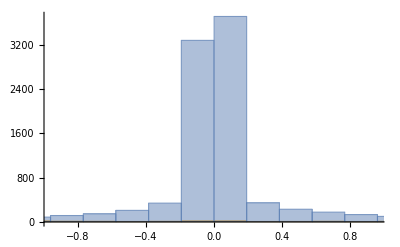

```mathematica
Histogram[{
Differences@
Map[Last,
FinancialData["NASDAQ:GOOG", "Price" ,All]],
Differences@
Map[Last,
FinancialData["NASDAQ:AAPL", "Price" ,All]]}]
```

```mathematica
FinancialData["^IXIC", "Price", All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

```mathematica
"plot in world map""country group"Manipulate[Graphics[({If[CountryData[#1,cl],Directive[Orange,EdgeForm[Brown]],LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{cl,{->TakeLargest[5]},"country group"},Dynamic[CanonicalName[CountryData["Classes"]],SynchronousUpdating->False],ControlType->PopupMenu},{{prop,"Population","country property"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

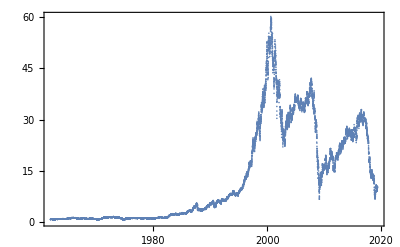

```mathematica
DateListPlot[
FinancialData["NYSE:GE", "Price", All],
Joined->False]
```

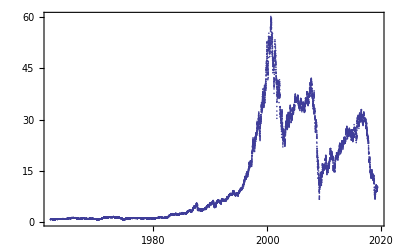

```mathematica
DateListPlot[FinancialData["NYSE:GE","Price",All],PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[1.365]],Joined->False]
```

```mathematica
DateListPlot[FinancialData["NYSE:GE","Price",All],PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[1.365]],Joined->False]
```

-Graphics-

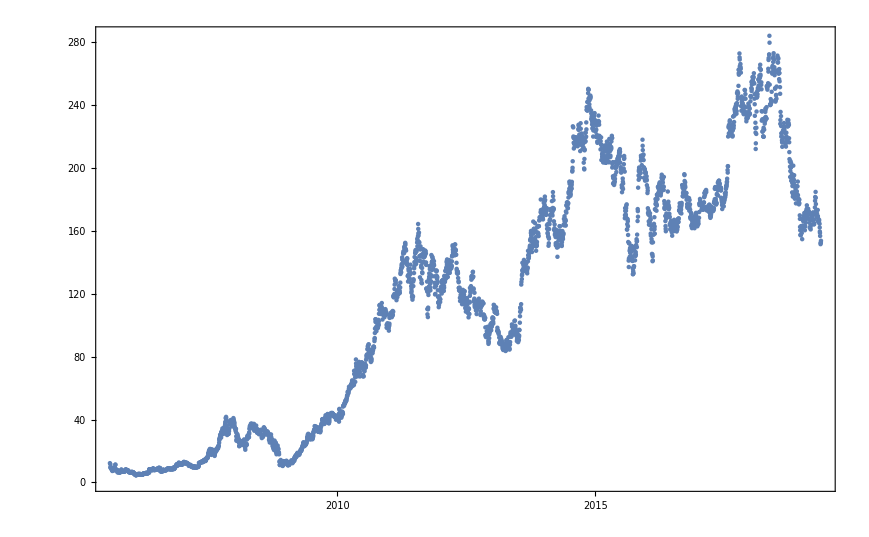

```mathematica
DateListPlot[
FinancialData["NASDAQ:BIDU", "Price", All],
Joined->False]
```

```mathematica
MovingAverage[FinancialData["NASDAQ:BIDU", "Price", All], 7]
```

MovingAverage::vecmat: Argument {{{2005,8,5},12.254},{{2005,8,8},11.55},{{2005,8,9},9.61},{{2005,8,10},9.175},«43»,{{2005,10,12},6.36},{{2005,10,13},6.222},{{2005,10,14},6.727},«3418»} at position 1 is neither a non-empty vector nor a non-empty matrix.

MovingAverage[{{{2005,8,5},12.254},{{2005,8,8},11.55},{{2005,8,9},9.61},3462,{{2019,5,14},152.39},{{2019,5,15},152.5},{{2019,5,16},153.7}},7]
 |  |  |  |

```mathematica
FinancialData["NASDAQ:BIDU", "Price", All]
```

{{{2005,8,5},12.254},{{2005,8,8},11.55},{{2005,8,9},9.61},{{2005,8,10},9.175},3461,{{2019,5,14},152.39},{{2019,5,15},152.5},{{2019,5,16},153.7}}
 |  |  |  |

```mathematica
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 7]
```

{10.1684,9.72514,9.301,9.10643,8.93214,8.572,8.38629,8.16914,7.99043,7.89143,7.836,7.85671,7.97543,7.93143,7.93457,7.91743,7.97029,8.04086,8.25943,8.70586,9.20114,9.24829,9.30829,9.24786,9.19057,8.96486,8.50843,8.017,7.986,7.91857,7.835,7.63657,7.41514,7.18257,6.99571,6.87057,6.74229,6.68171,6.704,6.70886,6.72643,6.69057,6.57386,6.55914,6.53543,6.53786,6.54443,6.55514,6.64657,6.91471,7.09386,7.30029,7.34286,7.37557,7.42471,7.40614,7.22771,7.06257,6.88043,6.91257,6.96543,6.97329,6.998,7.02016,7.04516,7.05259,7.0083,7.02816,7.04144,7.05816,7.12486,7.27471,7.48829,7.61629,7.66214,7.763,7.879,7.93871,7.90313,7.82327,7.80884,7.81799,7.78756,7.73256,7.66513,7.54229,7.40657,7.23886,7.08786,6.93457,6.772,6.63686,6.599,6.55214,6.53867,6.49924,6.46781,6.45367,6.47624,6.46839,6.47466,6.49413,6.5347,6.56941,6.58584,6.57484,6.55513,6.50741,6.4527,6.37156,6.24056,6.12299,5.93684,5.7517,5.59771,5.45786,5.36714,5.29329,5.188,5.09686,5.00786,4.914,4.86686,4.79271,4.75686,4.75257,4.79271,4.84471,4.89986,4.912,4.94586,5.03486,5.08557,5.14171,5.21357,5.248,5.26486,5.27786,5.24529,5.26614,5.27614,5.236,5.19171,5.16114,5.11914,5.06557,4.99043,4.91556,4.88027,4.91541,4.9197,4.93884,4.96599,4.99027,5.04443,5.07414,5.12671,5.24957,5.322,5.38343,5.46243,5.51086,5.599,5.641,5.65729,5.65242,5.67956,5.70428,5.72285,5.72685,5.78299,5.80385,5.872,5.91843,5.94229,5.9615,5.95764,5.9095,5.89036,5.86807,5.86736,5.92936,5.99714,6.08671,6.13686,6.49029,6.81271,7.07714,7.37543,7.65557,7.94771,8.18443,8.15586,8.11771,8.17343,8.16814,8.12286,8.05786,8.0524,7.99269,8.05826,8.06426,8.05398,8.20426,8.3214,8.44443,8.56986,8.58071,8.51457,8.45943,8.35414,8.28343,8.17357,8.06714,8.06943,8.098,8.12085,8.11228,8.1017,8.1227,8.18585,8.15985,8.24113,8.28386,8.36471,8.43929,8.49786,8.53371,8.569,8.53357,8.58657,8.66514,8.74343,8.85014,8.88843,8.94057,9.02614,9.05557,9.04029,8.75629,8.48486,8.24114,7.98443,7.68871,7.45643,7.21029,7.228,7.24029,7.21943,7.22343,7.27057,7.23414,7.26214,7.32157,7.43029,7.57257,7.686,7.79186,7.87629,7.87543,7.85572,7.803,7.75472,7.73843,7.71414,7.73143,7.74794,7.75494,7.7678,7.81237,7.8428,7.88023,7.96251,8.06143,8.21086,8.36329,8.43714,8.53157,8.629,8.674,8.74971,8.76671,8.761,8.81529,8.83014,8.816,8.76186,8.67514,8.62014,8.556,8.49943,8.48457,8.49843,8.54528,8.55243,8.54571,8.53957,8.517,8.50986,8.50057,8.51343,8.51071,8.51471,8.53329,8.61371,8.75657,8.768,8.73143,8.77214,8.80029,8.85314,8.92286,8.92429,9.04986,9.21414,9.44471,9.66371,9.87243,10.0656,10.2607,10.4627,10.746,10.905,11.0734,11.1247,11.1417,11.1734,11.253,11.1824,11.1896,11.3143,11.596,11.7296,11.8579,11.9453,12.0994,12.185,12.1469,12.0101,12.012,11.9569,11.8966,11.7939,11.6924,11.5885,11.5573,11.4993,11.4363,11.5039,11.6639,11.7886,11.9197,12.0469,12.2469,12.511,12.5437,12.5643,12.607,12.5989,12.5657,12.4856,12.3909,12.3931,12.3403,12.3104,12.3393,12.3774,12.4137,12.3479,12.2729,12.1621,12.07,11.9986,11.9354,11.829,11.7834,11.6933,11.6791,11.5244,11.3351,11.1447,10.995,10.8616,10.8197,10.7727,10.7533,10.7754,10.774,10.7041,10.5936,10.5054,10.3879,10.394,10.3326,10.28,10.2333,10.2004,10.0863,9.97586,9.85271,9.772,9.74957,9.80314,9.87771,9.94986,10.0286,10.0669,10.0721,10.009,9.87929,9.77429,9.67914,9.58371,9.51786,9.52829,9.55771,9.61786,9.64829,9.70714,9.77429,9.83757,9.82457,9.83871,9.86486,9.95243,10.0376,10.1817,10.546,10.898,11.2091,11.5436,11.8553,12.173,12.4096,12.4191,12.5,12.55,12.6236,12.7189,12.749,12.8054,12.885,12.9394,13.079,13.1793,13.1609,13.1504,13.1623,13.1931,13.2594,13.3429,13.4151,13.5724,13.8059,13.9604,14.0216,14.0407,13.9923,13.93,13.8801,13.816,13.838,14.0066,14.2533,14.4719,14.7306,14.9914,15.1901,15.3637,15.4771,15.5899,15.8124,16.2746,16.6249,17.0667,17.6721,18.1994,18.795,19.3281,19.6124,20.0646,20.3933,20.6031,20.6889,20.6076,20.3799,20.0067,19.4694,19.1156,19.0694,19.1393,19.2973,19.4774,19.7717,20.1637,20.3819,20.1581,20.0783,19.999,19.8987,19.7374,19.599,19.4751,19.282,18.8449,18.4564,18.3507,18.466,18.6369,18.828,19.1613,19.7806,20.1117,20.3829,20.5,20.5493,20.7456,20.9816,21.0987,21.298,21.4633,21.7687,22.0819,22.3036,22.52,22.9877,23.7756,24.602,25.3026,26.0809,27.0943,28.0236,28.5241,28.8553,29.051,29.1757,29.6897,29.8434,30.0587,30.5399,31.0751,31.634,32.4677,32.2991,32.425,32.4243,32.2224,32.0333,31.908,31.5214,31.6283,32.0129,32.3136,32.6967,33.228,33.878,34.6621,35.6083,36.1233,37.1661,38.3459,39.1217,39.5431,39.3556,38.7907,37.5843,36.6193,35.5781,34.4353,33.2923,32.5724,32.1517,32.2434,31.7779,31.5227,31.7176,32.4641,33.4927,34.4707,35.5754,36.702,37.6453,38.3816,38.7066,38.9611,38.91,38.9636,38.9533,38.9639,38.437,38.1937,37.8749,37.9001,37.778,37.6863,37.7829,38.5429,38.9129,39.1246,39.1493,39.0727,38.793,38.0021,37.088,36.3056,35.5876,34.8357,34.3401,33.7287,33.,31.854,30.8389,29.8921,29.0486,28.5743,28.3067,28.2784,28.3601,28.1651,28.2606,28.2519,27.753,27.0961,26.2201,25.6714,25.3074,24.8326,24.4874,24.3276,24.4849,24.9006,25.107,25.2969,25.2396,25.2247,24.9379,24.5564,24.5529,24.6421,24.7011,24.67,24.6951,24.7124,24.7784,24.551,24.3839,24.5133,24.9864,25.2999,25.6689,25.7357,25.7872,25.4859,24.7361,24.2555,23.7915,23.4122,23.2758,23.2854,23.5629,24.4964,25.089,25.818,26.5664,27.4586,28.1549,28.8574,29.1253,29.1646,29.2006,29.1219,29.3754,29.5726,30.3181,31.254,32.195,33.0593,33.8253,34.4816,35.2046,35.6733,35.7889,36.0731,36.2423,36.6973,36.7934,36.7758,36.5095,36.2335,36.1888,36.2874,36.1063,36.0184,36.0964,36.3226,36.6919,36.5221,36.0451,35.5814,35.1847,34.904,34.5316,34.1449,33.8986,33.9997,34.2256,34.5871,34.5886,34.4039,34.1364,33.8683,33.4873,33.2347,32.8647,32.6876,32.6946,32.8156,32.8714,32.9206,32.6331,32.5786,32.3231,32.0481,31.736,31.6617,31.5643,31.6969,31.6369,31.9197,32.1996,32.4331,32.253,31.9581,31.473,31.0594,30.6071,30.0173,29.5557,29.374,29.3354,30.0931,30.5711,31.0206,31.8289,32.5894,33.3721,34.1646,34.0949,34.0647,34.1281,33.8353,33.3927,32.782,32.3157,32.1067,32.0291,31.775,31.484,31.3351,31.5754,31.7436,31.8643,31.8294,31.6741,31.7953,31.9053,31.7981,31.5873,31.1477,30.4151,29.8511,29.2604,28.3689,27.66,27.2883,27.1277,27.1546,27.095,26.8104,27.5407,27.9071,27.7087,27.4443,27.3621,27.4909,27.5807,26.5229,25.9297,25.5849,25.1566,24.5151,23.832,23.1704,22.9149,22.3141,21.875,22.3397,22.738,22.7311,22.9006,23.275,23.9636,24.4624,24.2201,23.6814,23.1674,22.4917,22.055,21.4484,20.9474,20.3319,20.2201,20.8401,21.3871,21.3973,21.4841,21.451,21.2343,20.9239,20.2846,19.736,18.6564,17.3816,15.9596,14.8099,13.8056,12.7379,11.9541,12.0779,12.1796,12.2449,12.3623,12.3763,12.3677,12.1544,11.8001,11.4213,11.2531,11.1493,11.154,11.2049,11.532,11.7827,12.0874,12.4664,12.6346,12.7917,12.8721,12.7563,12.5613,12.5076,12.5004,12.6767,12.8601,13.0317,13.081,13.121,13.0311,12.7959,12.5114,12.1101,11.7346,11.5711,11.3569,11.218,11.1956,11.1449,11.228,11.3117,11.4726,11.7439,11.9989,12.1844,12.3733,12.5651,12.7079,12.6714,12.8419,12.8714,12.9906,13.0881,13.0767,13.0347,13.0844,12.9701,13.0477,13.0177,13.1714,13.3937,13.7307,14.0197,14.0861,14.205,14.5701,14.838,15.0274,15.158,15.419,15.8613,16.2157,16.4349,16.4324,16.695,16.9796,17.1024,17.2027,17.3913,17.6147,17.9356,18.092,18.2084,18.177,18.197,18.0851,18.0369,18.0897,18.0906,18.0087,18.1459,18.3419,18.6949,18.881,19.0029,19.2463,19.713,19.9617,20.1651,20.2916,20.4994,20.8067,21.1126,21.2711,21.661,22.0659,22.4556,22.9663,23.4271,23.8673,24.2361,24.5033,24.5983,24.6779,24.4315,24.2143,23.9191,23.8704,23.8843,23.9913,23.9811,24.1083,24.2906,24.5207,24.7294,24.9699,25.5263,26.0624,26.7333,27.391,28.1474,28.8003,29.4483,29.6241,29.9483,29.9789,29.9633,29.748,29.634,29.418,29.408,29.0841,28.8533,28.7253,28.7846,28.8597,28.9189,28.9687,29.2123,29.4503,29.4854,29.2426,28.8669,28.6321,28.3914,28.328,28.4644,28.893,29.5551,30.2226,31.001,31.6844,32.1691,32.649,33.2531,33.7434,34.165,34.2831,34.5648,34.9017,35.2133,35.1181,34.9779,34.8374,34.8736,34.8747,34.8417,34.7586,34.6983,34.5923,34.3106,34.03,33.7286,33.6346,33.5827,33.551,33.6687,33.9853,34.1667,34.2917,34.1604,33.7856,33.4979,33.2359,33.2294,33.473,33.8169,34.4224,35.1537,35.9343,36.9064,37.7584,38.359,38.8787,39.2758,39.6521,39.8728,39.7686,39.5493,39.5044,39.425,39.2936,38.9469,38.6649,38.5457,38.7377,38.9913,39.252,39.7666,40.359,40.8203,41.2244,41.2087,40.9514,40.9279,40.6657,40.5576,40.6733,41.0323,41.5047,41.3314,41.1287,40.9099,40.5099,39.9363,39.1896,38.5239,38.7034,38.8879,39.3517,40.0689,40.8554,41.4856,42.1446,42.7459,43.1996,43.3317,43.3301,43.2884,43.4577,43.5011,43.5563,43.5309,43.5111,43.6189,43.7207,43.562,43.416,43.1134,42.8151,42.7111,42.5221,42.2847,42.2364,42.2175,42.2927,42.2498,42.0776,41.8642,41.5886,41.4413,41.3269,41.2988,41.3529,41.3791,41.434,41.5943,41.4757,41.4259,41.145,40.9256,40.7019,40.3484,40.7691,41.6024,42.3907,42.908,43.4137,43.9766,44.411,44.0636,43.4229,42.804,42.4756,42.0761,41.872,42.0046,42.4991,42.806,43.1551,43.5177,43.8506,44.657,45.5324,46.0784,46.7729,47.326,48.1028,49.0333,49.3908,49.5942,49.8438,50.1209,50.5661,50.9276,51.1951,51.3361,51.6516,51.8699,52.2336,52.5253,52.9004,53.4036,53.8781,54.6361,55.3849,55.8509,56.216,56.5086,56.8746,57.5123,57.9646,58.2334,58.6537,59.2086,59.6164,59.8633,59.9364,59.8336,60.2254,60.5307,60.7643,61.1539,61.5704,61.9513,62.4707,62.8929,63.1019,63.0111,63.1593,63.2137,63.4049,63.5206,63.4047,63.2296,63.3421,64.3997,65.2424,66.2274,66.9023,67.5977,68.2821,68.5409,68.3253,68.6854,69.7293,70.635,71.3531,72.2643,73.353,73.4461,72.898,71.8475,71.1854,70.4854,69.6868,69.9625,70.4025,71.2568,71.9893,72.7977,73.3863,73.7034,73.2734,72.4434,72.3106,71.8634,71.33,71.64,72.3543,72.6373,73.593,74.1259,74.5301,74.9959,74.7716,74.9559,75.2371,74.3057,73.1229,72.1043,70.87,69.9629,69.43,69.1429,69.6614,70.04,70.8729,71.9414,73.1114,73.2771,73.3443,73.75,74.1186,74.1286,74.5618,75.2375,76.3147,77.2433,77.9804,79.1375,80.5875,81.5486,82.4386,83.0814,84.1,85.2943,86.2171,86.1643,85.8586,85.32,85.1457,84.8457,84.1834,83.2291,82.9349,82.4663,81.682,80.8177,79.6991,79.1914,78.6271,78.0929,78.4457,79.1986,80.0557,80.8657,81.5543,82.4957,83.3386,83.97,84.5014,84.7871,85.3329,85.5529,86.4156,87.3956,88.1884,89.4313,91.0784,93.6113,95.9413,97.92,99.5529,100.551,100.721,101.417,100.643,100.136,99.4071,98.9957,99.1129,99.6457,99.0029,99.04,99.7414,100.056,100.094,100.503,101.55,103.201,105.195,106.548,108.169,109.598,110.265,110.589,110.717,110.351,109.77,109.517,109.4,110.049,110.699,110.697,110.517,109.774,109.277,109.127,108.684,107.937,107.319,107.347,108.171,108.237,107.796,107.541,107.184,107.601,107.777,107.821,107.92,108.351,108.501,108.778,108.405,106.972,105.348,104.015,102.689,101.746,100.63,99.7071,99.6971,99.7543,99.8071,99.7243,99.05,98.94,99.0557,99.6986,100.62,101.74,102.85,104.243,105.129,105.883,106.326,106.753,106.804,106.759,106.59,106.651,106.6,106.631,106.76,106.65,107.074,109.021,110.687,112.489,113.879,115.294,117.194,119.249,120.257,121.909,123.381,124.861,126.254,127.497,128.039,127.251,125.297,123.869,122.804,121.726,120.196,119.151,119.376,120.296,120.491,120.433,120.231,120.666,121.447,121.763,121.747,121.801,122.01,122.117,122.564,122.869,124.086,125.692,127.744,129.462,131.676,133.445,134.976,135.869,137.246,138.207,138.719,139.161,139.947,141.071,141.34,141.708,142.474,143.84,144.81,145.956,146.474,147.609,148.504,149.27,149.884,150.221,150.024,149.761,148.503,146.653,144.913,143.506,142.701,141.804,140.58,140.346,139.241,137.467,136.117,134.577,133.669,133.067,131.82,131.531,131.784,131.519,131.817,131.793,131.476,132.764,133.329,132.961,132.229,130.334,128.549,127.009,124.086,122.887,121.726,120.5,120.073,119.369,120.229,121.206,121.834,123.24,125.659,128.3,131.057,132.831,135.471,137.849,140.301,142.278,143.937,144.625,144.455,144.304,143.583,143.739,143.899,144.581,146.38,147.984,149.657,151.903,154.393,156.266,157.091,157.389,158.64,158.486,157.899,154.979,152.086,148.101,146.183,143.591,142.91,142.584,142.687,142.106,143.179,141.054,139.081,136.01,134.04,132.474,131.927,132.176,134.251,137.304,140.037,141.17,142.137,143.58,144.487,145.017,144.343,144.121,144.163,145.167,145.736,145.864,145.669,145.141,144.298,141.241,137.801,134.285,131.538,128.078,123.843,119.354,116.78,114.879,113.251,112.276,111.96,113.996,117.219,120.886,124.154,127.93,130.033,131.913,132.154,131.354,130.116,129.98,128.606,127.919,128.779,131.406,133.736,135.577,136.796,139.013,140.781,141.123,140.74,140.167,140.257,139.859,139.199,138.85,138.467,136.919,135.599,133.954,132.029,129.267,126.292,124.679,123.796,124.376,125.899,127.3,129.455,131.074,131.434,131.679,131.611,130.586,128.89,126.51,124.094,121.979,119.81,118.079,115.981,115.03,115.007,115.28,115.563,116.03,115.754,117.371,118.29,119.07,119.761,120.278,122.015,123.689,124.262,125.036,125.834,126.545,127.046,126.463,125.854,124.919,124.579,123.871,124.627,125.643,126.317,126.86,128.151,129.509,130.576,130.309,130.331,131.464,132.729,134.045,134.95,135.943,137.706,138.564,137.878,137.466,136.445,135.591,135.051,134.546,134.517,135.693,136.796,137.34,137.109,137.166,137.009,137.27,137.117,136.939,136.917,137.356,137.52,137.627,137.459,137.86,138.366,139.482,141.548,143.538,144.988,146.282,147.019,147.445,147.836,146.963,146.71,146.811,146.527,146.583,147.243,147.86,148.284,148.176,148.05,148.096,147.917,146.251,144.03,142.196,140.156,138.23,136.51,134.877,134.083,133.694,133.009,132.26,131.242,129.956,128.553,126.858,125.246,124.368,123.551,122.136,120.946,120.673,120.26,120.326,119.524,118.857,119.456,119.854,119.286,118.43,117.486,117.346,117.564,117.689,118.139,118.571,119.227,119.376,119.427,119.464,119.309,119.367,118.879,118.184,117.883,116.937,115.681,114.257,112.386,112.043,111.987,112.003,112.887,113.647,113.9,113.997,113.131,112.491,111.776,110.367,108.806,107.989,108.194,108.381,108.223,108.971,109.98,111.928,114.249,115.757,117.227,119.533,120.544,122.034,123.509,124.454,125.88,127.369,128.486,129.737,130.54,130.706,131.183,131.57,131.566,130.471,129.33,127.134,125.08,122.686,120.777,118.233,116.606,114.983,114.9,114.36,113.766,112.19,111.627,111.313,110.692,110.023,110.549,110.63,110.973,111.684,111.893,112.468,112.946,112.503,112.343,112.715,113.108,113.322,113.497,113.339,113.436,113.724,113.68,112.194,111.531,111.06,110.938,111.027,110.914,110.994,111.95,112.557,113.224,113.763,113.787,113.873,113.729,113.823,114.031,113.034,111.85,110.579,109.12,107.992,106.659,105.211,104.782,104.482,103.555,102.093,100.363,98.6726,97.0611,95.6782,94.0554,93.7152,93.9841,94.0829,94.53,95.47,95.7929,96.1733,95.3193,94.2715,93.4861,92.5647,91.529,91.2132,91.24,91.9554,93.2814,94.3154,95.6282,96.8898,97.7098,98.0827,98.2998,98.878,99.3309,99.3951,99.3536,99.965,100.862,101.987,102.108,102.345,103.108,104.576,105.84,106.934,107.936,109.028,110.076,110.862,110.626,109.959,109.284,108.763,108.971,109.117,108.994,108.907,108.951,108.849,107.186,105.326,103.443,101.711,100.007,98.1386,96.5257,96.3557,95.7771,95.1929,93.9914,92.9057,91.9986,90.87,90.0914,89.3814,89.1786,89.7657,89.9786,90.2914,90.5657,90.6643,90.6457,90.4557,89.7686,89.3957,88.6757,87.9829,87.2329,86.5214,86.0457,85.7843,85.6186,85.4757,85.6171,86.04,86.5343,86.67,86.9843,86.9091,86.8849,86.5306,85.9506,85.5463,85.9777,86.0691,86.7343,87.2214,88.1786,88.8271,89.0557,88.5357,88.0929,87.6971,87.6286,87.9214,87.4086,87.2686,87.1857,87.0714,86.6643,86.1529,85.4829,86.0943,87.1543,88.3543,89.8671,91.03,92.22,93.0629,93.5471,93.8057,94.6971,95.2086,95.4943,95.6443,96.0586,96.7143,96.9757,96.5871,96.2457,96.4186,96.7286,96.5143,96.7443,97.6186,98.3643,98.7629,98.9286,99.4429,99.8786,99.5743,98.6643,97.4586,96.5729,95.9874,94.5917,93.6046,93.1703,92.8689,92.8763,92.772,92.3289,92.2331,92.2946,91.8346,91.6203,91.4529,92.1071,93.0414,94.8086,96.8329,99.4086,102.053,104.574,106.421,108.277,109.96,112.84,115.559,118.149,121.093,124.279,127.863,131.624,132.773,133.773,134.63,135.208,136.048,136.306,136.567,137.227,137.279,137.18,137.076,136.614,136.509,136.224,136.243,136.829,136.897,137.465,138.15,138.085,137.603,137.01,136.149,136.227,135.884,136.004,137.687,138.877,140.041,141.413,142.575,143.878,144.892,144.741,145.421,146.491,147.646,149.143,150.306,151.374,153.144,154.67,155.663,156.851,157.317,156.59,155.356,154.573,153.853,153.264,152.193,151.144,151.87,154.637,155.787,156.311,156.613,158.019,159.327,159.369,158.44,158.972,159.29,160.003,159.243,158.401,157.825,156.102,154.124,152.81,151.435,151.,151.79,153.539,155.756,157.474,158.497,159.636,160.366,160.033,160.133,160.151,160.643,162.058,163.293,164.746,166.274,167.086,168.358,170.267,170.921,171.557,171.983,172.218,172.164,172.106,170.743,170.76,170.874,170.494,170.247,171.024,171.381,172.451,173.398,173.824,174.974,176.623,177.769,177.987,178.241,176.957,176.613,175.737,174.906,173.241,172.839,172.091,171.031,169.389,167.7,166.449,164.729,163.03,160.469,158.603,157.81,156.87,155.557,155.991,156.481,157.88,160.241,162.273,164.47,167.147,168.926,170.306,171.216,171.999,172.014,172.789,173.521,173.141,172.549,172.514,172.806,174.876,176.181,176.273,176.64,177.273,176.369,174.371,171.089,168.524,165.813,163.524,161.257,160.013,159.364,158.001,156.131,154.714,153.97,154.094,154.536,154.736,154.34,153.27,153.313,154.086,152.913,151.38,150.852,151.726,153.686,154.378,154.725,156.445,157.816,158.671,159.734,158.834,158.741,157.847,157.23,157.311,157.31,156.584,156.633,155.951,155.809,155.979,155.436,154.906,154.557,155.057,156.096,156.891,157.476,158.536,160.194,162.184,163.813,165.22,166.276,166.744,166.764,166.157,165.743,166.624,167.209,168.684,170.007,171.766,173.861,175.356,176.196,176.923,176.673,176.386,176.609,177.057,178.14,178.924,180.107,181.881,184.279,186.053,187.483,187.989,187.787,187.784,187.286,186.546,186.34,186.15,186.353,187.011,187.901,189.959,191.72,193.377,195.434,200.731,206.287,210.406,213.464,215.981,217.733,219.823,218.261,216.739,215.811,215.234,215.51,216.05,216.006,216.579,217.109,217.927,218.373,218.521,218.619,217.99,217.593,217.197,216.657,216.029,215.386,216.523,218.417,219.474,220.991,222.42,223.48,224.36,223.677,222.321,220.397,218.807,217.896,218.927,219.534,218.797,218.344,219.95,220.233,220.224,219.084,218.127,217.723,217.724,216.936,216.886,216.401,215.983,215.236,213.996,211.836,209.353,207.714,207.084,206.254,206.771,209.486,212.283,214.849,217.251,218.494,220.956,222.089,224.183,226.97,229.757,232.53,235.07,236.204,237.917,239.427,241.08,242.977,243.281,244.996,246.031,246.919,245.896,244.189,243.543,243.517,242.751,243.02,243.357,242.813,242.291,240.29,238.419,236.759,234.136,231.963,230.321,229.534,229.253,228.539,226.716,226.17,226.453,227.754,228.521,229.07,229.809,231.94,232.849,232.581,231.687,230.041,228.131,226.588,225.084,224.941,224.496,223.485,222.988,222.564,221.963,221.369,220.105,220.302,221.586,223.547,225.352,227.004,227.02,227.024,225.544,223.789,221.48,219.735,218.202,216.984,216.218,216.435,216.017,214.283,213.553,212.411,211.75,210.637,209.236,208.059,208.493,207.264,206.846,206.36,206.046,205.576,205.756,206.637,208.034,208.854,209.802,209.708,209.286,208.823,207.547,206.112,206.017,206.614,207.801,209.714,211.022,211.371,211.681,211.164,210.589,209.976,209.16,208.433,207.841,207.616,208.404,209.537,210.45,211.069,211.84,212.864,213.298,212.588,211.643,211.365,211.075,210.842,211.718,213.655,215.272,216.292,214.497,212.94,211.714,208.549,204.204,200.553,196.916,195.566,193.781,191.706,191.068,191.486,191.156,191.099,191.767,193.219,195.307,196.724,197.934,199.213,199.821,200.686,201.147,201.159,201.749,202.384,202.795,203.532,203.971,204.458,204.989,205.19,205.063,205.971,207.134,208.026,208.436,209.061,209.717,210.081,209.203,207.746,206.061,204.5,202.364,199.323,196.464,193.781,191.934,190.316,189.539,188.717,188.367,188.733,190.713,192.433,194.526,196.307,198.643,201.453,202.536,198.191,193.963,189.973,185.247,179.749,174.616,171.053,171.971,172.839,173.179,172.504,171.316,169.969,168.754,167.75,166.326,164.331,162.826,161.696,158.866,154.973,151.397,149.39,147.853,146.403,145.069,146.079,147.806,148.32,147.766,147.477,147.406,147.471,146.489,145.391,146.013,145.853,144.776,143.931,142.801,141.53,140.271,137.984,135.984,135.143,134.653,134.854,137.16,139.593,141.801,143.474,144.129,145.101,146.036,145.749,145.091,145.154,146.044,147.961,149.246,150.04,151.04,152.837,155.123,158.389,160.94,163.194,168.6,174.556,179.541,184.067,187.646,191.611,195.186,196.546,197.16,197.966,197.399,197.371,196.876,198.407,199.951,200.98,202.311,203.937,204.377,205.627,207.519,208.42,209.087,209.09,209.514,210.477,210.397,207.896,205.881,203.356,201.414,200.104,198.79,197.636,196.416,196.049,196.527,196.904,196.161,195.227,194.904,194.934,193.734,191.877,190.569,189.38,186.747,183.413,180.304,178.,175.43,173.267,170.169,168.977,168.07,167.954,167.706,167.92,167.184,166.377,165.079,164.833,163.624,161.289,159.223,157.153,155.306,153.607,150.38,147.906,145.961,145.911,146.616,149.214,151.45,154.849,158.404,161.234,162.666,162.766,164.233,166.05,168.297,169.479,171.804,174.061,176.773,176.631,177.071,176.483,177.346,178.02,178.259,179.094,180.613,182.244,183.821,184.596,184.856,185.519,185.821,186.736,187.017,187.554,187.83,188.563,188.411,188.647,187.603,186.759,185.929,185.51,186.226,187.929,188.843,190.33,191.836,193.064,193.827,193.367,192.27,191.56,190.847,189.633,189.723,187.747,185.404,183.867,182.006,180.004,177.643,173.63,171.364,169.496,166.991,165.954,165.54,165.534,165.863,166.863,168.076,170.384,171.634,172.581,174.804,176.237,177.163,178.001,177.691,177.393,176.42,174.091,172.727,170.977,169.25,167.407,165.466,164.703,163.841,163.49,163.279,163.089,163.529,163.256,162.027,161.703,161.4,161.736,162.16,161.867,162.216,163.144,163.057,163.431,163.407,163.26,163.686,163.854,164.05,164.249,163.337,162.826,162.357,161.7,161.884,161.986,162.62,162.47,162.731,162.713,162.997,162.787,163.056,163.173,164.021,164.364,165.36,166.18,167.664,168.51,169.407,170.816,172.516,173.391,174.179,173.97,173.906,174.011,173.761,173.464,173.067,173.504,174.403,176.719,178.959,180.937,181.887,183.753,184.517,185.146,184.78,184.189,183.794,184.404,186.104,188.04,189.403,189.74,190.571,191.,190.409,188.414,186.713,185.621,184.943,183.613,182.479,182.373,181.654,180.493,179.14,177.911,177.073,176.559,175.656,175.616,176.394,176.69,176.306,176.227,176.711,176.953,176.486,174.76,173.601,172.87,172.364,171.126,169.954,168.523,167.69,166.713,166.247,165.559,164.886,164.274,164.591,164.809,165.08,165.08,165.117,165.541,165.909,165.536,165.136,165.234,165.339,165.671,165.467,166.02,166.791,168.19,168.977,169.064,168.436,167.856,167.064,166.413,165.189,164.301,164.157,164.244,164.646,164.521,165.147,166.443,168.421,170.08,171.74,173.713,175.843,177.167,177.813,177.74,177.763,177.61,176.629,176.15,175.933,175.951,175.664,175.316,175.12,175.353,175.046,174.667,174.461,174.87,175.451,176.42,177.339,178.791,180.35,181.436,182.26,183.227,183.751,184.34,184.629,184.676,183.59,182.074,180.53,179.124,177.533,175.787,174.167,173.963,174.091,173.976,173.606,173.43,173.294,173.114,173.519,173.911,174.313,174.121,173.594,173.133,172.593,171.501,170.526,169.744,169.881,170.304,171.074,172.066,172.636,173.149,173.403,173.669,173.739,173.54,173.17,173.226,173.381,174.149,174.78,175.504,176.421,178.476,180.384,182.297,182.643,182.846,182.926,182.55,181.081,179.847,178.363,178.756,179.257,180.394,181.741,183.089,184.89,186.116,186.037,186.779,187.506,188.216,188.857,189.044,189.664,190.729,190.349,189.716,189.116,188.641,187.756,187.347,186.757,186.039,185.01,183.809,182.507,181.161,179.211,177.951,177.491,177.507,177.527,177.519,177.823,178.069,178.221,178.476,178.289,178.38,179.193,179.669,180.497,181.201,181.884,183.013,184.006,184.68,185.6,186.759,187.899,188.886,189.803,191.479,192.693,194.541,196.183,200.339,205.343,209.974,213.304,217.639,221.193,224.93,226.28,226.844,226.411,226.63,226.101,225.999,225.853,224.653,223.28,223.267,223.641,223.827,223.76,223.676,223.524,223.524,223.724,224.001,225.094,225.157,225.36,227.244,228.464,229.839,231.203,231.741,233.46,234.637,235.479,236.71,237.347,237.536,238.13,237.724,237.864,237.971,238.461,239.851,241.244,242.163,243.517,244.814,245.939,247.501,249.604,251.269,253.03,255.703,259.639,262.871,265.264,265.566,266.22,267.191,267.38,265.983,264.597,260.369,256.354,253.36,250.403,247.273,244.201,241.903,242.489,243.169,242.614,241.467,240.793,239.847,238.373,237.78,237.507,237.29,238.276,240.03,242.101,243.931,244.604,244.064,244.07,242.751,239.896,237.371,235.104,233.53,233.401,232.681,232.347,232.859,232.869,233.201,234.333,234.48,234.456,235.421,236.251,237.11,237.714,236.83,236.629,237.919,238.784,239.739,240.783,242.656,245.511,247.617,248.734,249.804,251.526,253.004,253.596,253.774,254.544,255.563,256.266,255.746,256.426,256.25,254.549,253.489,251.086,247.544,243.427,238.93,234.469,229.897,225.433,222.734,221.653,223.163,225.939,229.113,233.879,238.343,242.301,245.893,248.801,249.124,250.213,250.83,251.356,252.147,253.289,253.433,254.387,255.99,258.264,259.371,260.009,260.577,261.31,260.694,259.394,257.163,253.986,249.804,245.98,241.49,237.243,232.776,228.491,226.193,225.367,223.886,222.294,222.47,223.657,225.027,226.644,227.197,227.816,230.08,231.997,232.799,233.206,233.217,233.68,233.896,234.327,236.353,238.323,241.127,243.753,246.76,249.663,251.836,253.43,254.914,257.279,260.151,262.98,265.864,270.174,272.544,271.361,267.337,263.06,258.507,253.987,248.234,242.859,241.233,241.526,242.739,245.669,248.483,251.36,254.623,257.76,261.649,264.357,265.657,267.18,268.47,269.041,268.83,268.013,267.024,265.453,262.563,259.391,255.693,252.85,249.841,247.806,246.01,245.104,245.247,247.957,250.677,253.284,256.884,259.85,263.137,265.744,266.809,266.976,266.794,265.213,263.683,263.087,261.706,259.659,258.084,256.256,251.64,247.923,244.029,240.116,236.056,231.856,227.957,226.819,224.977,222.2,219.416,218.077,218.173,218.719,219.151,219.931,220.373,221.929,223.544,223.98,224.289,224.449,224.941,225.353,224.193,222.256,220.873,219.119,217.954,216.841,216.876,217.417,217.79,217.91,219.741,221.816,223.267,223.869,224.807,226.344,228.286,228.61,228.15,226.729,225.26,222.899,219.641,215.857,211.881,207.147,204.161,202.449,201.027,200.683,200.217,198.936,198.601,198.343,196.78,194.544,192.719,190.974,189.527,188.306,187.43,188.58,190.04,190.063,190.624,192.576,193.316,192.414,189.409,187.787,186.997,186.421,185.213,184.433,183.537,184.04,183.936,183.954,183.151,183.364,183.383,184.926,185.98,185.987,185.346,184.884,183.564,182.654,181.436,179.803,179.071,177.523,175.816,173.427,171.071,167.881,164.627,162.556,161.373,160.596,160.041,160.311,159.924,160.471,160.409,160.669,161.307,162.7,163.251,164.44,165.437,166.459,167.131,167.806,166.669,166.261,166.214,166.096,165.774,165.369,165.08,166.829,167.973,169.579,170.883,171.79,172.691,172.771,172.119,171.973,171.956,171.649,171.107,171.231,171.414,171.95,171.51,170.25,168.521,167.394,165.979,164.68,163.124,163.206,163.954,164.193,164.877,165.513,166.381,167.356,167.747,167.88,168.891,169.35,170.033,169.827,169.704,169.236,168.253,167.307,166.547,166.351,166.959,168.106,169.81,172.276,175.227,177.534,178.483,178.514,178.254,176.76,175.15,173.087,171.661,170.566,170.864,170.323,170.217,169.623,168.983,168.299,167.734,166.727,166.404,165.914,165.344,164.449,163.373,162.134,160.034,157.941,156.227,155.023}

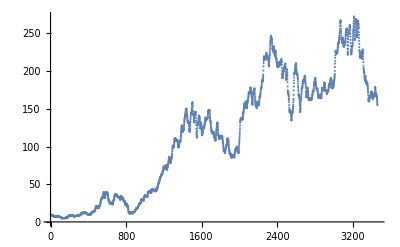

```mathematica
ListPlot[%61]
```

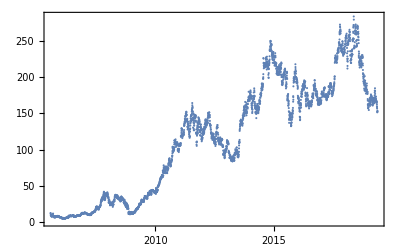

```mathematica
DateListPlot[
FinancialData["NASDAQ:BIDU", "Price", All],
Joined->False]
```

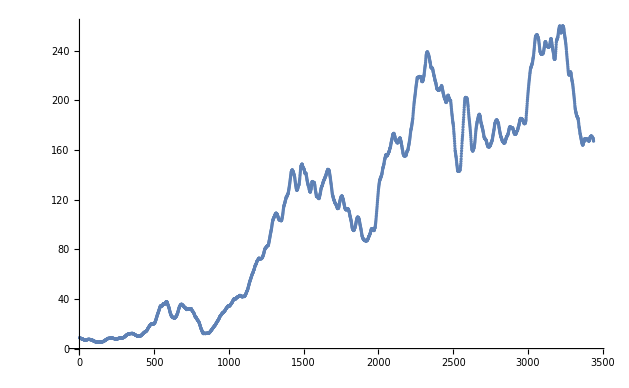

```mathematica
ListPlot[
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 30],
Joined->False]
```

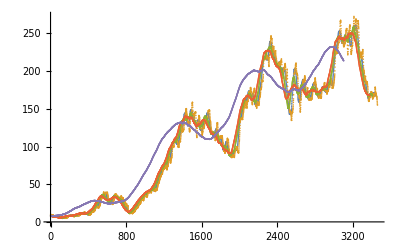

```mathematica
ListPlot[{
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 30],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 7],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 60],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 90],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 365]
},Joined->False]
```

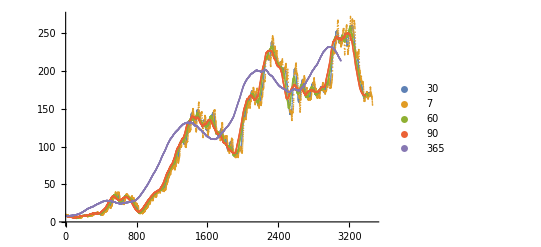

```mathematica
ListPlot[{
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 30],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 7],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 60],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 90],
MovingAverage[
Map[Last,FinancialData["NASDAQ:BIDU", "Price", All]], 365]
},Joined->False, PlotLegends->{30,7,60,90,365}]
```

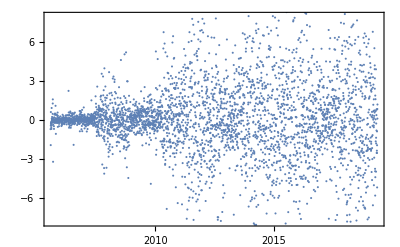

```mathematica
With[{stock="NASDAQ:BIDU"},
With[{list=FinancialData[stock, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

```mathematica
With[{stock="NASDAQ:BIDU"},
With[{list=FinancialData[stock, "Price", All]},
Take[
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Last], 10]]]
```

{{{2015,7,27},-29.65},{{2018,5,17},-26.67},{{2017,10,26},-21.25},{{2018,7,31},-19.11},{{2015,4,29},-18.72},{{2016,4,29},-15.39},{{2011,9,21},-15.15},{{2018,3,21},-13.94},{{2018,5,18},-12.5},{{2014,4,25},-11.98}}

```mathematica
With[{stock="NASDAQ:BIDU"},
With[{list=FinancialData[stock, "Price", All]},
Column@
Take[
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Last], 10]]]
```

```mathematica
1+2
```

```mathematica
1+1
```

```mathematica
1+1
```